# Multi-Layer Elastic Sphere

Bruce G. Bills

```mathematica
Off[General::spell,General::spell1];
```

objective

The objective of this notebook is to illustrate the steps involved in computing the response of a multiple-layered, 
incompressible, visco-elastic sphere to arbitrary tidal forcing. 

 The response, in this context, implies displacements, stresses, and gravity anomalies.

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

step 1:  gravity functions

### 1a: introduction

It will be useful to have 3 different gravity functions:

"gfunc" is the generic gravity propagation function.
    it propagates an input value "gs" at radius "s"
    through a layer with density "rho" to a new radius "r"
  
"gsem" takes a list of densities "rho" and radii "s" and an index "i",
      and computes the gravity at the top of layer number "i"
      
 "gtabfunc" takes as inputs
    a list of gravity values "gstab", densities "rho", radii "s", and 
    computes a gravity value at the radius corresponding to 
    relative position "x" within layer index "i"
    
    in addition, we will use a radius function "radfunc"
    which computes the  radius corresponding to 
    relative position "x" within layer index "i"

```mathematica
n=2
```

2

### 1b: build gravity functions

```mathematica
Clear[G,rho,s,gFunc,gsem,gTabFunc,radFunc]

gFunc[G_,gs_,rho_,s_,r_]:= 
	  gs(s/r)^2+(4π G)/3 rho((r^3-s^3)/r^2);


gsem[G_,rho_,s_,i_]:=
		   If[i==1,
		
			gFunc[G,  0,rho[[1]],0,s[[1]]],
		 
			  gFunc[G,gsem[G,rho,s,i-1],rho[[i]],
			                s[[i-1]],s[[i]]]];


gTabFunc[G_,gsTab_,rho_,s_,i_,x_]:=
	Module[{subs1,subs2},
		
	  subs1={gs1->0, 
			  rho1->rho[[1]],
		           s1->0,   
			  r1->s[[1]]*x};
		
	   subs2={gs2->gsTab[[i-1]],	 
			  rho2->rho[[i]],
			   s2->s[[i-1]],				  
			   r2->s[[i-1]]*(1-x)+s[[i]]*x};
							
  	  If[i==1,
		    gFunc[G,gs1,rho1,s1,r1]/.subs1,                   
		    gFunc[G,gs2,rho2,s2,r2]/.subs2]];


radFunc[s_,i_,x_]:=
		If[i==1,
	                                                   s[[1]]*x,
		s[[i-1]]*(1-x)+s[[i]]*x
	    ];
```

### 1b: test gravity functions

this test involves an 81 layer model with uniform density core and 
           linearly decreasing density throughout the outer layers

```mathematica
Clear[G,rho,s,gradTab,gsTab,gmax,smax]

G=6.67 10^-11;

rho=Table[i,{i,10,2,-0.1}]10^3;

s=Table[i+3,{i,2,10,0.1}] 10^6;

lens=Length[s];

gradTab=
   Join[{{0,0}},
		Table[{radFunc[s,i,1],gsem[G,rho,s,i]},
		{i,1,Length[s]}]];

gsTab=
	Table[gsem[G,rho,s,i],
		{i,1,Length[s]}];

gmax=Max[gsTab];

smax=Last[s];
```

```mathematica
Clear[lplt1]

lplt1=ListPlot[
   gradTab,Frame->True,
		Axes->False,PlotRange->{{0,1.05*smax},{0,1.05*gmax}},
		PlotLabel->"gravity at top of each layer",
FrameLabel->{"radius (m)","gravity (m s^-2)"}];
```

```mathematica
Clear[q,qTab,qplt]

q[i_]:=ParametricPlot[
		{radFunc[s,i,x],gTabFunc[G,gsTab,rho,s,i,x]},
		{x,0,1},DisplayFunction->Identity];

qTab=Table[q[i],{i,1,Length[s]}];

qplt=Show[qTab,DisplayFunction->$DisplayFunction,Frame->True,PlotRange->{{0,1.05*smax},{0,1.05*gmax}}];
```

```mathematica
gTabFunc[G,gsTab,rho,s,81,1]
```

18.6395

```mathematica
Length[s]
```

81

```mathematica
Show[lplt1,qplt];
```

step 2:  elastic solution fundamental matrix

### 2a: introduction

"ydir" is the matrix of  solution vectors
               "yinv" is its inverse

### 2b: build the functions

```mathematica
Clear[ydir,yinv]


ydir[n_,G_,g_,rho_,mu_,r_]:=
	
	{{n r^(1+n),n r^(-1+n),0,n (1+n) r^-n,(1+n) r^(-2-n),0},
		
		{((3+n) r^(1+n))/(1+n),r^(-1+n),0,(2-n) r^-n,-r^(-2-n),0},
		
		{r^n (2 mu (-3-n+n^2)+g n r rho),r^(-2+n) (2 mu (-1+n) n+g n r rho),
			r^n rho,                        r^(-1-n) (-2 mu n (-1+3 n+n^2)+g n (1+n) r rho),
			r^(-3-n) (-2 mu (1+n) (2+n)+g (1+n) r rho),                      r^(-1-n) rho},
		
		{(2 mu n (2+n) r^n)/(1+n),2 mu (-1+n) r^(-2+n),0,
			2 mu (-1+n^2) r^(-1-n),2 mu (2+n) r^(-3-n),0},
		
		{0,0,r^n,0,0,r^(-1-n)},
		
		{4 G n π r^(1+n) rho,4 G n π r^(-1+n) rho,(1+2 n) r^(-1+n),
			4 G n (1+n) π r^-n rho,4 G (1+n) π r^(-2-n) rho,0}};



yinv[n_,G_,g_,rho_,mu_,r_]:=
	{
  {((1+n) r^(-1-n) (-2 mu (2+n)+g r rho))/(2 mu (3+8 n+4 n^2)),(n (1+n) (2+n) r^(-1-n))/((1+2 n) (3+2 n)),
  -((1+n) r^-n)/(2 mu (3+8 n+4 n^2)),   (n (1+n) r^-n)/(2 mu (3+8 n+4 n^2)),
    ((1+n) r^-n rho)/(2 mu (3+8 n+4 n^2)),  0},
		
	{-((r^(1-n) (-2 mu (-1+3 n+n^2)+g (1+n) r rho))/(2 mu (-1+4 n^2))),-(((-1+n) (1+n)^2 r^(1-n))/(-1+4 n^2)),  
    ((1+n) r^(2-n))/(2 mu (-1+4 n^2)),  -(((-2+n) (1+n) r^(2-n))/(2 mu (-1+4 n^2))),
    -((1+n) r^(2-n) rho)/(2 mu (-1+4 n^2)),0},
		
	{-(4 G π r^(1-n) rho)/(1+2 n),0,0,0,0,r^(1-n)/(1+2 n)},

  {(r^n (2 mu (-1+n)+g r rho))/(2 mu (-1+4 n^2)),((-1+n^2) r^n)/(-1+4 n^2),
  r^(1+n)/(2 mu-8 mu n^2),  -((1+n) r^(1+n))/(2 mu (-1+4 n^2)),
   (r^(1+n) rho)/(-2 mu+8 mu n^2),0},
		
	{-((r^(2+n) (2 mu (-3-n+n^2)+g n r rho))/(2 mu (3+8 n+4 n^2))),-(n^2 (2+n) r^(2+n))/(3+8 n+4 n^2),
   (n r^(3+n))/(6 mu+16 mu n+8 mu n^2),   (n (3+n) r^(3+n))/(2 mu (3+8 n+4 n^2)),
   (n r^(3+n) rho)/(-6 mu-16 mu n-8 mu n^2), 0},
		
	{(4 G π r^(2+n) rho)/(1+2 n),0,0,0,r^(1+n),r^(2+n)/(-1-2 n)}};
```

step 3: first elastic function "yfunc"

### 3a: introduction

this function propagates solutions 
		"ys" and "gs"at radius "s" 
          to radius "r" in layer with 
		density "rho", and rigidity "mu"

### 3b: build the function

```mathematica
Clear[yFunc]
	
yFunc[n_,G_,gs_,ys_,rho_,mu_,s_,r_]:=
Module[{gr},
gr=gFunc[G,gs,rho,s,r];
		Dot[ydir[n,G,gr,rho,mu,r],
		         yinv[n,G,gs,rho,mu,s],
	         ys]];
```

### 3c: test the function "yfunc"

1. start with vector of unit values at radius   s = 1
            2. propagate vector to radius   r = 1.02
            3. plot variations in each component

```mathematica
Clear[G,gs,ys,rho,mu,s]

ys=Table[1,{i,1,6}];    (* input vector *)	

Clear[yTab]
	
yTab=
Show[
Table[
		Plot[yFunc[2,1,1,ys,1,1,1,r][[j]],
			{r,1,2}, DisplayFunction->Identity],
     {j,1,6}],

	             DisplayFunction->$DisplayFunction,
                 Frame->True,Axes->False,PlotRange->All];
```

step 4: second elastic function "ysem"

### 4a: introduction

this function generates values of elastic solution  vectors  Y
	 at bounding radii "s"

### 4a: build the function

```mathematica
Clear[X1,X2,X3,Xreg,ysem]

X1[n_,G_,g_,rho_,mu_,r_]:=
		{n r,                                               (n+3)/(n+1)r,
		n rho g r+2(n^2-n-3) mu,2n(n+2)/(n+1) mu,
		0,                                                     4Pi G  n rho r}r^n;

X2[n_,G_,g_,rho_,mu_,r_]:=
		{n r,                                               r,
		 n rho g r+2n(n-1) mu,       2(n-1) mu,
		 0,                                                    4Pi G n  rho r}r^(n-2);

X3[n_,G_,g_,rho_,mu_,r_]:=
		{0,                                                   0,
		rho r,                                             0,
		r,                                                     2n+1}r^(n-1);

Xreg[n_,G_,g_,rho_,mu_,r_]:=
	Transpose[
		{X1[n,G,g,rho,mu,r],
		  X2[n,G,g,rho,mu,r],
		  X3[n,G,g,rho,mu,r]}];

ysem[n_,G_,gs_,rho_,mu_,s_,i_]:=
	If[i==1,
		
	Xreg[n,G,
   gs[[1]],        rho[[1]],
      mu[[1]],     s[[1]]],
		
	yFunc[n,G,
    gs[[i-1]],ysem[n,G,gs,rho,mu,s,i-1],   rho[[i]],
       mu[[i]],s[[i-1]],                                                        s[[i]]]];
```

### 4b: test the function "ysem"

1. this test involves a 26 layer model
            2. the density is uniform in the core and linearly decreasing outside the core
            3. the rigidity is 10 times lower in the 13 inner layers 
                than it is in the 13 outer layers

```mathematica
Clear[G,rho,mulo,muhi,mu,s,lens,lens2,gsTab,ysTab]
	
G=6.67 10^-11;

rho=Table[i,{i,10,5,-0.2}]10^3;
s=      Table[i,{i,2,6,0.2}] 10^6;

lens=Length[s];
lens2=IntegerPart[lens/2];

mulo=Table[1,{i,1,lens2}]10^9;
muhi=Table[1,{i,lens2+1,lens}]10^10;
mu=Join[mulo,muhi];

gsTab=
	Table[gsem[G,rho,s,i],
		{i,1,lens}];

ysTab=Table[ysem[2,G,gsTab,rho,mu,s,i],
		{i,1,lens}];		

ListPlot[Table[ysTab[[i,4,1]],{i,1,lens}],PlotJoined->True,
	PlotRange->All,Frame->True,Axes->False];
```

step 5: match boundary conditions

### 5a: build the functions

```mathematica
Clear[unit,P1,P2]
	
unit[j_]:=Table[If[i==j,1,0],{i,1,6}];

P1={unit[1],unit[2],unit[5]};
P2={unit[3],unit[4],unit[6]}; (* free surface conditions *)
```

```mathematica
Clear[avec,bvec] (* tidal boundary condtions *)
	
bvec[n_,s_]:=-((2n+1)/Last[s]){0,0,1}

avec[n_,ysTab_,s_]:=	
		Dot[  Inverse[Dot[P2,Last[ysTab]]],  bvec[n,s]];

avecC[n_,ysTab_,s_]:= Module[{lf},	
	lf = LinearSolve[Rationalize[Dot[P2,Last[ysTab]]]];
	Print[lf["ConditionNumber"]];
	lf[Rationalize[bvec[n,s]]]
]
```

```mathematica
Clear[bvecLoad,avecLoad]  (* load boundary conditions *)

bvecLoad[n_,G_,gsTab_,s_]:=  -((2n+1)/Last[s]){Last[gsTab]/(4π G),0,1};        

avecLoad[n_,G_,gsTab_,ysTab_,s_]:=	
		Dot[  Inverse[Dot[P2,Last[ysTab]]],  bvecLoad[n,G,gsTab,s]];
```

```mathematica
bvec[n,s]
```

{0.,0.,-8.33333×10^-7}

```mathematica
bvecLoad[n,G,gsTab,s]
```

{-12311.1,0.,-8.33333×10^-7}

### 5b: homogeneous Love numbers

```mathematica
Clear[Np,kTid,kLod,hTid,hLod]

Np[n_]:=2 n^2+4 n+3;

kTid[n_,σ_,μ_]:=3/(2(n-1))(n σ)/(n σ+Np[n] μ) (* tidal response *);

hTid[n_,σ_,μ_]:=(2n+1)/(2(n-1))(n σ)/(n σ+Np[n] μ) (* tidal response *);


kLod[n_,σ_,μ_]:=-2/3(n-1)kTid[n,σ,μ] (* load response *);
hLod[n_,σ_,μ_]:=-2/3(n-1)hTid[n,σ,μ] (* load response *);
```

```mathematica
Np[2]
```

19

### 5c: test with 1 layer (homogeneous) model

```mathematica
rho
```

{10000.,9800.,9600.,9400.,9200.,9000.,8800.,8600.,8400.,8200.,8000.,7800.,7600.,7400.,7200.,7000.,6800.,6600.,6400.,6200.,6000.,5800.,5600.,5400.,5200.,5000.}

```mathematica
ρ=5000; μ = 10^11;
```

```mathematica
Clear[G0,rho0,mu0,s0,lens0,gsTab0,ysTab0,cvec0,cvecLoad0]
	
G0=G;

rho0=rho;
mu0= mu;

s0=    s;
lens0=Length[s0];

gsTab0=
	Table[gsem[G0,rho0,s0,i],
		{i,1,lens0}];

ysTab0=Table[ysem[n,G0,gsTab0,rho0,mu0,s0,i],
		{i,1,lens0}];

cvec0=avec[n,ysTab0,s0] //FullSimplify (* tidal BC *)

cvecLoad0=avecLoad[n,G0,gsTab0,ysTab0,s0]//FullSimplify (* load BC *)
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.76304×10^24,-2.41877×10^12,-3.84842×10^17},{-6.66508×10^23,-«21»,-«22»},{2.66595×10^14,-168.639,-1.61387×10^7}} may contain significant numerical errors.

{5.67927×10^-22,1.33191×10^-8,-7.81588×10^-14}

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.76304×10^24,-2.41877×10^12,-3.84842×10^17},{-6.66508×10^23,-«21»,-«22»},{2.66595×10^14,-168.639,-1.61387×10^7}} may contain significant numerical errors.

{-8.90982×10^-22,3.27543×10^-9,2.6915×10^-15}

```mathematica
sol0=   Dot[Xreg[n,G0,gFunc[G0,0,rho0[[1]],0,r],rho0[[1]],mu0[[1]],r],         cvec0]/.{r->R,s->R}//FullSimplify
sol0L= Dot[Xreg[n,G0,gFunc[G0,0,rho0[[1]],0,r],rho0[[1]],mu0[[1]],r],cvecLoad0]/.{r->R,s->R}//FullSimplify
```

{0.+2.66383×10^-8 R+1.13585×10^-21 R^3,0.+1.33191×10^-8 R+9.46545×10^-22 R^3,53.2766-3.84708×10^-11 R^2+3.17349×10^-23 R^4,26.6383+3.02894×10^-12 R^2,0.-7.81588×10^-14 R^2,-1.67518×10^-13 R+9.52047×10^-27 R^3}

{0.+6.55086×10^-9 R-1.78196×10^-21 R^3,0.+3.27543×10^-9 R-1.48497×10^-21 R^3,13.1017+2.11723×10^-10 R^2-4.97867×10^-23 R^4,6.55086-4.7519×10^-12 R^2,0.+2.6915×10^-15 R^2,6.83653×10^-14 R-1.4936×10^-26 R^3}

```mathematica
pot0=sol0[[5]]//FullSimplify
pot0L=sol0L[[5]]//FullSimplify
```

0.-7.81588×10^-14 R^2

0.+2.6915×10^-15 R^2

```mathematica
gSubs=Flatten[Solve[3 σ==4 π G ρ^2 R^2,R]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{R→-11.9653 √σ,R→11.9653 √σ}

```mathematica
potg0=pot0/.gSubs//FullSimplify
potg0L=pot0L/.gSubs//FullSimplify
```

0.-1.11898×10^-11 σ

0.+3.85336×10^-13 σ

```mathematica
res0=Simplify[potg0+(1+kTid[n,σ,μ])]
res0L=Simplify[potg0L+(1+kLod[n,σ,μ])]
```

(9.5×10^11-8.13034 σ-1.11898×10^-11 σ^2)/(9.5×10^11+σ)

(9.5×10^11+0.366069 σ+3.85336×10^-13 σ^2)/(9.5×10^11+σ)

### 5d: test with 2 layered, but homogeneous model

```mathematica
Clear[G1,rho1,mu1,s1,lens1,gsTab1,ysTab1,cvec1,cvecLoad1]
	
G1=6.67 10^-11;

rho1={6,6} 10^3;
mu1= {2,2} 10^9;

s1=    {3,6} 10^6;
lens1=Length[s1];

gsTab1=
	Table[gsem[G1,rho1,s1,i],
		{i,1,lens1}];

ysTab1=Table[ysem[2,G1,gsTab1,rho1,mu1,s1,i],
		{i,1,lens1}];

cvec1=avec[2,ysTab1,s1] (* tidal BC *)

cvecLoad1=avecLoad[2,G1,gsTab1,ysTab1,s1] (* load BC *)
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.59267×10^25,7.32185×10^11,2.16×10^17},{3.84×10^23,4.×10^9,0.},{2.17255×10^15,60.3487,3.×10^7}} may contain significant numerical errors.

{-3.28004×10^-22,3.14884×10^-8,-6.73671×10^-14}

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.59267×10^25,7.32185×10^11,2.16×10^17},{3.84×10^23,4.×10^9,0.},{2.17255×10^15,60.3487,3.×10^7}} may contain significant numerical errors.

{2.1867×10^-22,-2.09923×10^-8,-1.38491×10^-15}

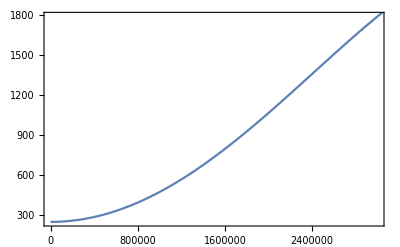

```mathematica
Clear[plt1,plt2]
	
plt1=  (* propagate up from center *)
Plot[
  Dot[Xreg[2,G1,gFunc[G1,0,rho1[[1]],0,r],
rho1[[1]],mu1[[1]],r],cvec1][[3]],{r,0,s1[[1]]},
        DisplayFunction->Identity];

plt2= (* propagate down from surface *)
     Plot[
 Dot[yFunc[2,G1,gsTab1[[1]],ysTab1[[1]],
  rho1[[2]],mu1[[2]],s1[[1]],r],cvec1][[3]],{r,s1[[1]],s1[[2]]}, 
        DisplayFunction->Identity];

homo2test=Show[plt1,plt2,DisplayFunction->$DisplayFunction,Frame->True]
```

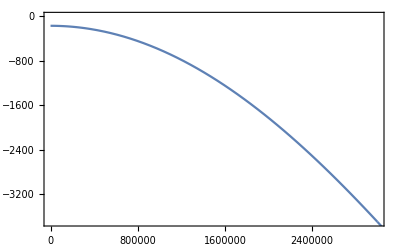

```mathematica
Clear[plt1L,plt2L]
	
plt1L=  (* propagate up from center *)
Plot[
  Dot[Xreg[2,G1,gFunc[G1,0,rho1[[1]],0,r],rho1[[1]],mu1[[1]],r],cvecLoad1][[3]],
{r,0,s1[[1]]},        DisplayFunction->Identity];

plt2L= (* propagate down from surface *)
     Plot[
 Dot[yFunc[2,G1,gsTab1[[1]],ysTab1[[1]],
  rho1[[2]],mu1[[2]],s1[[1]],r],cvecLoad1][[3]],{r,s1[[1]],s1[[2]]}, 
        DisplayFunction->Identity];

homo2testL=Show[plt1L,plt2L,DisplayFunction->$DisplayFunction,Frame->True]
```

```mathematica
Show[homo2test,homo2testL]
```

-Graphics-

### 5e: test with 2 layered model, with inner layer denser and more rigid than outer layer

this test involves a 2 layer model, with the inner layer denser and more rigid than the outer layer

```mathematica
Clear[G2,rho2,mu2,s2,lens2,gsTab2,ysTab2,cvec2,cvecLoad2]
	
G2=6.67 10^-11;

rho2={6,3} 10^3;

mu2= {2,1} 10^9;

s2=    {3,6} 10^6;

lens2=Length[s2];

gsTab2=
	Table[gsem[G2,rho2,s2,i],
		{i,1,lens2}];

ysTab2=Table[ysem[2,G2,gsTab2,rho2,mu2,s2,i],
		{i,1,lens2}];

cvec2=avec[2,ysTab2,s2]

cvecLoad2=avecLoad[2,G2,gsTab2,ysTab2,s2] (* load BC *)
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{-1.46578×10^24,-1.06831×10^12,-3.22653×10^17},{-3.05418×10^23,-«21»,-«22»},{-1.75644×10^14,-156.378,-3.72861×10^7}} may contain significant numerical errors.

{2.14027×10^-22,2.52711×10^-8,-8.46455×10^-14}

Inverse::luc: Result for Inverse of badly conditioned matrix {{-1.46578×10^24,-1.06831×10^12,-3.22653×10^17},{-3.05418×10^23,-«21»,-«22»},{-1.75644×10^14,-156.378,-3.72861×10^7}} may contain significant numerical errors.

{-1.54869×10^-21,5.86197×10^-9,5.05995×10^-15}

```mathematica
Clear[plt1,plt2]
	
plt1=  (* propagate up from center *)
Plot[
  Dot[Xreg[2,G2,gFunc[G2,0,rho2[[1]],0,r],
rho2[[1]],mu2[[1]],r],cvec2][[3]],{r,0,s2[[1]]},
        DisplayFunction->Identity];

plt2= (* propagate down from surface *)
     Plot[
 Dot[yFunc[2,G2,gsTab2[[1]],ysTab2[[1]],
  rho2[[2]],mu2[[2]],s2[[1]],r],cvec2][[3]],{r,s2[[1]],s2[[2]]}, 
        DisplayFunction->Identity];

hetero2test=Show[plt1,plt2,DisplayFunction->$DisplayFunction,Frame->True];
```

```mathematica
plt1L=  (* propagate up from center *)
Plot[
  Dot[Xreg[2,G2,gFunc[G2,0,rho2[[1]],0,r],rho2[[1]],mu2[[1]],r],cvecLoad2][[3]],
{r,0,s2[[1]]},        DisplayFunction->Identity];

plt2L= (* propagate down from surface *)
     Plot[
 Dot[yFunc[2,G2,gsTab2[[1]],ysTab2[[1]],
  rho2[[2]],mu2[[2]],s2[[1]],r],cvecLoad2][[3]],{r,s2[[1]],s2[[2]]}, 
        DisplayFunction->Identity];

hetero2testL=Show[plt1L,plt2L,DisplayFunction->$DisplayFunction,Frame->True];
```

step 6: third elastic function "ytabfunc"

### step 6a: introduction

This is a list based function.
		
	     input: lists of 
			  gravity values                   "gstab", 
			  elastic vector values          "ystab",
			  density values                    "rho", 
			  rigidity values                    "mu",
			  bounding radii                     "s", 
			  linear combination weights "cvec",

	      output: gravity at radius "r" 
			  corresponding to relative postition "x" 
			  in layer "i"

### step 6b: build the function

```mathematica
Clear[G,gsTab,ysTab,rho,mu,s,cvec,i,x,yTabFunc,yTabFunc2]

	yTabFunc[n_,G_,gsTab_,ysTab_,rho_,mu_,s_,cvec_,i_,x_]:=
	
	  Module[{subs1,subs2},
		
	       subs1=			
			{g1->gFunc[G,0,rho[[1]],0,s[[1]]*x], 
			  rho1->rho[[1]],
			  mu1->mu[[1]],
			   r1->s[[1]]*x};
		
	      subs2=
			 {gs2->gsTab[[i-1]],	
			   ys2->ysTab[[i-1]], 
			   rho2->rho[[i]],
			   mu2->mu[[i]],
			    s2->s[[i-1]],				  
			    r2->s[[i-1]]*(1-x)+s[[i]]*x};
							
  	  If[i==1,
		    Dot[Xreg[n,G,g1,rho1,mu1,r1],cvec]/.subs1, 
					                  
		    Dot[yFunc[n,G,gs2,ys2,rho2,mu2,s2,r2],cvec]/.subs2]];

yTabFunc2[n_,G_,gsTab_,ysTab_,rho_,mu_,s_,cvec_,i_,x_]:=
	
	  Module[{subs1,subs2,g1,rho1,mu1,r1,gs2,ys2,rho2,mu2,r2,s2,z},
		
	       subs1=			
			{g1->gFunc[G,0,rho[[1]],0,s[[1]]*x], 
			  rho1->rho[[1]],
			  mu1->mu[[1]],
			   r1->s[[1]]*x};
		
	      subs2=
			 {gs2->gsTab[[i-1]],	
			   ys2->ysTab[[i-1]], 
			   rho2->rho[[i]],
			   mu2->mu[[i]],
			    s2->s[[i-1]],				  
			    r2->s[[i-1]]*(1-x)+s[[i]]*x};

       z=Partition[Flatten[  If[i==1,
		   (Xreg[n,G,g1,             rho1,mu1,        r1]/.subs1),		                  
		 (yFunc[n,G,gs2,ys2,rho2,mu2,s2,r2]/.subs2)]],3];

Dot[z,cvec]];
```

### step 6c: first test of the function "ytabfunc"

the first test involves  a 6 layer model, which is homogeneous

#### introduce model parameters

```mathematica
Clear[G,rho,mulo,muhi,mu,s,lens,lens2]
	
G=6.67 10^-11;

rho={5,5,5,5,5,5}10^3;

s=     {1,2,3,4,5,6} 10^6;

lens=Length[s];

lens2=IntegerPart[lens/2];

mulo=Table[1,{i,1,              lens2}]10^10;

muhi=Table[1,{i,lens2+1,lens}]10^10;

mu=Join[mulo,muhi];
```

#### construct table of gravity and elastic layer values

```mathematica
Clear[gsTab,ysTab]

gsTab=
	Table[gsem[G,rho,s,i],
		{i,1,lens}];

ysTab=Table[ysem[2,G,gsTab,rho,mu,s,i],
		{i,1,lens}];
```

#### compute linear combination weights

```mathematica
Clear[cvec]

cvec=avec[2,ysTab,s];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.73846×10^25,5.42906×10^11,1.8×10^17},{1.92×10^24,«21»,-16.},{1.81046×10^15,50.2906,3.×10^7}} may contain significant numerical errors.

```mathematica
gsTab
```

{1.39696,2.79392,4.19088,5.58785,6.98481,8.38177}

```mathematica
Dimensions[ysTab]
G
```

{6,6,3}

6.67×10^-11

```mathematica
s
```

{1000000,2000000,3000000,4000000,5000000,6000000}

```mathematica
zz=yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,2,x]//Simplify
```

{0.0571265+0.0559239 x-0.001804 x^2-0.000601332 x^3-(2.03112×10^-18)/(1.+x)^4,0.0283628+0.0273606 x-0.00150333 x^2-0.00050111 x^3,1/(1.+x)^6(1269.49+7838.43 x+20465.2 x^2+29258.7 x^3+24775.8 x^4+12540.5 x^5+3608.32 x^6+449.063 x^7-69.8727 x^8-42.0019 x^9-4.20019 x^10),561.243-32.071 x-16.0355 x^2,-0.0580191 (1.+1. x)^2,1/(1.+x)^4(-5.06849×10^-8-2.58465×10^-7 x-5.34571×10^-7 x^2-5.69852×10^-7 x^3-3.29028×10^-7 x^4-1.01087×10^-7 x^5-1.76408×10^-8 x^6-2.52011×10^-9 x^7)}

```mathematica
zz/.x->1
```

{0.110645,0.053719,1563.9,513.137,-0.232077,-1.16491×10^-7}

```mathematica
yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,2,1]//Simplify
```

{0.110645,0.053719,1563.9,513.137,-0.232077,-1.16491×10^-7}

#### define plotting functions

```mathematica
Clear[qq,labels,qqplot]

qq[i_,j_]:=
       ParametricPlot[
		{radFunc[s,i,x],
			yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,i,x][[j]]},
	    	    {x,0,1},DisplayFunction->Identity,AspectRatio->1/2];

labels={"u_r","u_θ","τ_rr","τ_rθ","Φ","q"};


qqplot[j_]:=Show[Table[qq[i,j],{i,1,lens}],
		PlotRange->All,PlotLabel->labels[[j]],
		DisplayFunction->$DisplayFunction,
   	Axes->Frame,Frame->True];
```

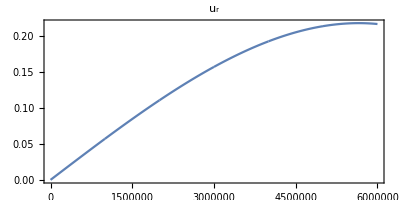
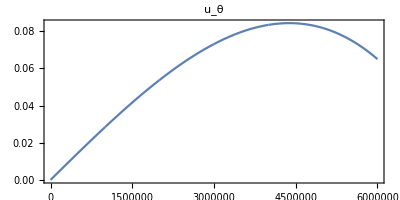
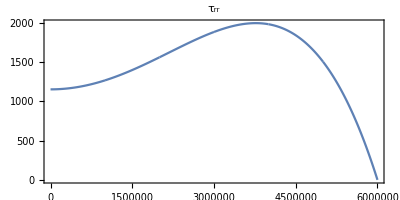
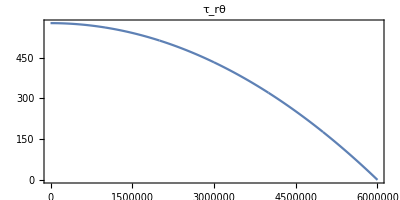
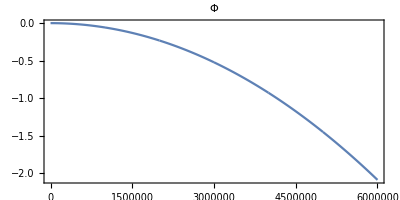
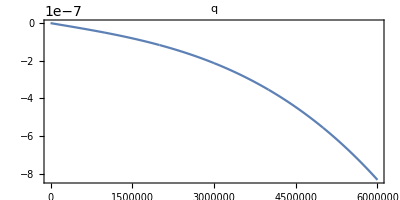

```mathematica
Table[qqplot[i],{i,1,6}]
```

```mathematica
Table[yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,4,0.1][[j]],{j,1,6}]
```

{0.161042,0.0745496,1911.56,423.177,-0.557564,-2.24388×10^-7}

```mathematica
{0.16104213104963552,0.07454963796998118,1911.5558084313043,423.1773976627508,-0.5575638947802454,-2.2438761753507738*^-7}
{0.161291 ,0.0746153 ,5163.13 ,423.884,-0.557266,-2.24217*10^-7}
```

{0.161042,0.0745496,1911.56,423.177,-0.557564,-2.24388×10^-7}

{0.161291,0.0746153,5163.13,423.884,-0.557266,-2.24217×10^-7}

```mathematica
Table[yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,lens,1][[j]],{j,1,6}]
```

{0.21648,0.0649439,7.27596×10^-12,1.15568×10^-12,-2.08869,-8.33333×10^-7}

```mathematica
{0.21647953271872436,0.0649438598156174,7.275957614183426*^-12,1.1556798478140885*^-12,-2.088688887834425,-8.333333333333312*^-7}
{0.216691, 0.0649933,-9.09495*10^-13,-1.13687*10^-13,-2.08757,-8.33333*10^-07}
```

{0.21648,0.0649439,7.27596×10^-12,1.15568×10^-12,-2.08869,-8.33333×10^-7}

{0.216691,0.0649933,-9.09495×10^-13,-1.13687×10^-13,-2.08757,-8.33333×10^-7}

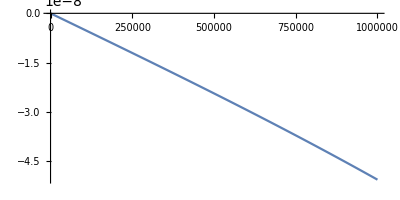

```mathematica
qq[1,-1]
```

```mathematica
qqplot[1]
```

-Graphics-

### step 6d: second test of the function "ytabfunc"

the second test involves a 6 layer model, but with non-homogeneous structure

#### introduce model parameters

```mathematica
Clear[G,rho,mulo,muhi,mu,s,lens,lens2]

G=6.67 10^-11;

rho={10,9,8,5,5,3}10^3;

s=     {1,2,3,4,5,6} 10^6;

lens=Length[s];

lens2=IntegerPart[lens/2];

mulo=Table[1,{i,1,lens2}]10^8;

muhi=Table[1,{i,lens2+1,lens}]10^10;

mu=Join[mulo,muhi];
```

#### construct tables of gravity and elastic layer values

```mathematica
Clear[gsTab]

gsTab=
	Table[gsem[G,rho,s,i],
		{i,1,lens}];

ysTab=Table[ysem[2,G,gsTab,rho,mu,s,i],
		{i,1,lens}];
```

#### compute linear combination weights

```mathematica
Clear[cvec]

cvec=avec[2,ysTab,s];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{-3.62311×10^24,1.38597×10^13,2.47587×10^18},{1.2436×10^23,«22»,«22»},{-4.20687×10^14,1647.63,3.03196×10^8}} may contain significant numerical errors.

#### define plotting functions

```mathematica
Clear[qq,labels,qqplot]

qq[i_,j_]:=
   ParametricPlot[
		{radFunc[s,i,x],
			yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,i,x][[j]]},
	    	{x,0,1},DisplayFunction->Identity,AspectRatio->1/2];

labels={"u_r","u_θ","τ_rr","τ_rθ","Φ","q"};

qqplot[j_]:=Show[Table[qq[i,j],{i,1,lens}],
		PlotRange->All,PlotLabel->labels[[j]],
		DisplayFunction->$DisplayFunction,
   	Axes->False,Frame->True];
```

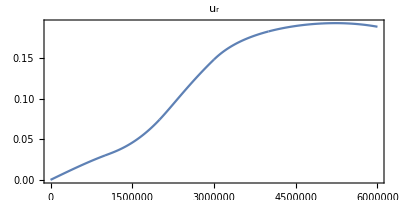
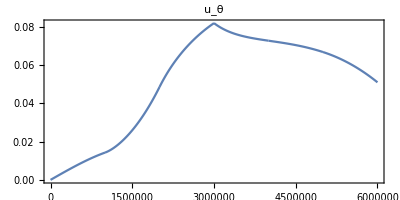
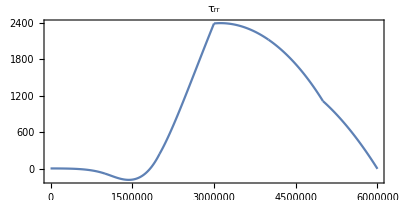
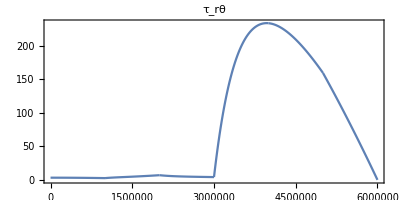
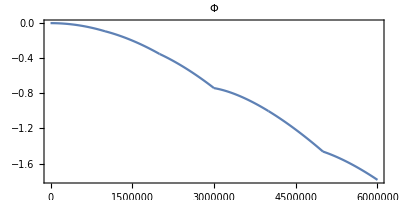
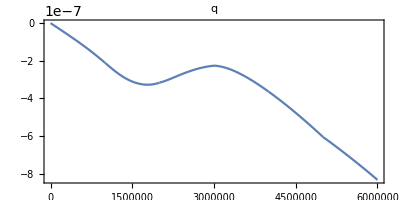

```mathematica
Table[qqplot[j],{j,1,6}]
```

```mathematica
Table[yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,5,0.9][[j]],{j,1,6}]
```

{0.192409,0.0676984,1252.54,170.82,-1.41015,-5.78393×10^-7}

```mathematica
{0.17103754679302074,0.07536097281942311,2343.815095431766,199.319612864816,-0.838059213155526,-2.7231294888264166*^-7}
{0.21178, 0.15657, 3334.89,-3.8649,-0.882155,-2.14557*10^-07}
```

{0.171038,0.075361,2343.82,199.32,-0.838059,-2.72313×10^-7}

{0.21178,0.15657,3334.89,-3.8649,-0.882155,-2.14557×10^-7}

```mathematica
Table[yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,lens,1][[j]],{j,1,6}]
```

{0.188697,0.0509836,0.,-1.45519×10^-11,-1.78532,-8.33333×10^-7}

```mathematica
{0.18869710442642784,0.05098364580163928,0.,-1.4551915228366852*^-11,-1.785317262861235,-8.333333333333276*^-7}
{0.223074, 0.0448708 ,0, 5.82077*10^-11,-1.93383,-8.33333*10^-07}
```

{0.188697,0.0509836,0.,-1.45519×10^-11,-1.78532,-8.33333×10^-7}

{0.223074,0.0448708,0,5.82077×10^-11,-1.93383,-8.33333×10^-7}

### Doing stuff! Using rheology from Bierson & Nimmo 2016 and trying out complex mu

```mathematica
Clear[G,rho,mulo,muhi,mu,s,lens,lens2]

G=6.67 10^-11;

rho={3.5,3.5,3.5,3.5,3.5,3.5}10^3;

s=     {1350,1400,1450,1600,1700,1800} 10^6;

lens=Length[s];

mu = {40,20,5,4,3,2}10^9;

eta = {1000,80,50,5,4,3}10^18;

omega=10^-5;
mubar = mu/(1+mu/(I*eta*omega));
Clear[gsTab,ysTab]

gsTab=
	Table[gsem[G,rho,s,i],
		{i,1,lens}];

ysTab=Table[ysem[2,G,gsTab,rho,mu,s,i],
		{i,1,lens}];
ysTabBar = Table[ysem[2,G,gsTab,rho,mubar,s,i],
		{i,1,lens}];
Clear[cvec]

cvec=avec[2,ysTab,s];
cvecBar = avec[2,ysTabBar,s];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.05963×10^35,4.08391×10^16,1.134×10^22},«1»,{9.80776×10^22,19447.1,9.×10^9}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.05963×10^35-8.28809×10^30 ⅈ,4.0839×10^16-1.06464×10^12 ⅈ,1.134×10^22+8.03902×10^11 ⅈ},{«1»},«1»} may contain significant numerical errors.

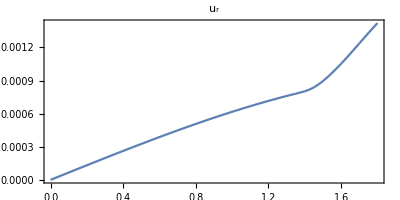
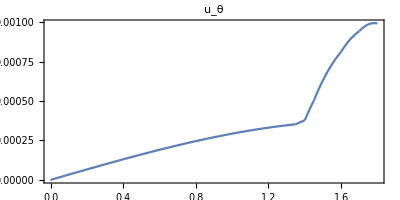
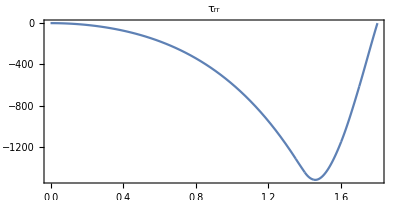
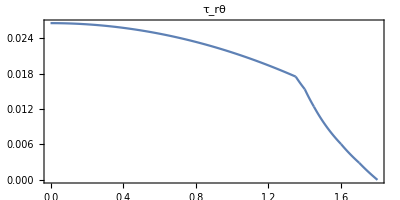
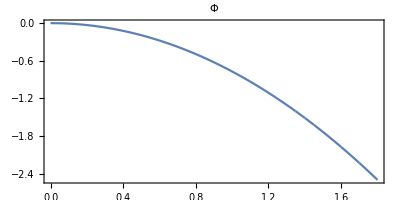
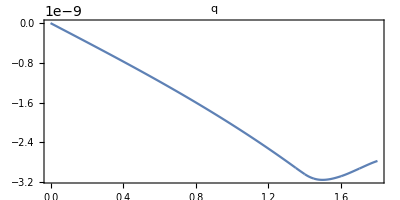

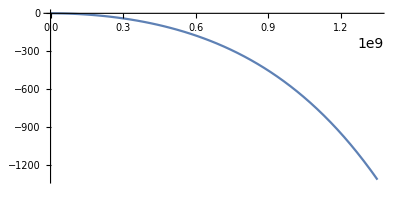

```mathematica
Clear[qq,labels,qqplot]

qq[i_,j_]:=
   ParametricPlot[
		{radFunc[s,i,x],
			yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,i,x][[j]]},
	    	{x,0,1},DisplayFunction->Identity,AspectRatio->1/2];

labels={"u_r","u_θ","τ_rr","τ_rθ","Φ","q"};

qqplot[j_]:=Show[Table[qq[i,j],{i,1,lens}],
		PlotRange->All,PlotLabel->labels[[j]],
		DisplayFunction->$DisplayFunction,
   	Axes->False,Frame->True];
Table[qqplot[j],{j,1,6}]
qq[1,3]
```

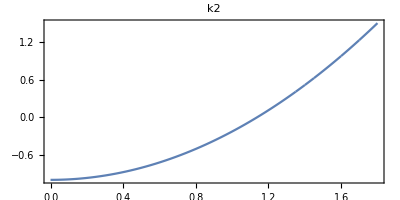

```mathematica
Show[Table[ParametricPlot[
		{radFunc[s,i,x],
			-yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,i,x][[5]]-1},
	    	{x,0,1},DisplayFunction->Identity,AspectRatio->1/2],{i,1,lens}],PlotRange->All,PlotLabel->"k2",
		DisplayFunction->$DisplayFunction,
   	Axes->False,Frame->True]
```

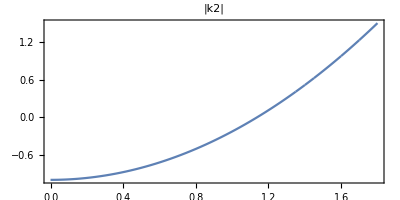
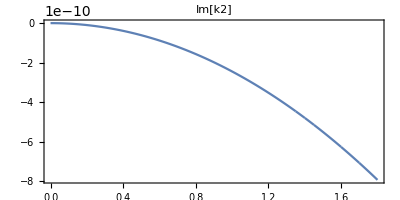

```mathematica
Table[{Show[Table[ParametricPlot[
		{radFunc[s,i,x],
			Norm[-yTabFunc2[2,G,gsTab,ysTabBar,rho,mubar,s,cvecBar,i,x][[5]]]-1},
	    	{x,0,1},DisplayFunction->Identity,AspectRatio->1/2],{i,1,lens}],PlotRange->All,PlotLabel->"|k2|",
		DisplayFunction->$DisplayFunction,
   	Axes->False,Frame->True],Show[Table[ParametricPlot[
		{radFunc[s,i,x],
			Im[-yTabFunc2[2,G,gsTab,ysTabBar,rho,mubar,s,cvecBar,i,x][[5]]-1]},
	    	{x,0,1},DisplayFunction->Identity,AspectRatio->1/2],{i,1,lens}],PlotRange->All,PlotLabel->"Im[k2]",
		DisplayFunction->$DisplayFunction,
   	Axes->False,Frame->True]}]
```

```mathematica
lens
```

6

```mathematica
Clear[omega];
```

```mathematica
yTabFunc2[2,G,gsTab,ysTabBar,rho,mubar,s,cvecBar,6,.5][[5]]/.omega->{10^-10,10^-8,10^-6,10^-5,10^-4,10^-2,1}
```

-2.36302+7.50113×10^-10 ⅈ

```mathematica
yTabFunc2[2,G,gsTab,ysTabBar,rho,mubar,s,cvecBar,6,.5][[5]]/.omega->{10^-20,10^-18,10^-16,10^-15,10^-14,10^-12}
```

-2.36302+7.50113×10^-10 ⅈ

```mathematica
yTabFunc2[2,G,gsTab,ysTabBar,rho,mubar,s,cvecBar,6,.5][[5]]/.omega->10^-11
```

-2.36302+7.50113×10^-10 ⅈ

{1/10000000000,1/100000000,1/1000000,1/100000,1/10000,1/100,1,1/100000000000000000000,1/1000000000000000000,1/10000000000000000,1/1000000000000000,1/100000000000000,1/1000000000000}

{-2.36304+7.63663×10^-6 ⅈ,-2.36302+7.49078×10^-7 ⅈ,-2.36302+7.5011×10^-9 ⅈ,-2.36302+7.50034×10^-10 ⅈ,-2.36302+7.49941×10^-11 ⅈ,-2.36302+7.49943×10^-13 ⅈ,-2.36302+7.50087×10^-15 ⅈ,1.55486×10^-13-8.25535×10^-15 ⅈ,2.60753×10^-9-2.1163×10^-10 ⅈ,0.000276961+0.000316516 ⅈ,-2.04053+0.810845 ⅈ,-2.36303-0.00512275 ⅈ,-2.36304-3.57792×10^-7 ⅈ}

{7.63663×10^-6,7.49078×10^-7,7.5011×10^-9,7.50034×10^-10,7.49941×10^-11,7.49943×10^-13,7.50087×10^-15,-8.25535×10^-15,-2.1163×10^-10,0.000316516,0.810845,-0.00512275,-3.57792×10^-7}

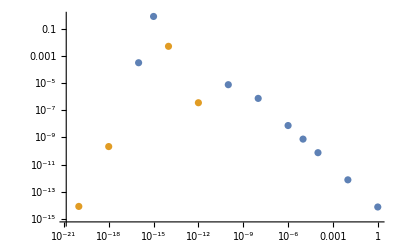

```mathematica
inputs = Join[{10^-10,10^-8,10^-6,10^-5,10^-4,10^-2,1},{10^-20,10^-18,10^-16,10^-15,10^-14,10^-12}]
outputs = Join[{-2.3630373864221825+7.636633954120627*^-6 ⅈ,-2.3630154193895456+7.490783041953156*^-7 ⅈ,-2.363015393339186+7.501097764066644*^-9 ⅈ,-2.363015393473806+7.500337967875061*^-10 ⅈ,-2.363015393058205+7.499412819729214*^-11 ⅈ,-2.3630153930595554+7.499427500169923*^-13 ⅈ,-2.3630153930595634+7.500873669551583*^-15 ⅈ},{1.5548608780286437*^-13-8.255353786455957*^-15 ⅈ,2.607527650102152*^-9-2.1163047398653146*^-10 ⅈ,0.000276961028249137+0.0003165158063284522 ⅈ,-2.040529987615211+0.8108449663486496 ⅈ,-2.3630286779475687-0.005122747755836883 ⅈ,-2.36304012569592-3.577921954836974*^-7 ⅈ}]
Im[outputs]
ListLogLogPlot[{Transpose[{inputs,Im[outputs]}],Transpose[{inputs,-Im[outputs]}]}]
```

```mathematica
Two layer benchmark from Harrison 1963
```

1963 benchmark from Harrison layer Two

### Two layer benchmark from Harrison 1963

```mathematica
Clear[k2Harrison, H1, H2, H3, H4];
(* alpha is r_core/r_mantle, eta = (rho_core/rho_mantle-1), sigma = mu_mantle/g_surf*rho_mantle*r_mantle, delta = mu_core/mu_mantle, epsilon = (delta-1)/delta*)
k2Harrison[eta_, alpha_, sigma_, epsilon_,delta_]:= 3/5 * (H2[eta, alpha, sigma, epsilon,delta] + H4[eta, alpha, sigma, epsilon,delta]  + eta*alpha^5*(H1[eta, alpha, sigma, epsilon,delta]+H3[eta, alpha, sigma, epsilon,delta]))/((1+eta*alpha^3)(H2[eta, alpha, sigma, epsilon,delta]*H3[eta, alpha, sigma, epsilon,delta]-H1[eta, alpha, sigma, epsilon,delta]*H4[eta, alpha, sigma, epsilon,delta]));
H1[eta_, alpha_, sigma_, epsilon_,delta_] := 3/5*1/(1+eta*alpha^3)+sigma/(5*eta*alpha^2)*((35*(8-3alpha^2)-2(64-21alpha^2+21alpha^5-64alpha^7)*epsilon)/(4-7alpha^3+3alpha^7-2(1-alpha^3)(1-alpha^7)*epsilon));
H2[eta_, alpha_, sigma_, epsilon_,delta_] := (1+2eta/5)/(1+eta*alpha^3) + sigma/(5*eta*alpha^2)*(19(delta-1) + (175-2(43+21alpha^3-64alpha^7)*epsilon)/(4-7alpha^3+3alpha^7-2(1-alpha^3)(1-alpha^7)*epsilon));
H3[eta_, alpha_, sigma_, epsilon_,delta_] := 1-3/5*1/(1+eta*alpha^3)+sigma/5*(19+alpha^3*(7(8-3alpha^2)^2-2(64-21alpha^4-43alpha^7)*epsilon)/(4-7alpha^3+3alpha^7-2(1-alpha^3)(1-alpha^7)*epsilon));
H4[eta_, alpha_, sigma_, epsilon_,delta_] := eta*alpha^5*H1[eta, alpha, sigma, epsilon,delta];
```

```mathematica
Clear[eta,alpha,sigma,epsilon,delta];
al = 1.4/1.8;
et = 0.001;
sig = 3*10^9/(4Pi/3*6.67*10^-11*3500*1.8*10^6*3500*1.8*10^6);
del = 3/40;
eps = (del-1)/del;
k2Harrison[et,al,sig,eps,del]

Clear[eta,alpha,sigma,epsilon,delta];
al = .1/1.8;
et = 2;
sig = 50*10^9/(4Pi/3*6.67*10^-11*3500*1.8*10^6*3500*1.8*10^6);
del = 1;
eps = (del-1)/del;
k2Harrison[et,al,sig,eps,del]
```

0.946802

0.0342073

### Comparing to two layer Harrison 1963 questions

```mathematica
Clear[G,rho,mulo,muhi,mu,s,lens,lens2]

G=6.67 10^-11;

rho={5000,3500};

s=     {1.4,1.8} 10^6;

lens=Length[s];

mu = {40,4}10^9;

Clear[gsTab]

gsTab=
	Table[gsem[G,rho,s,i],
		{i,1,lens}];

ysTab=Table[ysem[2,G,gsTab,rho,mu,s,i],
		{i,1,lens}];

Clear[cvec]

cvec=avec[2,ysTab,s];

Clear[qq,labels,qqplot]

qq[i_,j_]:=
   ParametricPlot[
		{radFunc[s,i,x],
			yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,i,x][[j]]},
	    	{x,0,1},DisplayFunction->Identity,AspectRatio->1/2];

labels={"u_r","u_θ","τ_rr","τ_rθ","Φ","q"};

qqplot[j_]:=Show[Table[qq[i,j],{i,1,lens}],
		PlotRange->All,PlotLabel->labels[[j]],
		DisplayFunction->$DisplayFunction,
   	Axes->False,Frame->True];
k2HarrisonEasyInputs[radii_,densities_,rigidities_]:= Module[{al,et,sig,eps,del,g},
al = radii[[1]]/radii[[2]];
et = densities[[1]]/densities[[2]]-1;
g = G(4Pi/3*radii[[1]]^3*densities[[1]] + 4Pi/3*(radii[[2]]^3-radii[[1]]^3)*densities[[2]])/radii[[2]]^2;
sig = rigidities[[2]]/(g*densities[[2]]*radii[[2]]);
del = rigidities[[1]]/rigidities[[2]];
eps = (del-1)/del;
k2Harrison[et,al,sig,eps,del]]

(* Table[qqplot[j],{j,1,6}] *)
"k2 with Bills code:"
k2surf = -yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,lens,1][[5]]-1
"k2 with Harrison equations:"
k2HarrisonEasyInputs[s,rho,mu]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.77073×10^23,2.40444×10^11,1.39071×10^16},{3.9554×10^23,«23»,-«22»},{1.06105×10^14,24.4941,8.95577×10^6}} may contain significant numerical errors.

k2 with Bills code:

0.0900634

k2 with Harrison equations:

0.0900634

```mathematica
k2HarrisonEasyInputs[{1.4*10^6,1.8*10^6},{3500,9862},{1*10^9,1*10^9}]
```

{-3181/4931,0.777778,0.0163082,0,1}

0.536522

```mathematica
k2HarrisonEasyInputs[{1.4*10^6,1.8*10^6},{3000,3500},{40*10^9,4*10^9}]
```

0.0723394

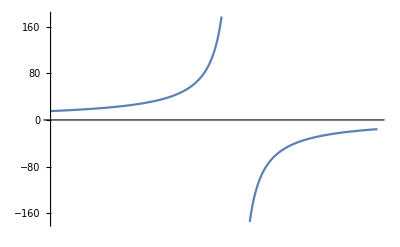

```mathematica
LogLinearPlot[k2HarrisonEasyInputs[{1.4*10^6,1.8*10^6},{3500,x},{1*10^9,1*10^9}],{x,9860,9863}]
```

```mathematica
G(4Pi/3*s[[1]]^3*rho[[1]] + 4Pi/3*(s[[2]]^3-s[[1]]^3)*rho[[2]])/s[[2]]^2
```

2.1151

```mathematica
0.07648611986118888
0.0764861198611888
```

0.0764861

0.0764861

```mathematica
NumberForm[0.0764861198611888,16]
```

0.07648611986118881

```mathematica
results = {}
```

{}

```mathematica
yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,lens,1][[1]]G(4Pi/3*s[[1]]^3*rho[[1]] + 4Pi/3*(s[[2]]^3-s[[1]]^3)*rho[[2]])/s[[2]]^2
```

0.163814

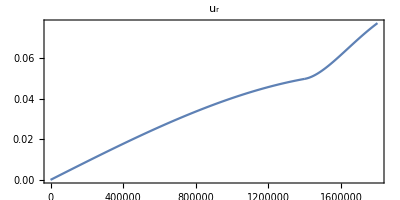
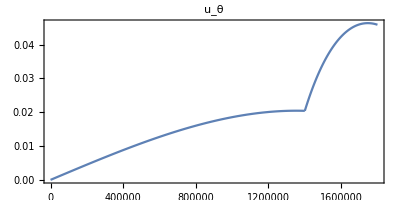
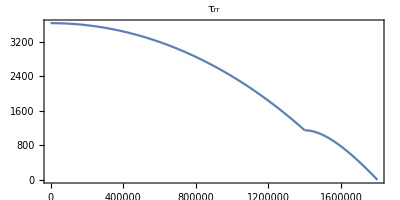
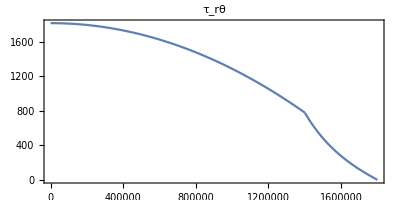
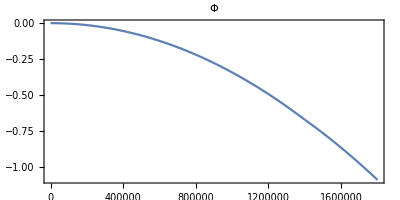
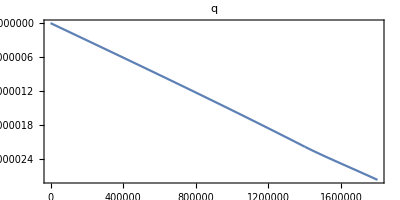

```mathematica
Table[qqplot[j],{j,1,6}]
```

```mathematica
{{0.16104213104963552,0.07454963796998118,1911.5558084313043,423.1773976627508,-0.5575638947802454,-2.2438761753507738*^-7},
{0.161291 ,0.0746153 ,5163.13 ,423.884,-0.557266,-2.24217*10^-7},{0.21647953271872436,0.0649438598156174,7.275957614183426*^-12,1.1556798478140885*^-12,-2.088688887834425,-8.333333333333312*^-7},
{0.216691, 0.0649933,-9.09495*10^-13,-1.13687*10^-13,-2.08757,-8.33333*10^-07},{0.17103754679302074,0.07536097281942311,2343.815095431766,199.319612864816,-0.838059213155526,-2.7231294888264166*^-7},
{0.21178, 0.15657, 3334.89,-3.8649,-0.882155,-2.14557*10^-07},{0.18869710442642784,0.05098364580163928,0.,-1.4551915228366852*^-11,-1.785317262861235,-8.333333333333276*^-7},
{0.223074, 0.0448708 ,0, 5.82077*10^-11,-1.93383,-8.33333*10^-07}}
```

{{0.161042,0.0745496,1911.56,423.177,-0.557564,-2.24388×10^-7},{0.161291,0.0746153,5163.13,423.884,-0.557266,-2.24217×10^-7},{0.21648,0.0649439,7.27596×10^-12,1.15568×10^-12,-2.08869,-8.33333×10^-7},{0.216691,0.0649933,-9.09495×10^-13,-1.13687×10^-13,-2.08757,-8.33333×10^-7},{0.171038,0.075361,2343.82,199.32,-0.838059,-2.72313×10^-7},{0.21178,0.15657,3334.89,-3.8649,-0.882155,-2.14557×10^-7},{0.188697,0.0509836,0.,-1.45519×10^-11,-1.78532,-8.33333×10^-7},{0.223074,0.0448708,0,5.82077×10^-11,-1.93383,-8.33333×10^-7}}

```mathematica
Grid[{{"source","y1","y2","y3","y4","y5","y6"},{"homogenous,bills,mid",0.16104213104963552,0.07454963796998118,1911.5558084313043,423.1773976627508,-0.5575638947802454,-2.2438761753507738*^-7},{"homogenous,roberts,mid",0.161291,0.0746153,5163.13,423.884,-0.557266,-2.24217*^-7},{},{"homogenous,bills,top",0.21647953271872436,0.0649438598156174,7.275957614183426*^-12,1.1556798478140885*^-12,-2.088688887834425,-8.333333333333312*^-7},{"homogenous,roberts,top",0.216691,0.0649933,-9.09495*^-13,-1.13687*^-13,-2.08757,-8.33333*^-7},{},{},{"layered,bills,mid",0.17103754679302074,0.07536097281942311,2343.815095431766,199.319612864816,-0.838059213155526,-2.7231294888264166*^-7},{"layered,roberts,mid",0.21178,0.15657,3334.89,-3.8649,-0.882155,-2.14557*^-7},{},{"layered,bills,top",0.18869710442642784,0.05098364580163928,0.,-1.4551915228366852*^-11,-1.785317262861235,-8.333333333333276*^-7},{"layered,roberts,top",0.223074,0.0448708,0,5.82077*^-11,-1.93383,-8.33333*^-7}}]
```

source | y1 | y2 | y3 | y4 | y5 | y6
homogenous,bills,mid | 0.161042 | 0.0745496 | 1911.56 | 423.177 | -0.557564 | -2.24388×10^-7
homogenous,roberts,mid | 0.161291 | 0.0746153 | 5163.13 | 423.884 | -0.557266 | -2.24217×10^-7
 |  |  |  |  |  | 
homogenous,bills,top | 0.21648 | 0.0649439 | 7.27596×10^-12 | 1.15568×10^-12 | -2.08869 | -8.33333×10^-7
homogenous,roberts,top | 0.216691 | 0.0649933 | -9.09495×10^-13 | -1.13687×10^-13 | -2.08757 | -8.33333×10^-7
 |  |  |  |  |  | 
 |  |  |  |  |  | 
layered,bills,mid | 0.171038 | 0.075361 | 2343.82 | 199.32 | -0.838059 | -2.72313×10^-7
layered,roberts,mid | 0.21178 | 0.15657 | 3334.89 | -3.8649 | -0.882155 | -2.14557×10^-7
 |  |  |  |  |  | 
layered,bills,top | 0.188697 | 0.0509836 | 0. | -1.45519×10^-11 | -1.78532 | -8.33333×10^-7
layered,roberts,top | 0.223074 | 0.0448708 | 0 | 5.82077×10^-11 | -1.93383 | -8.33333×10^-7

```mathematica
Grid[{{"Source","y1","y2","y3","y4","y5","y6"},Join[{"800 km, Bills"},Table[yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,1,.8/1.4][[j]],{j,1,6}]],{"800 km, Roberts",0.0351959 ,0.0162677, 2790.51 ,1537.75,-0.219651,-1.22532*10^-06},{},Join[{"1600 km, Bills"},Table[yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,2,.5][[j]],{j,1,6}]],
{"1600 km, Roberts",0.0625577, 0.0424586, 794.806, 276.765,-0.867231,-2.48915*10^-06},{},Join[{"Surface, Bills"},Table[yTabFunc2[2,G,gsTab,ysTab,rho,mu,s,cvec,2,1][[j]],{j,1,6}]],{"Surface,Roberts",0.0780511 ,0.045925,-2.84217*10^-14,-5.68434*10^-14,-1.09084,-2.77778*10^-06}}]
```

Source | y1 | y2 | y3 | y4 | y5 | y6
800 km, Bills | 0.03376 | 0.0160342 | 2848.14 | 1476.54 | -0.219426 | -1.22993×10^-6
800 km, Roberts | 0.0351959 | 0.0162677 | 2790.51 | 1537.75 | -0.219651 | -1.22532×10^-6
 |  |  |  |  |  | 
1600 km, Bills | 0.0618299 | 0.0423885 | 773.71 | 276.124 | -0.866525 | -2.48971×10^-6
1600 km, Roberts | 0.0625577 | 0.0424586 | 794.806 | 276.765 | -0.867231 | -2.48915×10^-6
 |  |  |  |  |  | 
Surface, Bills | 0.0774495 | 0.0459123 | 0. | -2.84217×10^-13 | -1.09006 | -2.77778×10^-6
Surface,Roberts | 0.0780511 | 0.045925 | -2.84217×10^-14 | -5.68434×10^-14 | -1.09084 | -2.77778×10^-6

```mathematica
radFunc[s,2,.5]
```

1.6×10^6

### Setting up Imk2 stuff

```mathematica
hans = {6.66488206094624*^-75,1.2124062280744796*^-72,2.206280788469157*^-70,4.016411308912115*^-68,7.314568000592725*^-66,1.3326653957733965*^-63,2.429096950531036*^-61,4.429653156840753*^-59,8.081762344080651*^-57,1.475246715126024*^-54,2.694365523166882*^-52,4.923713759106105*^-50,9.00294205870115*^-48,1.6471825307562992*^-45,3.015597492294789*^-43,5.524404199505815*^-41,1.0126966511578418*^-38,1.8575858465397815*^-36,3.409377705388488*^-34,6.260635168691211*^-32,1.1500178868893372*^-29,2.112521625780128*^-27,3.8785892413017054*^-25,7.110561455070078*^-23,1.2993363395576417*^-20,2.3585171082497205*^-18,4.2223503699994234*^-16,7.331602247390085*^-14,1.177414271298179*^-11,1.4358707608103804*^-9,0.,-0.00204999569221725,0.9999579747527397,0.014349470171360231,0.00014287958400041335,1.2132477059893726*^-6,9.412905839082057*^-9,6.889106744522358*^-11,4.840176401564523*^-13,3.299414036191223*^-15,2.197406821880405*^-17,1.4367028518263247*^-19,9.253499868197746*^-22,5.8863041918809306*^-24,3.705344310900341*^-26,2.3116853112854613*^-28,1.4311082208813688*^-30,8.800108869916285*^-33,5.379311240013734*^-35,3.270996383394833*^-37,1.9796714016673693*^-39,1.193090505505416*^-41,7.163056632963753*^-44,4.285692647295767*^-46,2.5560774092009874*^-48,1.5201036914662917*^-50,9.016136047974418*^-53,5.3346463441677565*^-55,3.1492601342382434*^-57,1.8552408589748504*^-59,1.090798721282453*^-61};
```

```mathematica
Clear[n,myohm,imk2mantle,powerLawCheck,powerLawSolve,torqueMaxwellTalk,torqueAndradeTalk,torqueAndrade,imk2andradeTalk,imk2andrade,AndradeMu,fitconstraint,findzero,torque,imk2twolayerfitconstraint,imk2twolayer,imk2,imk2Talk,DecentLogLinearPlot,DecentLogLogPlot,DecentPlot];
n=2Pi/(42*60*60);
myohm = 2Pi/(42*60*60-5);

Off[Inverse::luc] (* Quiets the error message about conditioning *)
DecentPlot[func_,min_,max_,points_]:= Module[{temp},temp[xx_]:=func[xx];ListPlot[Transpose[{Range[min,max,(max-min)/points],Table[temp[x],{x,Range[min,max,(max-min)/points]}]}]]]

DecentLogLogPlot[func_,min_,max_,points_]:= Module[{temp},temp[xx_]:=func[xx];ListLogLogPlot[Transpose[{10^Range[min,max,(max-min)/points],Table[temp[x],{x,10^Range[min,max,(max-min)/points]}]}]]]

DecentLogLinearPlot[func_,min_,max_,points_]:= Module[{temp},temp[xx_]:=func[xx];ListLogLinearPlot[Transpose[{10^Range[min,max,(max-min)/points],Table[temp[x],{x,10^Range[min,max,(max-min)/points]}]}]]]
imk2Talk[myomega_] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5}10^3;
mys=     {1800} 10^3;
mylens=Length[mys];
mymu = {100}10^9;
myeta = {1000}10^18;
mymubar = mymu/(1+mymu/(I*myeta*myomega));
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
imk2[myomega_] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5,3.5,3.5}10^3;
mys=     {1350,1400,1450,1600,1700,1800} 10^3;
mylens=Length[mys];
mymu = {40,20,5,4,3,2}10^9;
myeta = {1000,80,50,5,4,3}10^18;
mymubar = mymu/(1+mymu/(I*myeta*myomega));
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
imk2twolayer[myomega_] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={5,3.5}10^3;
mys=     {1400,1800} 10^3;
mylens=Length[mys];
mymu = {40,4}10^9;
myeta = {1000,3}10^18;
mymubar = mymu/(1+mymu/(I*myeta*myomega));
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
imk2twolayerfitconstraint[myomega_,x_] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,constraint,val},
G=6.67 10^-11;
constraint = 0.015;
myrho={5,3.5}10^3;
mys=     {1400,1800} 10^3;
mylens=Length[mys];
mymu = {40,4}10^9;
myeta = {1000,3}10^18*x;
mymubar = mymu/(1+mymu/(I*myeta*myomega));
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
torque[myomega_,myhansens_,k2func_,myn_:n]:=Module[{myomegaks,mykmax,myks,x},
mykmax = (Length[myhansens]-1)/2;
myomegaks = 2*myomega - Range[-mykmax,mykmax]*myn;
myks = k2func[x]/.x->myomegaks;
Total[myhansens^2*myks]
]
findzero[myhansens_,myimk2_,var_,myn_:n]:=Module[{myomegaks,mykmax,myks,x},
mykmax = (Length[myhansens]-1)/2;
FindRoot[Total[myhansens^2*(myimk2[x]/.x->(2*myn(1+var) - Range[-mykmax,mykmax]*myn))],{var,10^-11}]
]
fitconstraint[torfunc_,constraint_:0.015,omegaconstraint_:n] := Module[{x,res},
res = x/.FindRoot[torfunc[x]-constraint,x]
]
AndradeMu[myomega_,mymu_,eta_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374]:=
(*This uses equations 2,3,7,8,9,10 from Bierson&Nimmo 2016, corrected by Correia eq 64 for negative ohm*)
Module[{j1,j2,mubar,ohm,bigx},
bigx = (2Pi/myomega)*Exp[-eb/8.3145*(1/temp-1/tempr)];
ohm = Abs[2Pi/bigx];
j1 = 1/mymu+beta*ohm^-alpha*Gamma[alpha+1]*Cos[alpha*Pi/2];
j2 = beta*ohm^-alpha*Gamma[alpha+1]*Sin[alpha*Pi/2]+1/(ohm*eta);
mubar =Sign[myomega]/(j1-I*j2)
]
imk2andrade[myomega_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5,3.5,3.5}10^3;
mys=     {1350,1400,1450,1600,1700,1800} 10^3;
mylens=Length[mys];
mymu = {40,20,5,4,3,2}10^9;
myeta = {1000,80,50,5,4,3}10^18;
(*myrho={5,3.5}10^3;
mys=     {1400,1800} 10^3;
mylens=Length[mys];
mymu = {40,4}10^9;
myeta = {1000,3}10^18;*)
mymubar = AndradeMu[myomega,mymu,myeta,beta,alpha,eb,temp,tempr];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
imk2andradeTalk[myomega_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5,3.5,3.5}10^3;
mys=     {1500,1600,1800} 10^3;
mylens=Length[mys];
mymu = {100,10,10}10^9;
myeta = {1000,10^-8,100}10^18;
(*myrho={5,3.5}10^3;
mys=     {1400,1800} 10^3;
mylens=Length[mys];
mymu = {40,4}10^9;
myeta = {1000,3}10^18;*)
mymubar = AndradeMu[myomega,mymu,myeta,beta,alpha,eb,temp,tempr];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
torqueAndrade[myomega_,myhansens_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374,myn_:n]:=Module[{myomegaks,mykmax,myks,x,tempim},
mykmax = (Length[myhansens]-1)/2;
myomegaks = 2*myomega - Range[-mykmax,mykmax]*myn;
tempim[var_]:= imk2andrade[var,beta,alpha,eb,temp,tempr];
myks = Map[tempim,myomegaks];
Total[myhansens^2*myks]
]
torqueAndradeTalk[myomega_,myhansens_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374,myn_:n]:=Module[{myomegaks,mykmax,myks,x,tempim},
mykmax = (Length[myhansens]-1)/2;
myomegaks = 2*myomega - Range[-mykmax,mykmax]*myn;
tempim[var_]:= imk2andradeTalk[var,beta,alpha,eb,temp,tempr];
myks = Map[tempim,myomegaks];
Total[myhansens^2*myks]
]
torqueMaxwellTalk[myomega_,myhansens_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374,myn_:n]:=Module[{myomegaks,mykmax,myks,x,tempim},
mykmax = (Length[myhansens]-1)/2;
myomegaks = 2*myomega - Range[-mykmax,mykmax]*myn;
tempim[var_]:= imk2Talk[var];
myks = Map[tempim,myomegaks];
Total[myhansens^2*myks]
]
powerLawSolve[func_,guess_,goal_,offset_:3]:=Module[{m,b,y1,y2,x1,x2},
x1 = offset*guess;
x2 = guess/offset;
y1 = func[x1];
y2 = func[x2];
m = (Log[y1]-Log[y2])/(Log[x1]-Log[x2]);
b = Log[y1] - m*Log[x1];
Exp[(Log[goal]-b)/m]
]
powerLawCheck[func_,answer_,target_]:= (func[answer]/target)-1

imk2mantle[myomega_,mantlemu_,mantleeta_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
(*myrho={5,3.5,3.5}10^3;
mys=     {1400,1800,1850} 10^3;
mylens=Length[mys];
mymu = {60*10^9,mantlemu,60*10^9};
myeta = {1000*10^18,mantleeta,10*10^18};*)
myrho={5,3.5}10^3;
mys=     {1820,1850} 10^3;
mylens=Length[mys];
mymu = {mantlemu,60*10^9};
myeta = {mantleeta,10^35};
mymubar = AndradeMu[myomega,mymu,myeta,beta,alpha,eb,temp,tempr];
(*mymubar = mymu/(1+mymu/(I*myeta*myomega));*)
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
imk2thickness[myomega_,thickness_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
(*myrho={5,3.5,3.5}10^3;
mys=     {1400,1800,1850} 10^3;
mylens=Length[mys];
mymu = {60*10^9,mantlemu,60*10^9};
myeta = {1000*10^18,mantleeta,10*10^18};*)
myrho={3.5,3.5,3.5}10^3;
mys=     {1400,1400+thickness,1850} 10^3;
mylens=Length[mys];
mymu = {60*10^9,60*10^9,60*10^9};
myeta = {10^25,10^18,10^25};
(*mymubar = AndradeMu[myomega,mymu,myeta,beta,alpha,eb,temp,tempr];*)
mymubar = mymu/(1+mymu/(I*myeta*myomega));
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
```

```mathematica
(* It's not that something has to have a maxwell time of 100 Myr, it's that the lowest maxwell time in the entire body needs to have a maxwell time of 100 Myr *)
```

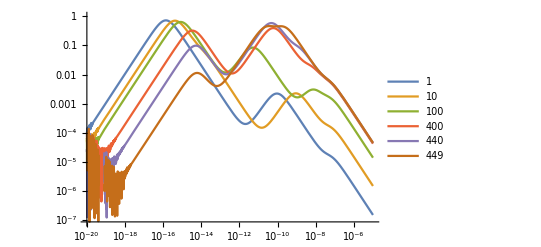

```mathematica
LogLogPlot[{imk2thickness[x,1],imk2thickness[x,10],imk2thickness[x,100],imk2thickness[x,400],imk2thickness[x,440],imk2thickness[x,449]},{x,10^-20,10^-5},PlotLegends->{1,10,100,400,440,449}]
```

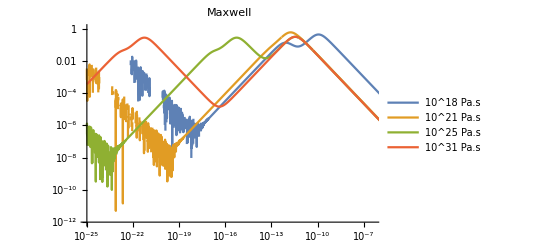

```mathematica
LogLogPlot[{imk2mantle[x,10^10,10^15],imk2mantle[x,10^10,10^18],imk2mantle[x,10^10,10^21],imk2mantle[x,10^10,10^24]},{x,10^-25,10^-5},PlotLabel->"Maxwell",PlotLegends->{"10^15 Pa.s","10^18 Pa.s","10^21 Pa.s","10^24 Pa.s"},PlotRange->{{10^-25,19^-5},{10^-12,1}}]
```

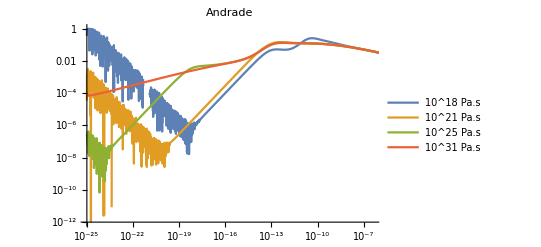

```mathematica
LogLogPlot[{imk2mantle[x,10^10,10^18],imk2mantle[x,10^10,10^21],imk2mantle[x,10^10,10^25],imk2mantle[x,10^10,10^31]},{x,10^-25,10^-5},PlotLabel->"Andrade",PlotLegends->{"10^18 Pa.s","10^21 Pa.s","10^25 Pa.s","10^31 Pa.s"},PlotRange->{{10^-25,19^-5},{10^-12,1}}]
```

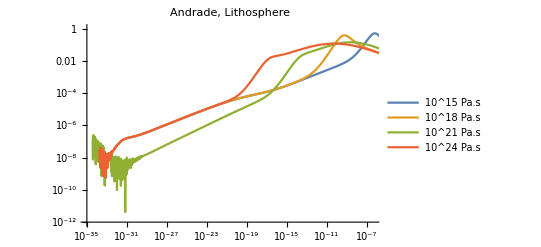

```mathematica
LogLogPlot[{imk2mantle[x,10^10,10^15],imk2mantle[x,10^10,10^18],imk2mantle[x,10^10,10^21,2*10^-12,.3],imk2mantle[x,10^10,10^24]},{x,10^-35,10^-5},PlotLabel->"Andrade, Lithosphere",PlotLegends->{"10^15 Pa.s","10^18 Pa.s","10^21 Pa.s","10^24 Pa.s"},PlotRange->{{10^-35,19^-5},{10^-12,1}}]
```

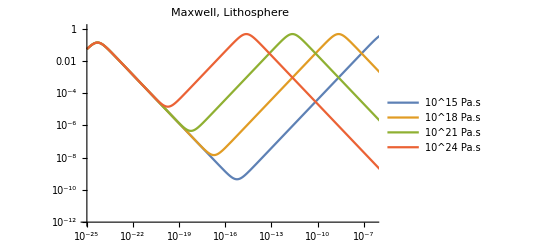

```mathematica
LogLogPlot[{imk2mantle[x,10^10,10^15],imk2mantle[x,10^10,10^18],imk2mantle[x,10^10,10^21],imk2mantle[x,10^10,10^24]},{x,10^-25,10^-5},PlotLabel->"Maxwell, Lithosphere",PlotLegends->{"10^15 Pa.s","10^18 Pa.s","10^21 Pa.s","10^24 Pa.s"},PlotRange->{{10^-25,19^-5},{10^-12,1}}]
```

```mathematica
myfunc[om_]:= imk2mantle[om,10^10,10^21]
```

```mathematica
N[n]
```

0.0000415555

```mathematica
torque[10^-50,hans,myfunc]
```

-2.6966×10^-8

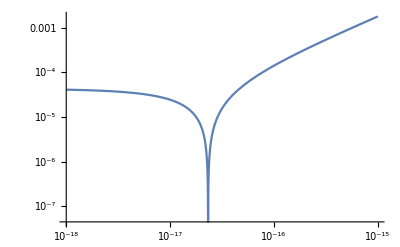

```mathematica
LogLogPlot[Abs[torque[10^-11+x,hans,myfunc,10^-11]],{x,10^-18,10^-15}]
```

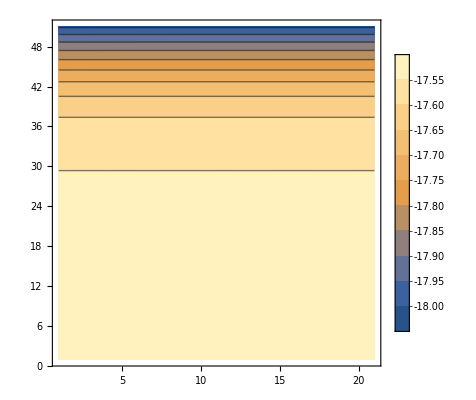

```mathematica
findomega[mantlemu_,mantleeta_]:=Module[{tempfunc,ohm,err},
tempfunc[myohm_]:=imk2mantle[myohm,mantlemu,mantleeta];
ohm=powerLawSolve[tempfunc,10^-15,3*10^-6];
err = powerLawCheck[tempfunc,ohm,3*10^-6];
{ohm,err}
]
ListContourPlot[Table[Log10[Abs[findomega[10^mu,10^eta][[1]]]],{eta,16,21,0.1},{mu,9,11,0.1}],PlotLegends->Automatic]
```

```mathematica
findomega[10^10,10^16.5][[2]]
```

-0.189398

```mathematica
Table[x+y,{x,0,1,.1},{y,0.01,0.02,0.001}]
```

{{0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02},{0.11,0.111,0.112,0.113,0.114,0.115,0.116,0.117,0.118,0.119,0.12},{0.21,0.211,0.212,0.213,0.214,0.215,0.216,0.217,0.218,0.219,0.22},{0.31,0.311,0.312,0.313,0.314,0.315,0.316,0.317,0.318,0.319,0.32},{0.41,0.411,0.412,0.413,0.414,0.415,0.416,0.417,0.418,0.419,0.42},{0.51,0.511,0.512,0.513,0.514,0.515,0.516,0.517,0.518,0.519,0.52},{0.61,0.611,0.612,0.613,0.614,0.615,0.616,0.617,0.618,0.619,0.62},{0.71,0.711,0.712,0.713,0.714,0.715,0.716,0.717,0.718,0.719,0.72},{0.81,0.811,0.812,0.813,0.814,0.815,0.816,0.817,0.818,0.819,0.82},{0.91,0.911,0.912,0.913,0.914,0.915,0.916,0.917,0.918,0.919,0.92},{1.01,1.011,1.012,1.013,1.014,1.015,1.016,1.017,1.018,1.019,1.02}}

```mathematica
AbsoluteTiming[imk2[om]/.om->{10^-4,10^-5,10^-6,10^-7,10^-8,10^-9,10^-3,10^-10,10^-11,10^-2,10^-12,10^-13}]
```

{49.5993,{2.333×10^-7,2.333×10^-6,0.00002333,0.000233299,0.00233237,0.0229136,2.333×10^-8,0.214886,0.645204,2.333×10^-9,0.0910028,0.00913778}}

```mathematica
AbsoluteTiming[res = imk2[x]; res/.x->{10^-4,10^-5,10^-6,10^-7,10^-8,10^-9,10^-3,10^-10,10^-11,10^-2,10^-12,10^-13}]
```

{53.7204,{2.333×10^-7,2.333×10^-6,0.00002333,0.000233299,0.00233237,0.0229136,2.333×10^-8,0.214886,0.645204,2.333×10^-9,0.0910028,0.00913778}}

```mathematica
2*1.1*n - Range[-10,10]*n
```

{0.0000806878,0.0000740741,0.0000674603,0.0000608466,0.0000542328,0.000047619,0.0000410053,0.0000343915,0.0000277778,0.000021164,0.0000145503,7.93651×10^-6,1.32275×10^-6,-5.29101×10^-6,-0.0000119048,-0.0000185185,-0.0000251323,-0.000031746,-0.0000383598,-0.0000449735,-0.0000515873}

```mathematica
myim[3]
```

7.77666×10^-12

```mathematica
imk2[10^-5]
```

2.333×10^-6

```mathematica
myx = x/.FindRoot[imk2twolayerfitconstraint[n,x]-0.015,{x,.1}]
```

0.0000663169

```mathematica
myim[om_]:= imk2andrade[om]
myimM[om_]:= imk2twolayerfitconstraint[om,myx]
```

```mathematica
myim[2Pi/10^5]
```

0.0100472

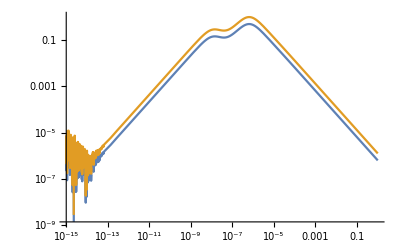

```mathematica
LogLogPlot[{imk2twolayerfitconstraint[x,myx],-2*imk2twolayerfitconstraint[-x,myx]},{x,10^-15,1}]
```

```mathematica
imk2twolayerandrade[n]
```

0.013721

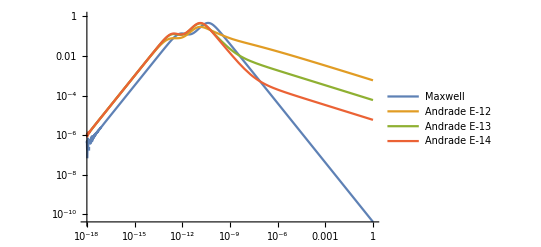

```mathematica
LogLogPlot[{imk2twolayer[x],imk2twolayerandrade[x,10^-12],imk2twolayerandrade[x,10^-13],imk2twolayerandrade[x,10^-14]},{x,10^-18,1},PlotLegends->{"Maxwell","Andrade E-12","Andrade E-13", "Andrade E-14"}]
```

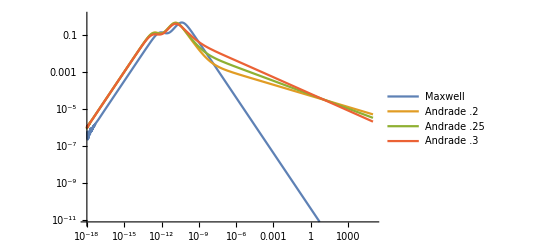

```mathematica
LogLogPlot[{imk2twolayer[x],imk2twolayerandrade[x,10^-13,.2],imk2twolayerandrade[x,10^-13,.25],imk2twolayerandrade[x,10^-13,.3]},{x,10^-18,10^5},PlotLegends->{"Maxwell","Andrade .2","Andrade .25", "Andrade .3"}]
```

```mathematica
Log10[imk2andrade[10^-1,10^-13,.3]/imk2andrade[10^4,10^-13,.3]]/5
```

0.299961

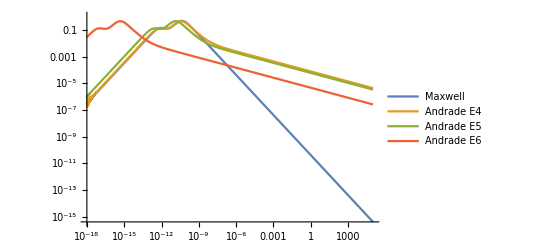

```mathematica
LogLogPlot[{imk2twolayer[x],imk2twolayerandrade[x,10^-13,.25,7*10^4],imk2twolayerandrade[x,10^-13,.25,7*10^5],imk2twolayerandrade[x,10^-13,.25,7*10^6]},{x,10^-18,10^5},PlotLegends->{"Maxwell","Andrade E4","Andrade E5", "Andrade E6"}]
```

```mathematica
FindMaximum[imk2twolayer[x],x]
```

{4.15941×10^-11,{x→1.}}

```mathematica
n
```

1/151200

```mathematica
findzero[hans, myim, n]
```

```mathematica
n
```

1/151200

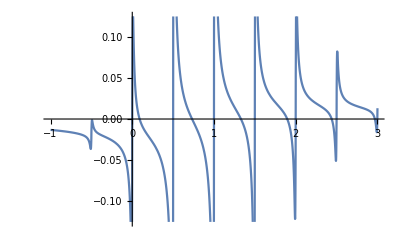

```mathematica
Plot[torque[(1+x)*n,hansp4,myim,n],{x,-1,3}]
```

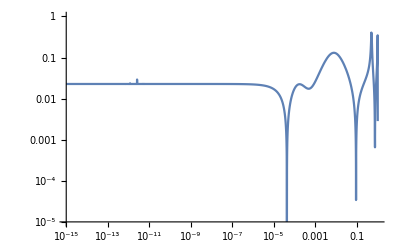

```mathematica
LogLogPlot[Abs[torque[(1+x)*n,hansp4,myim,n]],{x,10^-15,1},PlotRange->{{10^-15,1},{10^-5,10^0}}]
```

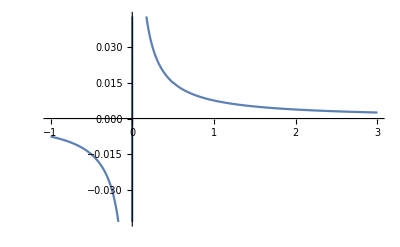

```mathematica
Plot[torque[(1+x)*n,hans,myim,n],{x,-1,3}]
```

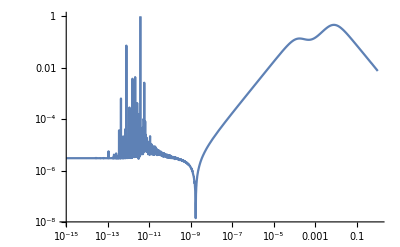

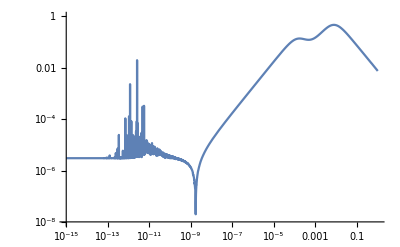

```mathematica
LogLogPlot[Abs[torque[(1+x)*n,hans,myim,n]],{x,10^-15,1},PlotRange->{{10^-15,1},{10^-8,10^0}}]
```

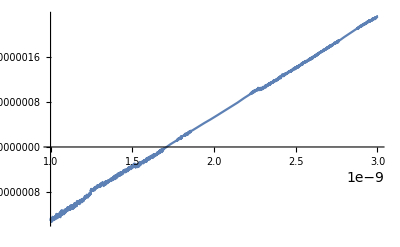

```mathematica
Plot[torque[(1+x)*n,hans,myim,n],{x,10^-9,.3*10^-8}]
```

```mathematica
torque[(1+1.000001)*n,hans,n]
```

0.225383

```mathematica
tor[x_]:= torque[(1+x)*n,hans,n]
```

```mathematica
FindRoot[tor[a],{a,10^-11}]
```

FindRoot::nlnum: The function value {0.+1.00013 0.0000415555[{0.00132977,0.00128822,0.00124666,0.00120511,0.00116355,0.001122,0.00108044,«37»,-0.000498666,-0.000540221,-0.000581776,-0.000623332,-0.000664887,-0.000706443,«11»}]} is not a list of numbers with dimensions {1} at {a} = {1.×10^-11}.

FindRoot[tor[a],{a,1/10^11}]

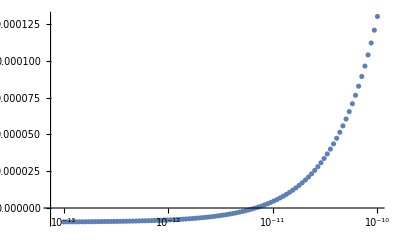

```mathematica
DecentLogLinearPlot[tor,-13,-10,100]
```

```mathematica
FindRoot[imk2twolayerfitconstraint[x]-0.015,{x,1}]
```

{x→0.000782754}

```mathematica
FindRoot[imk2twolayerfitconstraint[x]-0.015,{x,1}]
```

{x→0.0144092}

```mathematica
x/.findzero[hans,imk2twolayer,x]
```

6.81208×10^-12

```mathematica
myx = x/.FindRoot[imk2twolayerfitconstraint[10^-5,x]-0.015,{x,10^-2}]
```

0.000275583

```mathematica
tor[ohm_] := Module[{x},imk2twolayerfitconstraint[ohm,myx]]
```

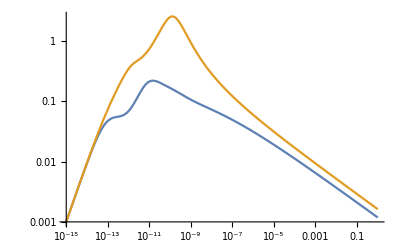

```mathematica
LogLogPlot[{myim[x],-myim[-x],myim[-x]},{x,10^-15,1}]
```

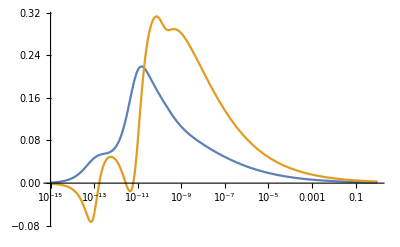

```mathematica
LogLinearPlot[{myim[x],myim[-x]},{x,10^-15,1}]
```

```mathematica
LogLogPlot[{Abs[torque[x+n,hansp4[[2]],tor]],Abs[torque[x+n,hans,tor]],imk2twolayerfitconstraint[x,myx]},{x,10^-15,1},PlotLegends->{"Total torque,e=0.4","Total torque, e=0.0041","Im[k2]"}]
```

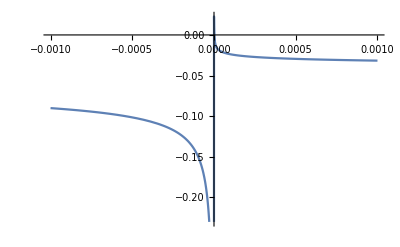

```mathematica
Plot[torque[(x+1)n,hansp4,myim],{x,-.001,.001}]
```

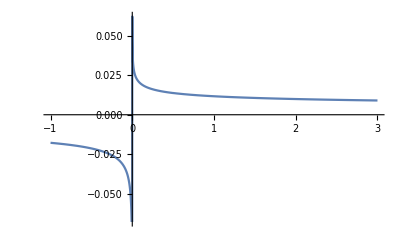

```mathematica
Plot[torque[(x+1)n,hans,myim],{x,-1,3}]
```

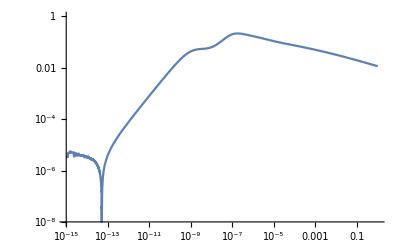

```mathematica
LogLogPlot[Abs[torque[(x+1)n,hans,myim]],{x,10^-15,1}]
```

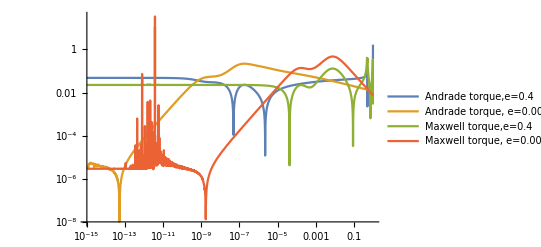

```mathematica
LogLogPlot[{Abs[torque[(x+1)n,hansp4,myim]],Abs[torque[(x+1)n,hans,myim]],Abs[torque[(x+1)n,hansp4,myimM]],Abs[torque[(x+1)n,hans,myimM]]},{x,10^-15,1},PlotLegends->{"Andrade torque,e=0.4","Andrade torque, e=0.0041","Maxwell torque,e=0.4","Maxwell torque, e=0.0041"},PlotRange->All]
```

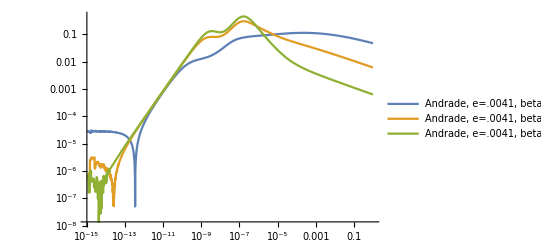

```mathematica
myim11[om_]:= imk2twolayerandrade[om,10^-11]
myim12[om_]:= imk2twolayerandrade[om,10^-12]
myim13[om_]:= imk2twolayerandrade[om,10^-13]
LogLogPlot[{Abs[torque[(x+1)n,hans,myim11]],Abs[torque[(x+1)n,hans,myim12]],Abs[torque[(x+1)n,hans,myim13]]},{x,10^-15,1},PlotLegends->{"Andrade, e=.0041, beta=10^-11","Andrade, e=.0041, beta=10^-12","Andrade, e=.0041, beta=10^-13"},PlotRange->All]
```

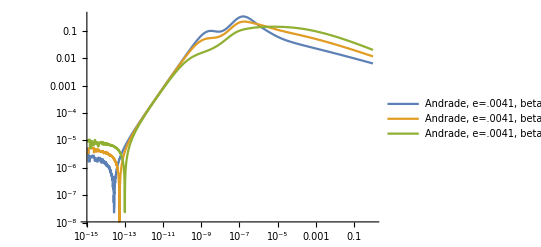

```mathematica
myim2[om_]:= imk2twolayerandrade[om,2*10^-12,.2]
myim25[om_]:= imk2twolayerandrade[om,2*10^-12,.25]
myim3[om_]:= imk2twolayerandrade[om,2*10^-12,.3]
LogLogPlot[{Abs[torque[(x+1)n,hans,myim2]],Abs[torque[(x+1)n,hans,myim25]],Abs[torque[(x+1)n,hans,myim3]]},{x,10^-15,1},PlotLegends->{"Andrade, e=.0041, beta=2*10^-12, alpha=.2","Andrade, e=.0041, beta=2*10^-12, alpha=.25","Andrade, e=.0041, beta=2*10^-12, alpha=.3"},PlotRange->All]
```

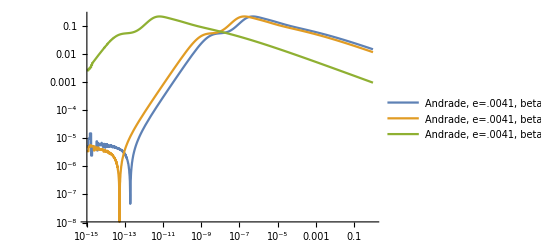
{686.975,-Graphics-}

```mathematica
AbsoluteTiming[myim4[om_]:= imk2twolayerandrade[om,2*10^-12,.25,7*10^4];
myim5[om_]:= imk2twolayerandrade[om,2*10^-12,.25,7*10^5];
myim6[om_]:= imk2twolayerandrade[om,2*10^-12,.25,7*10^6];
LogLogPlot[{Abs[torque[(x+1)n,hans,myim4]],Abs[torque[(x+1)n,hans,myim5]],Abs[torque[(x+1)n,hans,myim6]]},{x,10^-15,1},PlotLegends->{"Andrade, e=.0041, beta=2*10^-12, alpha=.25, E_b = 7*10^4","Andrade, e=.0041, beta=2*10^-12, alpha=.25, E_b = 7*10^5","Andrade, e=.0041, beta=2*10^-12, alpha=.25, E_b = 7*10^6"},PlotRange->All]]
```

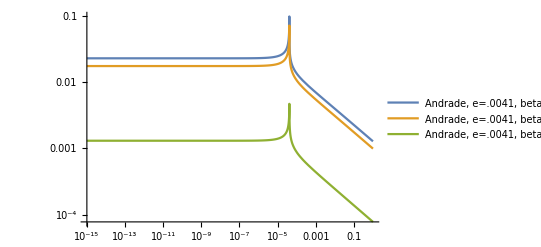
{597.443,-Graphics-}

```mathematica
AbsoluteTiming[tor= Simplify[Abs[torqueAndrade[om,hans,2*10^-12,.25,eg]]];myt1 = tor/.eg->7*10^4;
myt2 = tor/.eg->7*10^5;
myt3 = tor/.eg->7*10^6;
LogLogPlot[{myt1/.om->x,myt2/.om->x,myt3/.om->x},{x,10^-15,1},PlotLegends->{"Andrade, e=.0041, beta=2*10^-12, alpha=.25, E_b = 7*10^4","Andrade, e=.0041, beta=2*10^-12, alpha=.25, E_b = 7*10^5","Andrade, e=.0041, beta=2*10^-12, alpha=.25, E_b = 7*10^6"},PlotRange->All]]
```

```mathematica
FindRoot[torque[x+n,hans,tor]-imk2twolayerfitconstraint[10^-11,myx],{x,10^-11}]
```

{x→5.02618×10^-12}

```mathematica
5*Exp[3/2*(1/{1,2,3,4}-1/2.3)]
```

{11.6728,5.51385,4.29419,3.78961}

### Timing Testing

```mathematica
torqueAndrade[(10^-14+1)n,hans]//RuntimeTools`Profile
```

-3.60053×10^-6

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torqueAndrade[(x+1)n,hans]],{x,10^-15,1}]]
```

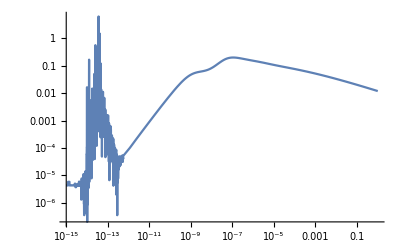
```mathematica
{1398.800016,-Graphics-}(* for 3 layers *)
```

```mathematica
tqa[x_] := Abs[torqueAndrade[(1+x)*n,hans]]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

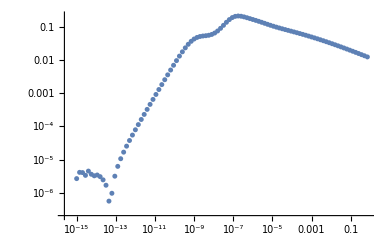
{677.763,-Graphics-}

```mathematica
AbsoluteTiming[DecentLogLogPlot[tqa,-15,0,100]]
```

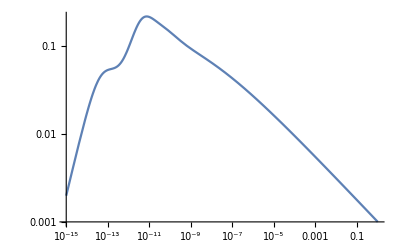
{164.198,-Graphics-}

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torqueAndrade[x+n,hans]],{x,10^-15,1}]]
```

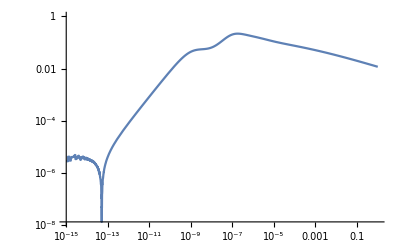
{339.22,-Graphics-}

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torqueAndrade[(x+1)n,hans]],{x,10^-15,1}]]
```

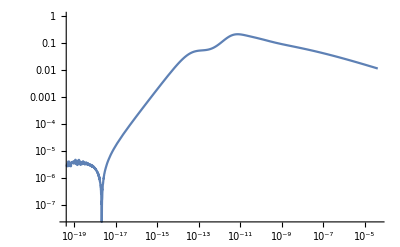
{359.13,-Graphics-}

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torqueAndrade[x+n,hans]],{x,n*10^-15,n}]]
```

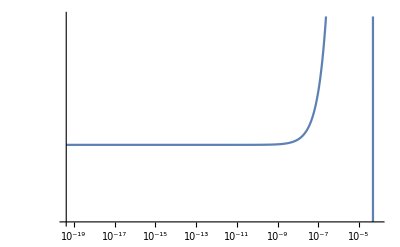
{273.909,-Graphics-}

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torqueAndrade[x,hans]],{x,n*10^-15,2n}]]
```

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torqueAndrade[(x+1)n,hans]],{x,10^-15,1}]]
```

{216.826,-Graphics-}

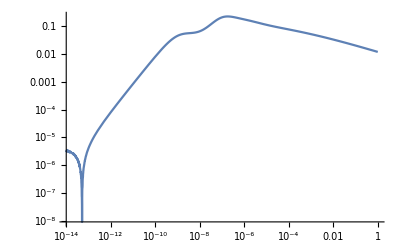
{169.817,-Graphics-}

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torqueAndrade[(x+1)n,hans]],{x,10^-14,1}]]
```

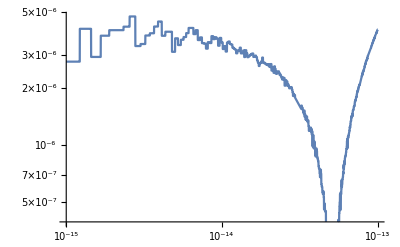
{539.544,-Graphics-}

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torqueAndrade[(x+1)n,hans]],{x,10^-15,10^-13}]]
```

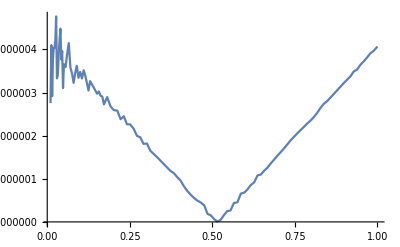
{40.0267,-Graphics-}

```mathematica
AbsoluteTiming[Plot[Abs[torqueAndrade[(x+1)n,hans]],{x,10^-15,10^-13}]]
```

```mathematica
AbsoluteTiming[torqueAndrade[(10^-15+1)n,hans]]
```

{614.104,-7.84324×10^-7}

```mathematica
AbsoluteTiming[torqueAndrade[(.99)n,hans]]
```

{395.313,-0.0424612}

```mathematica
AbsoluteTiming[torqueAndrade[(1+10^-3)n,hans]]
```

{631.328,0.0438291}

```mathematica
AbsoluteTiming[torqueAndrade[(x+1)n,hans]/.x->{10^-15,10^-14,10^-13,10^-12}]
AbsoluteTiming[FindRoot[torqueAndrade[(x+1)n,hans],{x,10^-12}]]
```

$Aborted

$Aborted

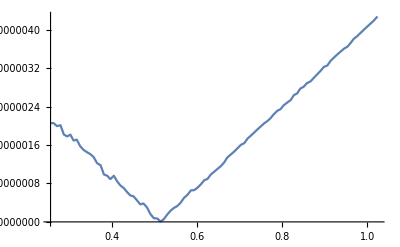
{37.8624,-Graphics-}

```mathematica
AbsoluteTiming[a=x/.FindRoot[torqueAndrade[(x+1)n,hans],{x,10^-13}];Plot[Abs[torqueAndrade[(x+1)n,hans]],{x,a/2,2*a}]]
```

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torqueAndrade[(x+1)n,hans]],{x,10^-15,1}]]
```

{248.629,-Graphics-}

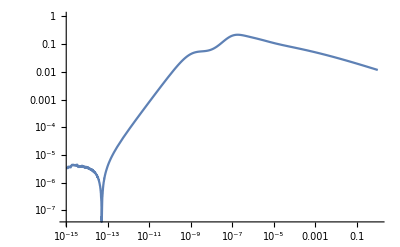
{122.174,-Graphics-}

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torqueAndrade[(x+1)n,hans]],{x,10^-15,1}]]
```

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torqueAndrade[(x+1)n,hans]],{x,10^-15,1}]]
```

{121.338,-Graphics-}

```mathematica
AbsoluteTiming[FindRoot[torqueAndrade[(x+1)n,hans],{x,10^-10}]]
```

{18.5747,{x→5.15272×10^-14}}

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torque[(x+1)n,hans,myim]],{x,10^-15,1}]]
```

{249.692,-Graphics-}

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torque[(x+1)n,hans5,myim]],{x,10^-15,1}]]
```

{118.27,-Graphics-}

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torque[(x+1)n,hans10,myim]],{x,10^-15,1}]]
```

{145.759,-Graphics-}

```mathematica
AbsoluteTiming[LogLogPlot[Abs[torque[(x+1)n,hans20,myim]],{x,10^-15,1}]]
```

{198.47,-Graphics-}

```mathematica
AbsoluteTiming[myt = Evaluate[Simplify[Abs[torque[(x+1)n,hans,myim]]]]]
```

{127.457,Abs[9.44195×10^-128 Im[(1^1.25 11(1))/1]+58+23 1]}
 |  |  |  |

```mathematica
AbsoluteTiming[LogLogPlot[myt/.x->varx,{varx,10^-15,1}]]
```

{915.621,-Graphics-}

```mathematica
AbsoluteTiming[myt = Simplify[Abs[torque[(x+1)n,hans,myim]]]]
```

{140.31,Abs[9.44195×10^-128 Im[(1^1.25 11(1))/1]+58+23 1]}
 |  |  |  |

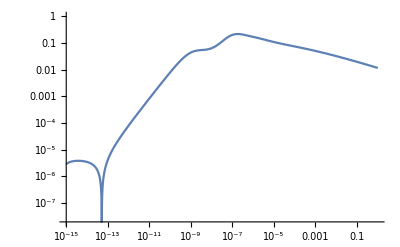
{24.3247,-Graphics-}

```mathematica
AbsoluteTiming[LogLogPlot[myt/.x->varx,{varx,10^-15,1}]]
```

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^0.25 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^0.25 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

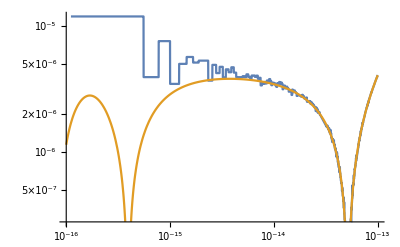

```mathematica
LogLogPlot[{Abs[torque[(varx+1)n,hans,myim]],myt/.x->varx},{varx,10^-16,10^-13}]
```

```mathematica
AbsoluteTiming[torque[(varx+1)n,hans,myim]/.varx->{10^-16,10^-15,10^-14}]
```

{8.0159,{-0.000612625,-2.34701×10^-6,-3.60736×10^-6}}

```mathematica
AbsoluteTiming[myt/.x->{10^-16,10^-15,10^-14}]
```

{0.0669481,{1.13812×10^-6,2.85976×10^-6,3.44252×10^-6}}

```mathematica
MaxwellMu[myomega_,mymu_,myeta_]:= mymu/(1+mymu/(I*myeta*myomega))
```

```mathematica
AndradeMu[myomega_,mymu_,eta_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374]:=
(*This uses equations 2,3,7,8,9,10 from Bierson&Nimmo 2016, corrected by Correia eq 64 for negative ohm*)
Module[{j1,j2,mubar,ohm,bigx},
bigx = (2Pi/myomega)*Exp[eb/8.3145*(1/temp-1/tempr)];
ohm = Abs[2Pi/bigx];
j1 = 1/mymu+beta*ohm^-alpha*Gamma[alpha+1]*Cos[alpha*Pi/2];
j2 = beta*ohm^-alpha*Gamma[alpha+1]*Sin[alpha*Pi/2]+1/(ohm*eta);
mubar = Simplify[Sign[myomega]/(j1-I*j2)]
]
imk2andrade[myomega_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5,3.5,3.5}10^3;
mys=     {1350,1400,1450,1600,1700,1800} 10^3;
mylens=Length[mys];
mymu = {40,20,5,4,3,2}10^9;
myeta = {1000,80,50,5,4,3}10^18;
(*myrho={5,3.5}10^3;
mys=     {1400,1800} 10^3;
mylens=Length[mys];
mymu = {40,4}10^9;
myeta = {1000,3}10^18;*)
mymubar = AndradeMu[myomega,mymu,myeta,beta,alpha,eb,temp,tempr];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
```

```mathematica
AbsoluteTiming[AndradeMu[(1+10^-5)n,40*10^-9,10^21]]
```

{0.0001686,4.×10^-8+1.04017×10^-26 ⅈ}

```mathematica
AbsoluteTiming[MaxwellMu[(1+10^-5)n,40*10^-9,10^21]]
```

{0.0000815,1/(25000000 (1-(189 ⅈ)/(62500625000000000000000000 π)))}

```mathematica
AbsoluteTiming[40*10^-9/(1+40*10^-9/(I*10^21*(1+10^-5)n))]
```

{0.0001283,1/(25000000 (1-(189 ⅈ)/(62500625000000000000000000 π)))}

```mathematica
AbsoluteTiming[For[j=0,j<1000,j++,AndradeMu[(1+10^-5)n,{40,20,5,4,3,2}10^9,{1000,80,50,5,4,3}10^18;]]]
```

{0.116587,Null}

```mathematica
AbsoluteTiming[MaxwellMu[(1+10^-5)n,{40,20,5,4,3,2}10^9,{1000,80,50,5,4,3}10^18]]
```

{0.0001144,{40000000000/(1-(189 ⅈ)/(62500625 π)),20000000000/(1-(189 ⅈ)/(10000100 π)),5000000000/(1-(189 ⅈ)/(25000250 π)),4000000000/(1-(756 ⅈ)/(12500125 π)),3000000000/(1-(567 ⅈ)/(10000100 π)),2000000000/(1-(126 ⅈ)/(2500025 π))}}

```mathematica
AbsoluteTiming[torqueAndrade[(10^-15+1)n,hans]]
```

{642.268,-7.84324×10^-7}

```mathematica
AbsoluteTiming[torqueAndrade[(10^-15+1)n,hans]]
```

{658.279,-7.84324×10^-7}

```mathematica
AbsoluteTiming[torqueAndrade[(10^-15+1)n,hans]]
```

{454.222,-2.7664×10^-6}

```mathematica
AbsoluteTiming[torqueAndrade[(10^-15+1)n,hans]]
```

{650.126,-7.84324×10^-7}

```mathematica
AbsoluteTiming[imk2andrade[(10^-15+1)n]]
```

{0.0075046,0.0110798}

```mathematica
AbsoluteTiming[imk2andrade[(10^-15+1)n]]
```

{0.0089785,0.0110798}

```mathematica
AbsoluteTiming[torqueAndrade[(10^-15+1)n,hans]]
```

{0.43796,-2.18815×10^-6}

```mathematica
tqa[x_]:=torqueAndrade[(x+1)n,hans]
```

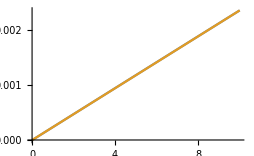
{97.3612,-Graphics-}

```mathematica
AbsoluteTiming[Plot[{tqa[x],x*(tqa[10^-10]-tqa[10^-15])/(10^-10-10^-15)+tqa[10^-15]},{x,10^-14,10^-10}]]
```

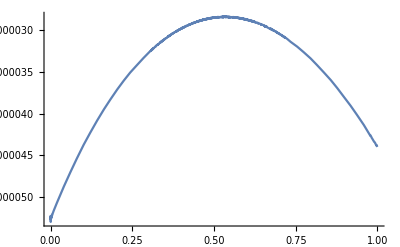
{1425.69,-Graphics-}

```mathematica
AbsoluteTiming[Plot[{tqa[x]-x*(tqa[10^-10]-tqa[10^-15])/(10^-10-10^-15)+tqa[10^-15]},{x,10^-14,10^-10}]]
```

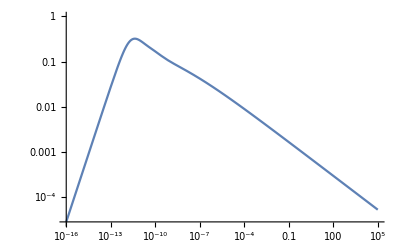
{1.64113,-Graphics-}

```mathematica
AbsoluteTiming[LogLogPlot[imk2andrade[x],{x,10^-16,10^5}]]
```

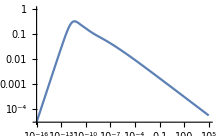
{1.66084,-Graphics-}

```mathematica
AbsoluteTiming[LogLogPlot[imk2andrade[x],{x,10^-16,10^5}]]
```

```mathematica
AbsoluteTiming[torqueAndrade[(10^-15+1)n,hans]]
```

{0.466338,-2.18815×10^-6}

```mathematica
AbsoluteTiming[torqueAndrade[(10^-15+1)n,hans]]
```

{0.460764,-2.18815×10^-6}

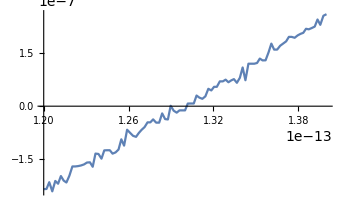
{44.9307,-Graphics-}

```mathematica
AbsoluteTiming[Plot[torqueAndrade[(x+1)n,hans],{x,1.2*10^-13,.14*10^-12}]]
```

```mathematica
AbsoluteTiming[FindRoot[torqueAndrade[(x+1)n,hans],{x,1.2*10^-13}]]
```

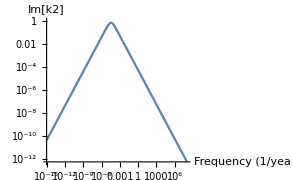

```mathematica
LogLogPlot[imk2Talk[om/(Pi*10^7)],{om,10^-15,10^8},AxesLabel->{"Frequency (1/year)","Im[k2]"}]
```

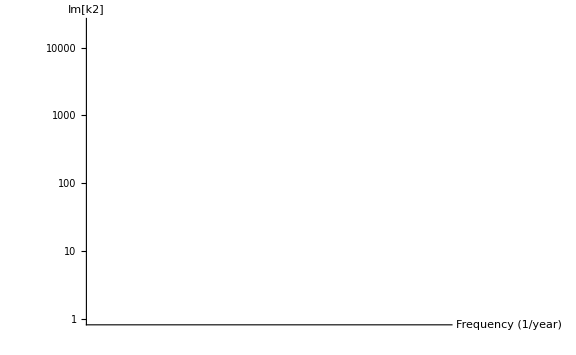

```mathematica
Show[%112,ImageSize->Large,PlotRange->{{10^-8,10^5},{10^-8,10^1}}]
```

```mathematica
Show[%113,PlotLabel->None,LabelStyle->{18,GrayLevel[0]},PlotRange->{{10^-8,10^5},{10^-8,10^1}}]
```

-Graphics-

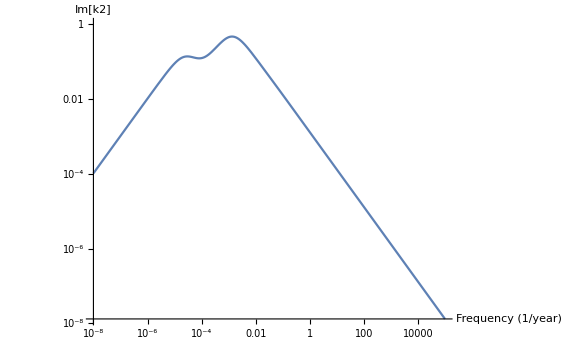

```mathematica
Show[LogLogPlot[imk2Talk[om/(Pi*10^7)],{om,10^-8,10^5},AxesLabel->{"Frequency (1/year)","Im[k2]"}],ImageSize->Large,PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

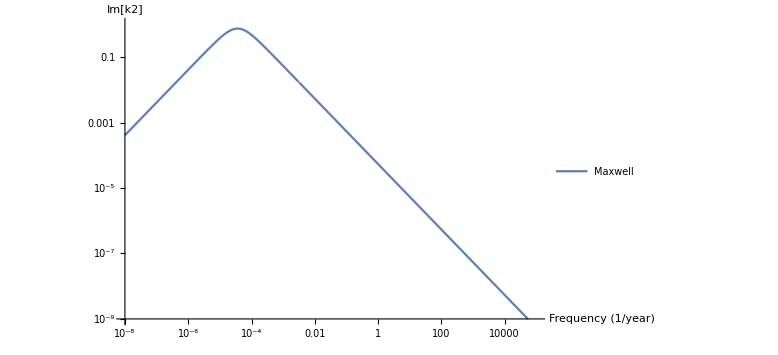

```mathematica
Show[LogLogPlot[imk2Talk[om/(Pi*10^7)],{om,10^-8,10^5},PlotLegends->{"Maxwell"}, AxesLabel->{"Frequency (1/year)","Im[k2]"},PlotRange->{{10^-8,10^5},{10^-9,1}}],ImageSize->Large,PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

```mathematica
imk2andradeTalk[myomega_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5}10^3;
mys=     {1000,1100,1200,1300,1400,1500,1600,1700,1800,1850} 10^3;
mylens=Length[mys];
mymu = {40,40,40,40,20,5,3,3,3,60}10^9;
myeta = {1000,1000,1000,1000,100,10,5,3,3,10}10^18;
(*myrho={5,3.5}10^3;
mys=     {1400,1800} 10^3;
mylens=Length[mys];
mymu = {40,4}10^9;
myeta = {1000,3}10^18;*)
mymubar = AndradeMu[myomega,mymu,myeta,beta,alpha,eb,temp,tempr];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]

imk2Talk[myomega_] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5}10^3;
mys=     {1000,1100,1200,1300,1400,1500,1600,1700,1800,1850} 10^3;
mylens=Length[mys];
mymu = {40,40,40,40,20,5,3,3,3,60}10^9;
myeta = {1000,1000,1000,1000,100,10,5,3,3,10}10^18;
mymubar = mymu/(1+mymu/(I*myeta*myomega));
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
```

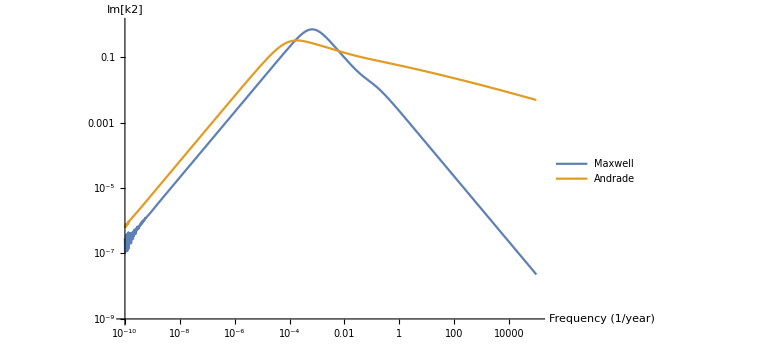

```mathematica
Show[LogLogPlot[{imk2Talk[om/(Pi*10^7)],imk2andradeTalk[om/(Pi*10^7)]},{om,10^-10,10^5},PlotLegends->{"Maxwell","Andrade"},AxesLabel->{"Frequency (1/year)","Im[k2]"},PlotRange->{{10^-10,10^5},{10^-9,1}}],ImageSize->Large,PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

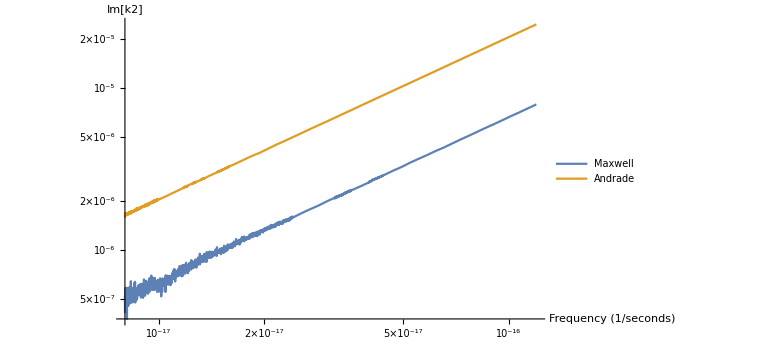

```mathematica
Show[LogLogPlot[{imk2Talk[om],imk2andradeTalk[om]},{om,.8*10^-17,1.2*10^-16},PlotLegends->{"Maxwell","Andrade"},AxesLabel->{"Frequency (1/seconds)","Im[k2]"}],ImageSize->Large,PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

```mathematica
powerLawCheck[imk2andradeTalk,powerLawSolve[imk2andradeTalk,10^-15,3*10^-6],3*10^-6]
```

-0.0042213

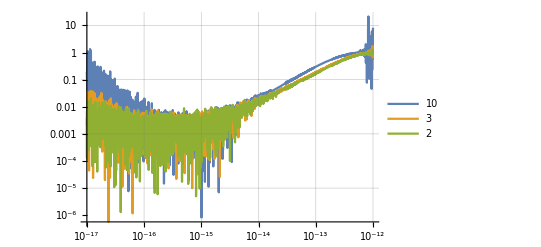

```mathematica
LogLogPlot[{Abs[imk2andradeTalk[powerLawSolve[imk2andradeTalk,x,3*10^-6,10]]/(3*10^-6)-1],Abs[imk2andradeTalk[powerLawSolve[imk2andradeTalk,x,3*10^-6,3]]/(3*10^-6)-1],Abs[imk2andradeTalk[powerLawSolve[imk2andradeTalk,x,3*10^-6,2]]/(3*10^-6)-1]},{x,10^-17,10^-12},GridLines->Automatic,PlotLegends->{"10","3","2"}]
```

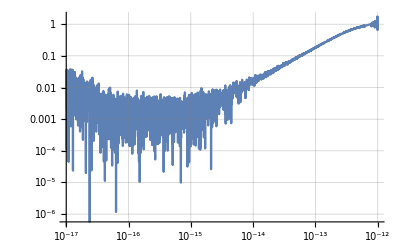

```mathematica
LogLogPlot[Abs[imk2andradeTalk[powerLawSolve[imk2andradeTalk,x,3*10^-6]]/(3*10^-6)-1],{x,10^-17,10^-12},GridLines->Automatic]
```

```mathematica
imk2andradeTalk[.5*10^-9/(Pi*10^7)]
```

3.28727×10^-6

```mathematica
AbsoluteTiming[FindRoot[imk2andradeTalk[x/(Pi*10^7)]-3*10^-6,{x,10^-16},AccuracyGoal->2]]
```

$Aborted

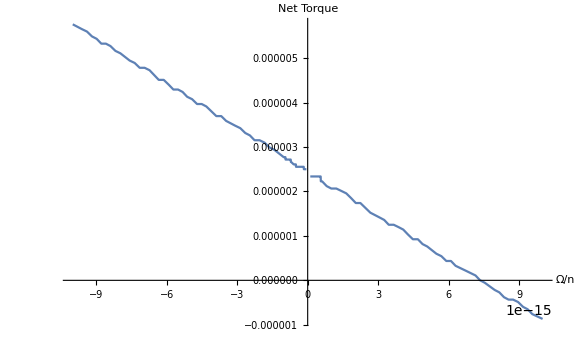

```mathematica
Plot[-torqueAndradeTalk[(1+om)*n,hans],{om,-.00000000000001,.00000000000001},AxesLabel->{"Ω/n","Net Torque"},ImageSize->Large,PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

```mathematica
torqueAndradeTalk[(1+.000000000001)*n,hans]
```

-0.000260404

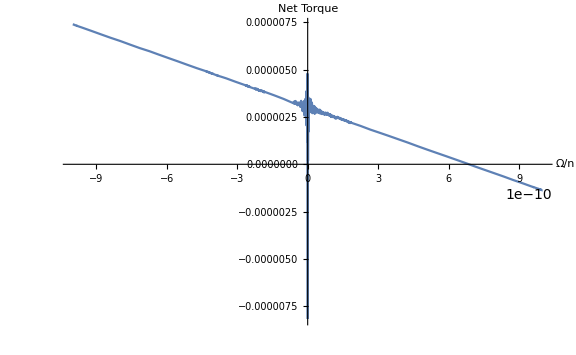

```mathematica
Plot[-torqueAndradeTalk[(1+om)*n,hans],{om,-.000000001,.000000001},AxesLabel->{"Ω/n","Net Torque"},ImageSize->Large,PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

```mathematica
blah[a_]:=NSolve[0==(torqueAndradeTalk[(1+a)*n,hans]-torqueAndradeTalk[(1-a)*n,hans])/(a+a)*(x+a)+torqueAndradeTalk[(1-a)*n,hans]]
```

```mathematica
Map[ blah,{10^-10,2*10^-10,3*10^-10,10^-11,1.1*10^-11,1.9*10^-11,3*10^-11}]
```

{{{x→7.74018×10^-11}},{{x→2.82043×10^-10}},{{x→9.18153×10^-11}},{{x→-3.15865×10^-13}},{{x→4.65297×10^-12}},{{x→7.98763×10^-11}},{{x→-6.42289×10^-12}}}

```mathematica
torqueAndradeTalk[(1+.5*10^-10)*n,hans]
```

-0.00923217

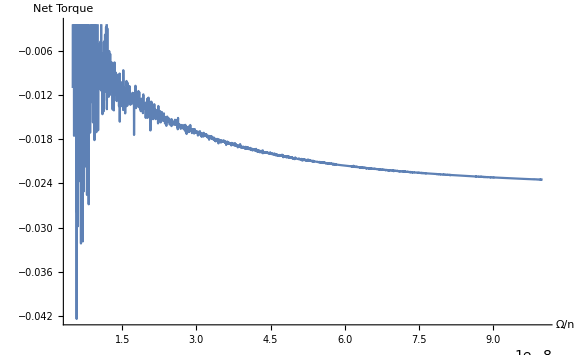

```mathematica
Plot[-torqueAndradeTalk[(1+om)*n,hans],{om,5*10^-9,10^-7},AxesLabel->{"Ω/n","Net Torque"},ImageSize->Large,PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

```mathematica
Finding  the  k2/Q for superrotation assuming k2/Q = 0.015 at orbital frequency and for a particular Andrade n (would be 1 for Maxwell)
```

```mathematica
Clear[Findk2];

Findk2[myhansens_,andrn_:0.25,obsk2_:0.015, myn_:2Pi/(42*60*60)]:= Module[{mykmax,myomegaks,myk2s,res},
mykmax = (Length[myhansens]-1)/2;
myomegaks = 2*myn - Range[-mykmax,mykmax]*myn;
myomegaks[[mykmax+3]] = res; (* temporarily gets rid of the 0 at the low frequency term *)
myk2s = obsk2*(Abs[myn/myomegaks])^andrn*Sign[myomegaks];
myk2s[[mykmax+3]] = res;
res/.FindRoot[0==Total[myhansens^2*myk2s],{res,10^-6}]
]
```

```mathematica
Clear[RecursiveHansenArrayWrapper,RecursiveHansenArray,NewcombArray];
RecursiveHansenArrayWrapper[kmax_,ecc_,sigmamax_:6]:=Module[{result,mypi,k},
result = Range[-kmax,kmax];
mypi[a_,b_,c_,d_]:= Pi;
Clear[array];
array = {};
For[k=-kmax, k ≤ kmax, k++,result[[k+kmax+1]] = RecursiveHansenArray[-3,2,k,ecc,kmax,sigmamax];];
result
]
RecursiveHansenArray[a_, b_, c_, ecc_, kmax_,sigmamax_:6]:= 
Module[{coef,coefpart,out,i},
coef = 0;
For[i=0, i≤ sigmamax, i++, coef+= ecc^(2*i)*NewcombArray[a,b,i+Max[0,c-b],i+Max[0,b-c]];];
coef  *= ecc^(Abs[c-b]);
coef
]
NewcombArray[a_,b_,c_,d_]:= 
Module[{v1,v2,v3,v4,v4func,res,loc},
loc = Position[array,{a,b,c,d}];
If[Length[loc]==0,
v4func[j_]:= ((-1)^j)*Binomial[3/2,j]*NewcombArray[a,b,c-j,d-j];
res = If[d<0,
0, (* d<0 *)
If[d == 0,(*d !< 0*)
If[c<0,(*d !< 0, d == 0*)
 0, (*d == 0, c < 0*)
If[c==0, (*d == 0*)
1,(*d == 0, c == 0*)
If[c==1, (*d == 0, c !< 1*) 
b-a/2,(*d == 0, c == 1*)
(2*(2*b-a)*NewcombArray[a,b+1,c-1,0]+(b-a)*NewcombArray[a,b+2,c-2,0])/(4c)(*d == 0, c > 1*)
] (*d == 0, c != 0, c !< 0*)
] (*d == 0, c !< 0*)
],
If[d > c,(*d != 0*)
NewcombArray[a,-b,d,c],(*d ≠ 0,d > c *)
v1 = -2*(2b+a)*NewcombArray[a,b-1,c,d-1];(*d ≠ 0, d !> c*)
v2 = (b-a)*NewcombArray[a,b-2,c,d-2];
v3 = (c-5d+4+4b+a)*NewcombArray[a,b,c-1,d-1];
v4 = Total[Map[v4func,Range[2,d]]]*2*(c-d+b);
(v1-v2-v3+v4)/(4d)
]
]
];
array= Append[array,{{a,b,c,d},res}],
res = array[[loc[[1,1]],2]];
];
res
]
```

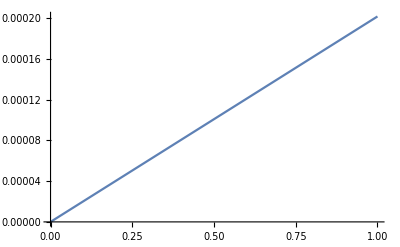

```mathematica
Plot[Findk2[hans,.25,x],{x,10^-5,1}]
```

```mathematica
12*0.0041^2*0.015
```

3.0258×10^-6

```mathematica
k2/Q = 3*10^-6 means that Q is around 10^5, maybe 3*10^5
```

```mathematica
{Findk2[hans,.25,10^-10]/10^-10,Findk2[hans,.25,10^-3]/10^-3,Findk2[hans,.25,10^0]/10^0}
```

{0.000201739,0.000201739,0.000201739}

```mathematica
.0041^2
```

0.00001681

```mathematica
Series[1/(1-5x^2),{x,0,5}]
```

1+5 x^2+25 x^4+O[x]^6

```mathematica
Series[RecursiveHansenArrayWrapper[16,e],{e,0,4}]
```

{O[e]^18,O[e]^17,O[e]^16,O[e]^15,O[e]^14,O[e]^13,O[e]^12,O[e]^11,O[e]^10,O[e]^9,O[e]^8,O[e]^7,O[e]^6,O[e]^5,-e^4/24+O[e]^5,-e^3/24+O[e]^5,0,-e+(3 e^3)/8+O[e]^5,1-(7 e^2)/2+(19 e^4)/16+O[e]^5,3 e-(69 e^3)/8+O[e]^5,(13 e^2)/2-(55 e^4)/3+O[e]^5,(295 e^3)/24+O[e]^5,(345 e^4)/16+O[e]^5,O[e]^5,O[e]^6,O[e]^7,O[e]^8,O[e]^9,O[e]^10,O[e]^11,O[e]^12,O[e]^13,O[e]^14}

```mathematica
{x^4/24+O[x]^5,
x^3/48+O[x]^5,
0,
-x/2+x^3/16+O[x]^5,
1-(5 x^2)/2-(7 x^4)/8+O[x]^5,
(7 x)/2-(123 x^3)/16+O[x]^5,
(17 x^2)/2-(115 x^4)/6+O[x]^5,
(845 x^3)/48+O[x]^5,
(533 x^4)/16+O[x]^5}
```

```mathematica
PolynomialReduce[x^10 (81/1280+(81 x^2)/2048+(17901 x^4)/573440+(385317 x^6)/18350080+(3720573 x^8)/293601280+(364190499 x^10)/58720256000+(7209874233 x^12)/5167382528000)^2,{x^8 (1/24+(7 x^2)/240+(29 x^4)/1440+(289 x^6)/24192+(5539 x^8)/967680+(18131 x^10)/13934592-(70899263 x^12)/41803776000)^2,x^6 (1/48+(11 x^2)/768+(247 x^4)/30720+(7529 x^6)/2211840+(19529 x^8)/49545216-(56274721 x^10)/39636172800-(4168023457 x^12)/1712282664960)^2,0,x^2 (-1/2+x^2/16+(73 x^4)/384+(2755 x^6)/18432+(27271 x^8)/294912+(9089933 x^10)/176947200+(110221571 x^12)/4246732800)^2,(1-(5 x^2)/2-(7 x^4)/8-(95 x^6)/72-(3257 x^8)/2304-(353503 x^10)/230400-(27340981 x^12)/16588800)^2,x^2 (7/2-(123 x^2)/16+(171 x^4)/128-(3921 x^6)/2048-(238349 x^8)/163840-(2131001 x^10)/1310720-(1900165961 x^12)/1101004800)^2},{x}]
```

Thread::tdlen: Objects of unequal length in {(38419984021627710796376776896/356389714838621645984447+(51982286455677338289 x^2)/5026705493943169)/26701842190679670784000000,61324105889389899586396221249111981/227711528519777214293017802667041076294303151135129600000000,«1»,-(1680235085647562385460«34»4578961937495159801493)/(3524477872642436530514«52»7762247339212800000000),0} «1» cannot be combined.

{{(38419984021627710796376776896/356389714838621645984447+(51982286455677338289 x^2)/5026705493943169)/26701842190679670784000000,61324105889389899586396221249111981/227711528519777214293017802667041076294303151135129600000000,(-85487204142787998173978559668564456271199305746789591104655990107928629248/207264665577144797265697664294392853705518740678955718279043872943325+(43973435911727455507549276597178554856977361510465301504 x^2)/90231570088802051448697733403886857055218443182195)/26701842190679670784000000,-168023508564756238546039919706418035834469295564830852474578961937495159801493/352447787264243653051409651789366174015083696819605183143840742482317231847762247339212800000000,0} {1747555687858176000000,73297798118062990295040000,1,18034739474595840000,275188285440000,1212211569623040000},-((6561 (-5049052740215626362618927332695858185530476272485858925708056717749627684374517086872697569280000-2655090520447552969147568525615074921442695491927336230506730643022580396525151373068418123038720000 x^2+3814342673531033547552911710025782520728041293863432237195064124348888958592676618066565917573120000 x^4+1525511857615740724478132968191480164084633280560077674670783537757351185375180513018187730124800000 x^6-109115359114655607659215135358891884450478472265094331540388196138325038900386765023076129505280000 x^8-259188956309520122426093509843463536703984226245035094419669598918055430852733691275089068153548800 x^10+137336233417680104266553455044054297775425433350115044629269163712768403310866962343363213989990400 x^12+313113347294528908895123208913719455786068132879076308631281493842058286649536512921420602807475200 x^14+188604827444068440833283286172924241007260009620113364768183480651704468023063142778750207132774400 x^16+267136299212179383888291741551165484114260629669285591106626415463407629655849241985530385352270400 x^18+127528316716285354982233457834157249502440250381607856171255076856263930082766722307827162534778408 x^20+35809658370122005068772997970440796136590827467630872996813415829334633523436939511838608859408393 x^22))/252507767250301729179684551301114855162312367939639814758069496466348392595105320285420930675507200000000)}

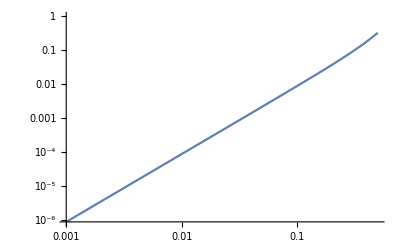

```mathematica
LogLogPlot[(1-RecursiveHansenArrayWrapper[3,ecc][[6]])/ecc^2-2.5,{ecc,0.001,0.5}]
```

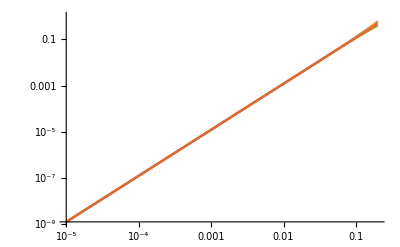

```mathematica
LogLogPlot[{Findk2[RecursiveHansenArrayWrapper[4,ecc],.25,.015]/(.015),Findk2[RecursiveHansenArrayWrapper[5,ecc],.25,.015]/(.015),(RecursiveHansenArrayWrapper[4,ecc][[8]]^2-RecursiveHansenArrayWrapper[4,ecc][[6]]^2),12ecc^2},{ecc,0.00001,0.2}]
```

```mathematica
To sum this up : Your superrotation rate (orbits per orbit) is just whatever frequency gives k2/Q = 12*e^2*k2_orb/Q_orb
```

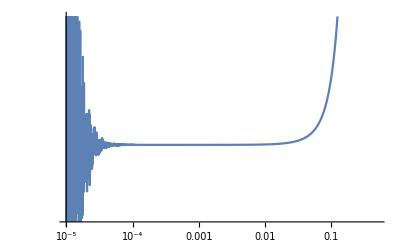

```mathematica
LogLogPlot[(Findk2[RecursiveHansenArrayWrapper[4,ecc],.25,.015]/(.015)-(RecursiveHansenArrayWrapper[4,ecc][[8]]^2-RecursiveHansenArrayWrapper[4,ecc][[6]]^2))/(ecc^4),{ecc,0.00001,0.5}]
```

```mathematica
(0.00204999569221725^2-0.014349470171360231^2-0.00014287958400041335^2)/0.9999579747527397^2
```

-0.000201742

```mathematica
hans[[33]]
```

0.999958

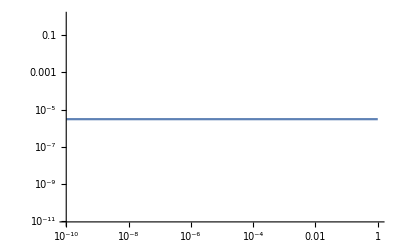

```mathematica
LogLogPlot[Findk2[hans,.25,.015,x],{x,10^-10,1}]
```

Takeaway : k2/Q for superrotation is 100% independent of the observed orbital frequency and 99.999999% independent of rheology. ALL that matters is the observed orbital k2/Q, and the superrotation k2/Q is linearly proportional to that. So in general the superrotation k2/Q is just the orbital k2/Q divided by 5000

```mathematica
Findk2[hans,1]
```

{2.08222×10^-152,7.11256×10^-148,2.43384×10^-143,8.34391×10^-139,2.86623×10^-134,9.86665×10^-130,3.40414×10^-125,1.17731×10^-120,4.08218×10^-116,1.41936×10^-111,4.94973×10^-107,1.73164×10^-102,6.07897×10^-98,2.14201×10^-93,7.57819×10^-89,2.69286×10^-84,9.61457×10^-80,3.45063×10^-75,1.24541×10^-70,4.52256×10^-66,1.65318×10^-61,6.08556×10^-57,2.25652×10^-52,8.42668×10^-48,3.16552×10^-43,1.19199×10^-38,4.45706×10^-34,1.61257×10^-29,5.19864×10^-25,1.03086×10^-20,0.,6.30372×10^-8,0.999916 res$66258,-3.08861×10^-6,-1.53109×10^-10,-7.35985×10^-15,-3.3226×10^-19,-1.42379×10^-23,-5.85683×10^-28,-2.33274×10^-32,-9.05362×10^-37,-3.44019×10^-41,-1.28441×10^-45,-4.72481×10^-50,-1.7162×10^-54,-6.16603×10^-59,-2.19436×10^-63,-7.74419×10^-68,-2.71284×10^-72,-9.44066×10^-77,-3.26592×10^-81,-1.12379×10^-85,-3.8482×10^-90,-1.31194×10^-94,-4.45468×10^-99,-1.50699×10^-103,-5.08067×10^-108,-1.70751×10^-112,-5.72183×10^-117,-1.91218×10^-121,-6.37415×10^-126}

3.02598×10^-6

```mathematica
Findk2[hans]
```

{(37 π)/75600,π/2100,π/2160,(17 π)/37800,(11 π)/25200,(2 π)/4725,(31 π)/75600,π/2520,(29 π)/75600,π/2700,π/2800,(13 π)/37800,π/3024,π/3150,(23 π)/75600,(11 π)/37800,π/3600,π/3780,(19 π)/75600,π/4200,(17 π)/75600,π/4725,π/5040,π/5400,(13 π)/75600,π/6300,(11 π)/75600,π/7560,π/8400,π/9450,π/10800,π/12600,π/15120,π/18900,π/25200,π/37800,π/75600,0}

```mathematica
torqueMaxwellTalk[myomega_,myhansens_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374,myn_:n]:=Module[{myomegaks,mykmax,myks,x,tempim},
mykmax = (Length[myhansens]-1)/2;
myomegaks = 2*myomega - Range[-mykmax,mykmax]*myn;
tempim[var_]:= imk2Talk[var];
myks = Map[tempim,myomegaks];
Print[myks]
]
torqueMaxwellTalk[10^-10,hans]
```

{1.37225×10^-9,1.41957×10^-9,1.47027×10^-9,1.52472×10^-9,1.58337×10^-9,1.6467×10^-9,1.71531×10^-9,1.78989×10^-9,1.87125×10^-9,1.96036×10^-9,2.05838×10^-9,2.16671×10^-9,2.28709×10^-9,2.42162×10^-9,2.57297×10^-9,2.7445×10^-9,2.94054×10^-9,3.16673×10^-9,3.43063×10^-9,3.7425×10^-9,4.11675×10^-9,4.57417×10^-9,5.14594×10^-9,5.88107×10^-9,6.86125×10^-9,8.2335×10^-9,1.02919×10^-8,1.37225×10^-8,2.05837×10^-8,4.11674×10^-8,0.0085534,-4.11678×10^-8,-2.05838×10^-8,-1.37225×10^-8,-1.02919×10^-8,-8.23352×10^-9,-6.86126×10^-9,-5.88108×10^-9,-5.14595×10^-9,-4.57417×10^-9,-4.11676×10^-9,-3.74251×10^-9,-3.43063×10^-9,-3.16674×10^-9,-2.94054×10^-9,-2.7445×10^-9,-2.57297×10^-9,-2.42162×10^-9,-2.28709×10^-9,-2.16671×10^-9,-2.05838×10^-9,-1.96036×10^-9,-1.87125×10^-9,-1.78989×10^-9,-1.71532×10^-9,-1.6467×10^-9,-1.58337×10^-9,-1.52472×10^-9,-1.47027×10^-9,-1.41957×10^-9,-1.37225×10^-9}

```mathematica
LPSC Abstract Figure
```

```mathematica
AbstractFigureOne[myomega_] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5}10^3;
mys=     {1800} 10^3;
mylens=Length[mys];
mymu = {40}10^9;
myeta = {1000}10^18;
mymubar = mymu/(1+mymu/(I*myeta*myomega));
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
AbstractFigureTwo[myomega_] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5}10^3;
mys=     {1800} 10^3;
mylens=Length[mys];
mymu = {40}10^9;
myeta = {1}10^18;
mymubar = mymu/(1+mymu/(I*myeta*myomega));
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
AbstractFigureThree[myomega_] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5,3.5}10^3;
mys=     {1550,1800} 10^3;
mylens=Length[mys];
mymu = {40,40}10^9;
myeta = {1,10^28}10^18;
mymubar = mymu/(1+mymu/(I*myeta*myomega));
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
AbstractFigureFour[myomega_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5}10^3;
mys=     {1800} 10^3;
mylens=Length[mys];
mymu = {40}10^9;
myeta = {1000}10^18;
mymubar = AndradeMu[myomega,mymu,myeta,beta,alpha,eb,temp,tempr];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
AbstractFigureFive[myomega_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5}10^3;
mys=     {1800} 10^3;
mylens=Length[mys];
mymu = {40}10^9;
myeta = {1}10^18;
mymubar = AndradeMu[myomega,mymu,myeta,beta,alpha,eb,temp,tempr];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
AbstractFigureSix[myomega_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5,3.5}10^3;
mys=     {1790,1800} 10^3;
mylens=Length[mys];
mymu = {40,40}10^9;
myeta = {1,10^28}10^18;
mymubar = MaxwellMu[myomega,mymu,myeta(*,beta,alpha,eb,temp,tempr*)];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
AbstractFigureSeven[myomega_] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5}10^3;
mys=     {1800} 10^3;
mylens=Length[mys];
mymu = {40}10^9;
myeta = {10^-3}10^18;
mymubar = mymu/(1+mymu/(I*myeta*myomega));
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]

(*height=4;*)
width = 3.125;
imagesize = {QuantityMagnitude[UnitConvert[Quantity[width,"Inches"],"DesktopPublishingPoints" (*or "PrinterPoints"*)]],Automatic}
```

{225.,Automatic}

```mathematica
Placed[{Style["Earth Mantle",10],Style["Hotter Mantle",10],Style["Rigid Lid",10]},{.8,1}]
```

Placed[{Earth Mantle,Hotter Mantle,Rigid Lid},{0.8,1}]

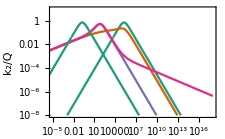

```mathematica
figure=LogLogPlot[{AbstractFigureOne[2*Pi/(x*3.15*10^7)],AbstractFigureFour[2*Pi/(x*3.15*10^7)],AbstractFigureFive[2*Pi/(x*3.15*10^7)],AbstractFigureSix[2*Pi/(x*3.15*10^7)],AbstractFigureSeven[2*Pi/(x*3.15*10^7)]},{x,10^-11,10^18},PlotRange->{{10^-5,10^18},{10^-8,10}},PlotLegends->{Style["Earth Mantle (Maxwell)",8],Style["Earth Mantle (Andrade)",8],Style["Hotter Mantle (Andrade)",8],Style["Rigid Lid (Andrade)",8],Style["Very soft (maxwell)",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},ImageSize->imagesize,LabelStyle->  Directive[FontSize->8],PlotStyle->{RGBColor["#1b9e77"],RGBColor["#d95f02"],RGBColor["#7570b3"],RGBColor["#e7298a"]}]
```

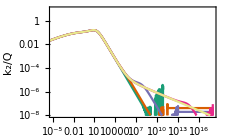

```mathematica
AbstractFigureSix2[myomega_,eta_,beta_:2*10^-12,alpha_:.25,eb_:7*10^5,temp_:1400,tempr_:1374] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5,3.5}10^3;
mys=     {6790,6800} 10^3;
mylens=Length[mys];
mymu = {40,40}10^9;
myeta = {1,eta}10^18;
mymubar = AndradeMu[myomega,mymu,myeta,beta,alpha,eb,temp,tempr];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
maxwelltest=LogLogPlot[{If[x<10^11,AbstractFigureSix2[2*Pi/(x*3.15*10^7),10^1]],AbstractFigureSix2[2*Pi/(Min[x,10^11.5]*3.15*10^7),10^3],AbstractFigureSix2[2*Pi/(Min[x,10^13]*3.15*10^7),10^5],AbstractFigureSix2[2*Pi/(x*3.15*10^7),10^10],AbstractFigureSix2[2*Pi/(x*3.15*10^7),10^15]},{x,10^-11,10^18},PlotRange->{{10^-5,10^18},{10^-8,10}},PlotLegends->{"10^19","10^21","10^23","10^28","10^33"}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},ImageSize->imagesize,LabelStyle->  Directive[FontSize->8],PlotStyle->{RGBColor["#1b9e77"],RGBColor["#d95f02"],RGBColor["#7570b3"],RGBColor["#e7298a"],RGBColor["#e7e98a"]}]
```

```mathematica
Export["LPSC-Abstract-Figure.svg",figure]
```

LPSC-Abstract-Figure.svg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["LPSC-Abstract-Figure.svg"]]]
```

```mathematica
AndradeMu[2Pi/(1.769138*24*3600),4*10^10,10^21]
```

1.89395×10^10

8.68424×10^10

1.80796×10^10+3.94298×10^9 ⅈ

```mathematica
MOTest0[myomega_,] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.6,3.5,3.4}10^3;
mys=     {1680,1700,1800} 10^3;
mylens=Length[mys];
mymu = {40,40,40}10^9;
myeta = {10^0,10^0,10^0}10^18;
mymubar = AndradeMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
MOTest1[myomega_] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.6,3.5,3.4}10^3;
mys=     {1680,1700,1800} 10^3;
mylens=Length[mys];
mymu = {40,40,40}10^9;
myeta = {10^0,10^-2,10^0}10^18;
mymubar = AndradeMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
MOTest2[myomega_] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.6,3.5,3.4}10^3;
mys=     {1680,1700,1800} 10^3;
mylens=Length[mys];
mymu = {40,40,40}10^9;
myeta = {10^0,10^-4,10^0}10^18;
mymubar =AndradeMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
MOTest3[myomega_] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.6,3.5,3.4}10^3;
mys=     {1680,1700,1800} 10^3;
mylens=Length[mys];
mymu = {40,40,40}10^9;
myeta = {10^0,10^-8,10^0}10^18;
mymubar =AndradeMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
MOTest4[myomega_] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.6,3.5,3.4}10^3;
mys=     {1680,1700,1800} 10^3;
mylens=Length[mys];
mymu = {40,40,40}10^9;
myeta = {10^0,10^-6,10^0}10^18;
mymubar =AndradeMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
MOTestVar[myomega_,oceaneta_,minomega_:0,motop_:1280] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec},
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5}10^3;
mys=     {200,740,motop,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40,40}10^9;
myeta = {10^21,10^21,oceaneta,10^21};
mymubar =AndradeMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
If[myomega>minomega,Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]],-1]
]
MOTestVarTimelag[myomega_,oceaneta_,minomega_:0,motop_:1280] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2,myq,phaselag},
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5}10^3;
mys=     {200,740,motop,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40,40}10^9;
myeta = {10^21,10^21,oceaneta,10^21};
mymubar =AndradeMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
k2 = yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]];
myq = Abs[k2]/Im[k2]; (* Decent chance this should be Re[k2]/Im[k2], need to double check *)
phaselag = ArcSin[1/myq];
If[myomega>minomega,yfq*phaselag/myomega,-1]
]
MOTestVark2[myomega_,oceaneta_,minomega_:0,motop_:1280] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5}10^3;
mys=     {200,740,motop,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40,40}10^9;
myeta = {10^21,10^21,oceaneta,10^21};
mymubar =AndradeMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
k2 = yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]];
If[myomega>minomega,Abs[k2],-1]
]
yfq = 2*Pi/(3.15*10^7)
```

1.99466×10^-7

```mathematica
MOTestVarTimelag[2*Pi/(.005*3.15*10^7),10^21,yfq/10^12]*365*24
```

0.738317

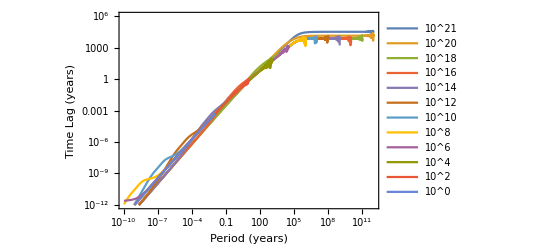

```mathematica
timelagfigure=LogLogPlot[{MOTestVarTimelag[2*Pi/(x*3.15*10^7),10^21,yfq/10^12],MOTestVarTimelag[2*Pi/(x*3.15*10^7),10^20,yfq/10^12],MOTestVarTimelag[2*Pi/(x*3.15*10^7),10^18,yfq/10^11],MOTestVarTimelag[2*Pi/(x*3.15*10^7),10^16,yfq/10^10],MOTestVarTimelag[2*Pi/(x*3.15*10^7),10^14,yfq/10^9],MOTestVarTimelag[2*Pi/(x*3.15*10^7),10^12,yfq/10^8],MOTestVarTimelag[2*Pi/(x*3.15*10^7),10^10,yfq/10^7],MOTestVarTimelag[2*Pi/(x*3.15*10^7),10^8,yfq/10^6],MOTestVarTimelag[2*Pi/(x*3.15*10^7),10^6,yfq/10^4.5],MOTestVarTimelag[2*Pi/(x*3.15*10^7),10^4,yfq/10^3],MOTestVarTimelag[2*Pi/(x*3.15*10^7),10^2,yfq/10^1],MOTestVarTimelag[yfq/x,10^0,yfq/10^-2]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-12,10^6}},PlotLegends->{Style["10^21",8],Style["10^20",8],Style["10^18",8],Style["10^16",8],Style["10^14",8],Style["10^12",8],Style["10^10",8],Style["10^8",8],Style["10^6",8],Style["10^4",8],Style["10^2",8],Style["10^0",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","Time Lag (years)"},LabelStyle->  Directive[FontSize->8]]
```

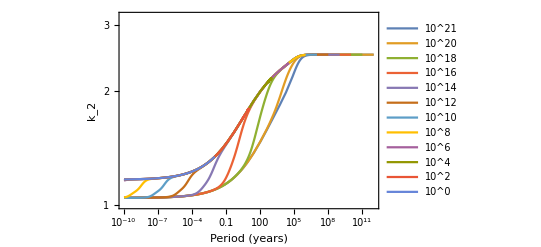

```mathematica
k2figure=LogLogPlot[{MOTestVark2[2*Pi/(x*3.15*10^7),10^21,yfq/10^12],MOTestVark2[2*Pi/(x*3.15*10^7),10^20,yfq/10^12],MOTestVark2[2*Pi/(x*3.15*10^7),10^18,yfq/10^11],MOTestVark2[2*Pi/(x*3.15*10^7),10^16,yfq/10^10],MOTestVark2[2*Pi/(x*3.15*10^7),10^14,yfq/10^9],MOTestVark2[2*Pi/(x*3.15*10^7),10^12,yfq/10^8],MOTestVark2[2*Pi/(x*3.15*10^7),10^10,yfq/10^7],MOTestVark2[2*Pi/(x*3.15*10^7),10^8,yfq/10^6],MOTestVark2[2*Pi/(x*3.15*10^7),10^6,yfq/10^4.5],MOTestVark2[2*Pi/(x*3.15*10^7),10^4,yfq/10^3],MOTestVark2[2*Pi/(x*3.15*10^7),10^2,yfq/10^1],MOTestVark2[yfq/x,10^0,yfq/10^-2]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^0,10^.5}},PlotLegends->{Style["10^21",8],Style["10^20",8],Style["10^18",8],Style["10^16",8],Style["10^14",8],Style["10^12",8],Style["10^10",8],Style["10^8",8],Style["10^6",8],Style["10^4",8],Style["10^2",8],Style["10^0",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2"},LabelStyle->  Directive[FontSize->8]]
```

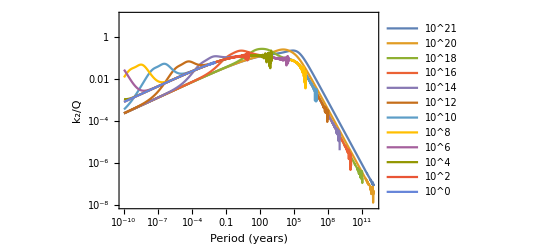

```mathematica
mofigure=LogLogPlot[{MOTestVar[2*Pi/(x*3.15*10^7),10^21,yfq/10^12],MOTestVar[2*Pi/(x*3.15*10^7),10^20,yfq/10^12],MOTestVar[2*Pi/(x*3.15*10^7),10^18,yfq/10^11],MOTestVar[2*Pi/(x*3.15*10^7),10^16,yfq/10^10],MOTestVar[2*Pi/(x*3.15*10^7),10^14,yfq/10^9],MOTestVar[2*Pi/(x*3.15*10^7),10^12,yfq/10^8],MOTestVar[2*Pi/(x*3.15*10^7),10^10,yfq/10^7],MOTestVar[2*Pi/(x*3.15*10^7),10^8,yfq/10^6],MOTestVar[2*Pi/(x*3.15*10^7),10^6,yfq/10^4.5],MOTestVar[2*Pi/(x*3.15*10^7),10^4,yfq/10^3],MOTestVar[2*Pi/(x*3.15*10^7),10^2,yfq/10^1],MOTestVar[yfq/x,10^0,yfq/10^-2]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["10^21",8],Style["10^20",8],Style["10^18",8],Style["10^16",8],Style["10^14",8],Style["10^12",8],Style["10^10",8],Style["10^8",8],Style["10^6",8],Style["10^4",8],Style["10^2",8],Style["10^0",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

```mathematica
Export["Varying-Viscosity-Figure.pdf",mofigure]
```

Varying-Viscosity-Figure.pdf

```mathematica
If[
```

```mathematica
Style[{"10^21","10^18"}]
```

{10^21,10^18}

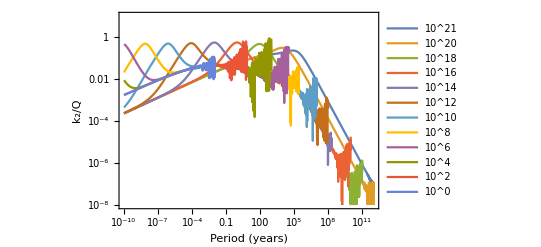

```mathematica
mofigurethincrust=LogLogPlot[{MOTestVar[2*Pi/(x*3.15*10^7),10^21,yfq/10^12,1780],MOTestVar[2*Pi/(x*3.15*10^7),10^20,yfq/10^12,1780],MOTestVar[2*Pi/(x*3.15*10^7),10^18,yfq/10^11,1780],MOTestVar[2*Pi/(x*3.15*10^7),10^16,yfq/10^10,1780],MOTestVar[2*Pi/(x*3.15*10^7),10^14,yfq/10^9,1780],MOTestVar[2*Pi/(x*3.15*10^7),10^12,yfq/10^8,1780],MOTestVar[2*Pi/(x*3.15*10^7),10^10,yfq/10^7,1780],MOTestVar[2*Pi/(x*3.15*10^7),10^8,yfq/10^6,1780],MOTestVar[2*Pi/(x*3.15*10^7),10^6,yfq/10^4.5,1780],MOTestVar[2*Pi/(x*3.15*10^7),10^4,yfq/10^3,1780],MOTestVar[2*Pi/(x*3.15*10^7),10^2,yfq/10^1,1780],MOTestVar[yfq/x,10^0,yfq/10^-2,1780]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["10^21",8],Style["10^20",8],Style["10^18",8],Style["10^16",8],Style["10^14",8],Style["10^12",8],Style["10^10",8],Style["10^8",8],Style["10^6",8],Style["10^4",8],Style["10^2",8],Style["10^0",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

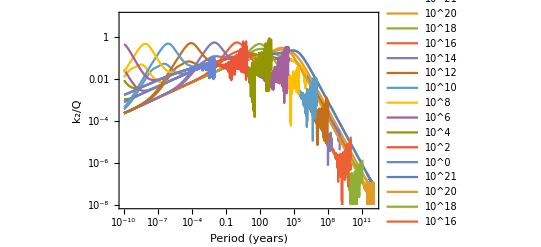

```mathematica
Show[mofigure,mofigurethincrust]
```

```mathematica
(* Trying to do the KISS 4 panels *)
(* Not sure how to handle a lithosphere...*)
```

```mathematica
Clear[KISS1,KISS2,KISS3,KISS4];
KISS1[myomega_,mantlevisc_:10^15,lithospherethickness_:20,minomega_:0] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(*This is solid body dissipation in the deep mantle, i assume that means a roughly uniformly very hot mantle *)
G=6.67 10^-11;
myrho={3.5,3.5,3.5}10^3;
mys=     {200,1820-lithospherethickness,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40}10^9;
myeta = {10^21,mantlevisc,10^2000};
mymubar =AndradeMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
KISS2[myomega_,mantlevisc_:10^15,lithospherethickness_:20,dissipationdepth_:1280,minomega_:0,deepvisc_:10^21] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(*This is solid body dissipation in the deep mantle, i assume that means a roughly uniformly very hot mantle *)
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5}10^3;
mys= {200,dissipationdepth,1820-lithospherethickness,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40,40}10^9;
myeta = {10^21,deepvisc,mantlevisc,10^200};
mymubar =AndradeMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
KISS3[myomega_,oceaneta_,minomega_:0,motop_:1280] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(* This is a shallow magma ocean *)
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5}10^3;
mys=     {200,740,motop,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40,40}10^9;
myeta = {10^21,10^21,oceaneta,10^21};
mymubar =AndradeMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
KISS4[myomega_,oceaneta_,minomega_:0,motop_:1280] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(* This is a shallow magma sponge, which I assume is a sof *)
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5}10^3;
mys=     {200,740,motop,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40,40}10^9;
myeta = {10^21,10^21,oceaneta,10^21};
mymubar =AndradeMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
Clear[KISS1M,KISS2M,KISS3M,KISS4M];
KISS1M[myomega_,mantlevisc_:10^15,lithospherethickness_:20,minomega_:0] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(*This is solid body dissipation in the deep mantle, i assume that means a roughly uniformly very hot mantle *)
G=6.67 10^-11;
myrho={3.5,3.5,3.5}10^3;
mys=     {200,1820-lithospherethickness,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40}10^9;
myeta = {10^21,mantlevisc,10^2000};
mymubar =MaxwellMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
KISS2M[myomega_,mantlevisc_:10^15,lithospherethickness_:20,dissipationdepth_:1280,minomega_:0,deepvisc_:10^21] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(*This is solid body dissipation in the deep mantle, i assume that means a roughly uniformly very hot mantle *)
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5}10^3;
mys= {200,dissipationdepth,1820-lithospherethickness,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40,40}10^9;
myeta = {10^21,deepvisc,mantlevisc,10^200};
mymubar =MaxwellMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
KISS3M[myomega_,oceaneta_,minomega_:0,motop_:1280] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(* This is a shallow magma ocean *)
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5}10^3;
mys=     {200,740,motop,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40,40}10^9;
myeta = {10^21,10^21,oceaneta,10^21};
mymubar =MaxwellMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
KISS4M[myomega_,oceaneta_,minomega_:0,motop_:1280] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(* This is a shallow magma sponge, which I assume is a sof *)
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5}10^3;
mys=     {200,740,motop,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40,40}10^9;
myeta = {10^21,10^21,oceaneta,10^21};
mymubar =MaxwellMu[myomega,mymu,myeta];
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
```

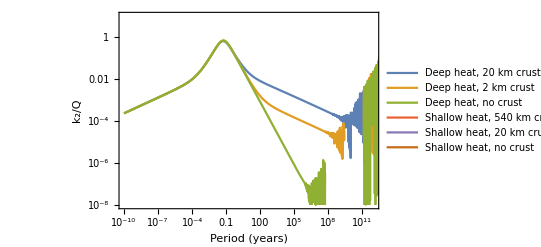

```mathematica
kiss1lithospherethicknessfigure=LogLogPlot[{KISS1[2*Pi/(x*3.15*10^7),10^15,20],KISS1[2*Pi/(x*3.15*10^7),10^15,2],KISS1[2*Pi/(x*3.15*10^7),10^15,0],KISS2[2*Pi/(x*3.15*10^7),10^15,540],KISS2[2*Pi/(x*3.15*10^7),10^15,20],KISS2[2*Pi/(x*3.15*10^7),10^15,0]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["Deep heat, 20 km crust",8],Style["Deep heat, 2 km crust",8],Style["Deep heat, no crust",8],Style["Shallow heat, 540 km crust",8],Style["Shallow heat, 20 km crust",8],Style["Shallow heat, no crust",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

```mathematica
KISS2[2*Pi/(3*3.15*10^7),10^15,20]
```

0.313063 Null^10

## Harrison 2 - layer approach

```mathematica
Clear[h1,h2,h3,h4,k2h,KISS1Harrison,KISS1MHarrison];
h1[r_,rc_, mu_,muc_,rho_,rhoc_,g_:1.796]:=Module[{eta,alpha,sigma,epsilon,delta},
alpha = rc/r;
eta = rhoc/rho-1;
delta = muc/mu;
sigma = mu/(g*rho*r);
epsilon = (delta-1)/delta;
(3/5)*1/(1+eta*alpha^3) + sigma/(5eta*alpha^2)*((35*(8-3alpha^2)-2(64-21alpha^2+21alpha^5-64alpha^7)epsilon)/(4-7alpha^4+3alpha^7-2(1-alpha^3)(1-alpha^7)epsilon))
];
h2[r_,rc_, mu_,muc_,rho_,rhoc_,g_:1.796]:=Module[{eta,alpha,sigma,epsilon,delta},
alpha = rc/r;
eta = rhoc/rho-1;
delta = muc/mu;
sigma = mu/(g*rho*r);
epsilon = (delta-1)/delta;
(1+2eta/5)/(1+eta*alpha^3) + (sigma/(5eta*alpha^2))(19*(delta-1) + (175-2(43+21alpha^3-64alpha^7)epsilon)/(4-7alpha^4+3alpha^7-2(1-alpha^3)(1-alpha^7)epsilon))
];
h3[r_,rc_, mu_,muc_,rho_,rhoc_,g_:1.796]:=Module[{eta,alpha,sigma,epsilon,delta},
alpha = rc/r;
eta = rhoc/rho-1;
delta = muc/mu;
sigma = mu/(g*rho*r);
epsilon = (delta-1)/delta;
1-(3/5)*1/(1+eta*alpha^3)+sigma/5*(19+alpha^3*(7(8-3alpha^2)^2 - 2(64-21alpha^4-43alpha^7)epsilon)/(4-7alpha^4+3alpha^7-2(1-alpha^3)(1-alpha^7)epsilon))
];
h4[r_,rc_, mu_,muc_,rho_,rhoc_,g_:1.796]:=Module[{eta,alpha,sigma,epsilon,delta},
alpha = rc/r;
eta = rhoc/rho-1;
delta = muc/mu;
sigma = mu/(g*rho*r);
epsilon = (delta-1)/delta;
eta*alpha^5*h1[r,rc, mu,muc,rho,rhoc,g]
];
k2h[r_,rc_, mu_,muc_,rho_,rhoc_,g_:1.796]:=Module[{eta,alpha,sigma,epsilon,delta},
alpha = rc/r;
eta = rhoc/rho-1;
delta = muc/mu;
sigma = mu/(g*rho*r);
epsilon = (delta-1)/delta;
(3/5)*(h2[r,rc, mu,muc,rho,rhoc,g]+h4[r,rc, mu,muc,rho,rhoc,g]+eta*alpha^5*(h1[r,rc, mu,muc,rho,rhoc,g]+h3[r,rc, mu,muc,rho,rhoc,g]))/((1+eta*alpha^3)*(h2[r,rc, mu,muc,rho,rhoc,g]*h3[r,rc, mu,muc,rho,rhoc,g]-h1[r,rc, mu,muc,rho,rhoc,g]*h4[r,rc, mu,muc,rho,rhoc,g]))
];
KISS1Harrison[myomega_,mantlevisc_:10^15,lithospherethickness_:20,crustviscosity_:10^2000,densityratio_:1.001,minomega_:0] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
G=6.67 10^-11;
myrho={3.5,3.5}10^3;
mys=     {1820-lithospherethickness,1820} 10^3;
mylens=Length[mys];
mymu = {40,40}10^9;
myeta = {mantlevisc,crustviscosity};
mymubar =MaxwellMu[myomega,mymu,myeta];
Im[-k2h[mys[[2]],mys[[1]],mymubar[[2]],mymubar[[1]],densityratio*myrho[[2]],myrho[[1]]]]
]
KISS1MHarrison[myomega_,mantlevisc_:10^15,lithospherethickness_:20,crustviscosity_:10^2000,densityratio_:1.001,minomega_:0] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
G=6.67 10^-11;
myrho={3.5,3.5}10^3;
mys=     {1820-lithospherethickness,1820} 10^3;
mylens=Length[mys];
mymu = {40,40}10^9;
myeta = {mantlevisc,crustviscosity};
mymubar =MaxwellMu[myomega,mymu,myeta];
Im[-k2h[mys[[2]],mys[[1]],mymubar[[2]],mymubar[[1]],densityratio*myrho[[2]],myrho[[1]]]]
]
KISS1HarrisonMuChange[myomega_,mantlevisc_:10^15,mantlemu_:40*10^9,lithospherethickness_:20,crustviscosity_:10^2000,densityratio_:1.001,minomega_:0] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
G=6.67 10^-11;
myrho={3.5,3.5}10^3;
mys=     {1820-lithospherethickness,1820} 10^3;
mylens=Length[mys];
mymu = {mantlemu,40}10^9;
myeta = {mantlevisc,crustviscosity};
mymubar =AndradeMu[myomega,mymu,myeta];
Im[-k2h[mys[[2]],mys[[1]],mymubar[[2]],mymubar[[1]],densityratio*myrho[[2]],myrho[[1]]]]
]
KISS1HarrisonMuChangeMaxwell[myomega_,mantlevisc_:10^15,mantlemu_:40*10^9,lithospherethickness_:20,crustviscosity_:10^2000,densityratio_:1.001,minomega_:0] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
G=6.67 10^-11;
myrho={3.5,3.5}10^3;
mys=     {1820-lithospherethickness,1820} 10^3;
mylens=Length[mys];
mymu = {mantlemu,40}10^9;
myeta = {mantlevisc,crustviscosity};
mymubar =MaxwellMu[myomega,mymu,myeta];
Im[-k2h[mys[[2]],mys[[1]],mymubar[[2]],mymubar[[1]],densityratio*myrho[[2]],myrho[[1]]]]
]
```

General::munfl: 1.56434673713887×10^-1993 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

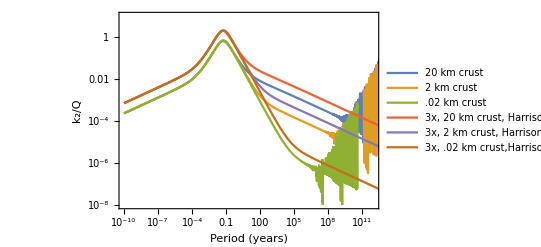

```mathematica
harrisoncheck=LogLogPlot[{KISS1[2*Pi/(x*3.15*10^7),10^15,20],KISS1[2*Pi/(x*3.15*10^7),10^15,2],KISS1[2*Pi/(x*3.15*10^7),10^15,0.02],3*KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,20],3*KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,2],3*KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,0.02]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["20 km crust",8],Style["2 km crust",8],Style[".02 km crust",8],Style["3x, 20 km crust, Harrison",8],Style["3x, 2 km crust, Harrison",8],Style["3x, .02 km crust,Harrison",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

General::munfl: 1/(0.+1.99203660480284×10^2003 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

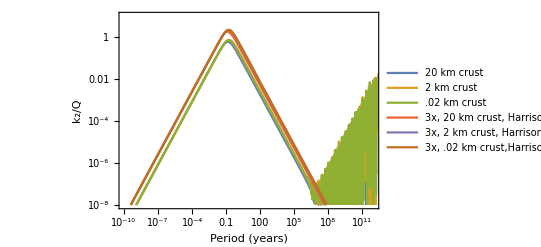

```mathematica
harrisonmaxwellcheck=LogLogPlot[{KISS1M[2*Pi/(x*3.15*10^7),10^15,20],KISS1M[2*Pi/(x*3.15*10^7),10^15,2],KISS1M[2*Pi/(x*3.15*10^7),10^15,0.02],3*KISS1MHarrison[2*Pi/(x*3.15*10^7),10^15,20],3*KISS1MHarrison[2*Pi/(x*3.15*10^7),10^15,2],3*KISS1MHarrison[2*Pi/(x*3.15*10^7),10^15,0.02]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["20 km crust",8],Style["2 km crust",8],Style[".02 km crust",8],Style["3x, 20 km crust, Harrison",8],Style["3x, 2 km crust, Harrison",8],Style["3x, .02 km crust,Harrison",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

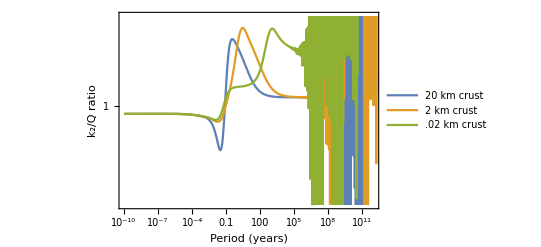

```mathematica
harrisonratiocheck=LogLogPlot[{KISS1[2*Pi/(x*3.15*10^7),10^15,20]/KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,20],KISS1[2*Pi/(x*3.15*10^7),10^15,2]/KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,2],KISS1[2*Pi/(x*3.15*10^7),10^15,0.02]/KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,0.02]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{.9,1.1}},PlotLegends->{Style["20 km crust",8],Style["2 km crust",8],Style[".02 km crust",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q ratio"},LabelStyle->  Directive[FontSize->8]]
```

General::munfl: 1/(0.+1.99203660480284×10^2003 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

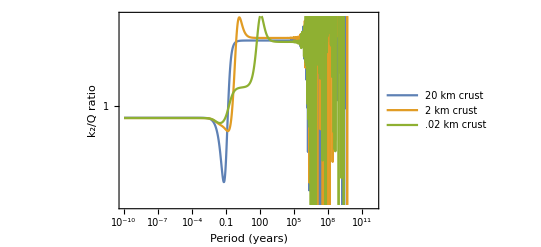

```mathematica
harrisonmaxwellratiocheck=LogLogPlot[{KISS1M[2*Pi/(x*3.15*10^7),10^15,20]/KISS1MHarrison[2*Pi/(x*3.15*10^7),10^15,20],KISS1M[2*Pi/(x*3.15*10^7),10^15,2]/KISS1MHarrison[2*Pi/(x*3.15*10^7),10^15,2],KISS1M[2*Pi/(x*3.15*10^7),10^15,0.02]/KISS1MHarrison[2*Pi/(x*3.15*10^7),10^15,0.02]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{.9,1.1}},PlotLegends->{Style["20 km crust",8],Style["2 km crust",8],Style[".02 km crust",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q ratio"},LabelStyle->  Directive[FontSize->8]]
```

General::munfl: 1.56434673713887×10^-1993 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

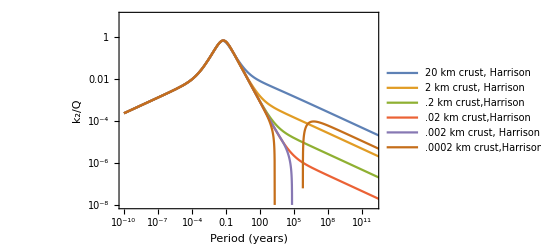

```mathematica
harrisoncrustthicknesstest=LogLogPlot[{KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,20],KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,2],KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,0.2],KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,.02],KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,0.002],KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,0.0002]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["20 km crust, Harrison",8],Style["2 km crust, Harrison",8],Style[".2 km crust,Harrison",8],Style[".02 km crust,Harrison",8],Style[".002 km crust, Harrison",8],Style[".0002 km crust,Harrison",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

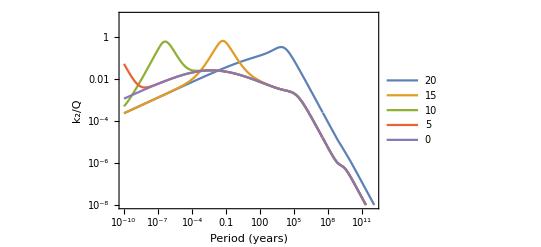

```mathematica
harrisonmagmaoceantest=LogLogPlot[{KISS1Harrison[2*Pi/(x*3.15*10^7),10^20,20,10^21],KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,20,10^21],KISS1Harrison[2*Pi/(x*3.15*10^7),10^10,20,10^21],KISS1Harrison[2*Pi/(x*3.15*10^7),10^5,20,10^21],KISS1Harrison[2*Pi/(x*3.15*10^7),10^0,20,10^21]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{20,15,10,5,0}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

General::munfl: 1.56434673713887×10^-1993 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

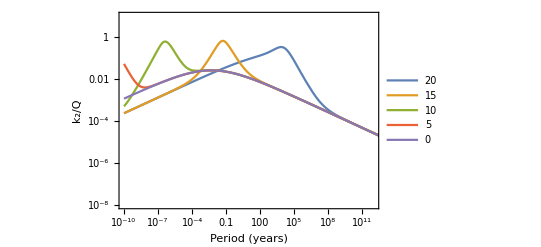

```mathematica
harrisonmagmaoceancrusttest=LogLogPlot[{KISS1Harrison[2*Pi/(x*3.15*10^7),10^20,20],KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,20],KISS1Harrison[2*Pi/(x*3.15*10^7),10^10,20],KISS1Harrison[2*Pi/(x*3.15*10^7),10^5,20],KISS1Harrison[2*Pi/(x*3.15*10^7),10^0,20]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{20,15,10,5,0}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

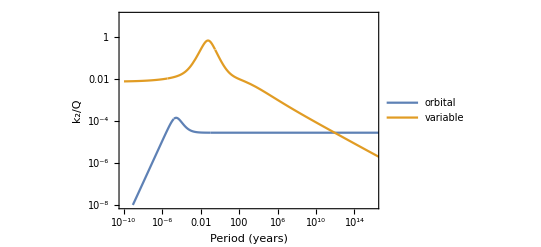

```mathematica
selfconsistent=LogLogPlot[{KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^15,20,3*10^16*x]*12*.0041^2,KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,20,3*10^16*x]},{x,10^-10,10^18},PlotRange->{{10^-10,10^16},{10^-8,10}},PlotLegends->{"orbital","variable"}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

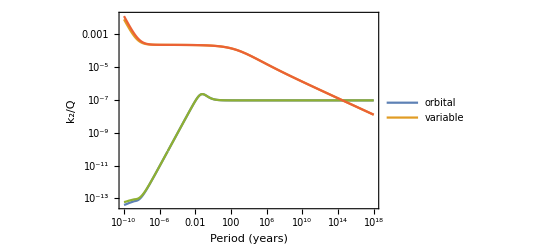

```mathematica
selfconsistentmagmaocean=LogLogPlot[{KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^4,.3,3*10^16*x]*12*.0041^2,KISS1Harrison[2*Pi/(x*3.15*10^7),10^4,.3,3*10^16*x],KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^4.2,.3,3*10^16*x]*12*.0041^2,KISS1Harrison[2*Pi/(x*3.15*10^7),10^4.2,.3,3*10^16*x]},{x,10^-10,10^18},PlotLegends->{"orbital","variable"}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

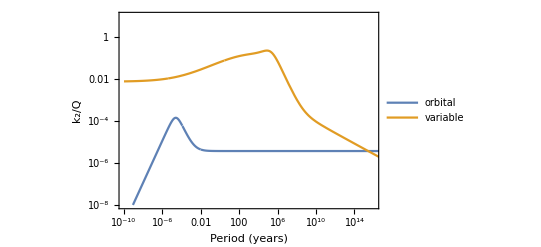

```mathematica
selfconsistentmantle=LogLogPlot[{KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^21,20,3*10^16*x]*12*.0041^2,KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,20,3*10^16*x]},{x,10^-10,10^18},PlotRange->{{10^-10,10^16},{10^-8,10}},PlotLegends->{"orbital","variable"}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

```mathematica
x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^15,20,3*10^16*x]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^15,20,3*10^16*x],{x,10^10}]
```

8.60289×10^11

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {3.46306×10^14}. Try perturbing the initial point(s).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

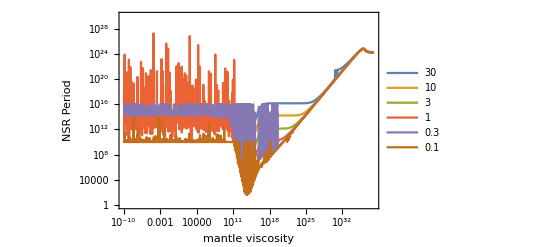

```mathematica
selfconsistentmantleviscosity=LogLogPlot[{x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),y,30,3*10^16*x]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),y,30,3*10^16*x],{x,10^10}],x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),y,10,3*10^16*x]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),y,10,3*10^16*x],{x,10^10}],x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),y,3,3*10^16*x]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),y,3,3*10^16*x],{x,10^10}],x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),y,1,3*10^16*x]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),y,1,3*10^16*x],{x,10^10}],x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),y,.3,3*10^16*x]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),y,.3,3*10^16*x],{x,10^16}],x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),y,.1,3*10^16*x]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),y,.1,3*10^16*x],{x,10^10}]},{y,10^-10,10^38},PlotRange->{{10^-10,10^38},{10^0,10^30}},PlotLegends->{30,10,3,1,.3,.1}, Frame->{True, True,False, False},FrameLabel->{"mantle viscosity","NSR Period"},LabelStyle->  Directive[FontSize->8]]
```

General::munfl: 1/(0.+4.11328604989785×10^1995 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(0.+1.99466200227923×10^1993 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

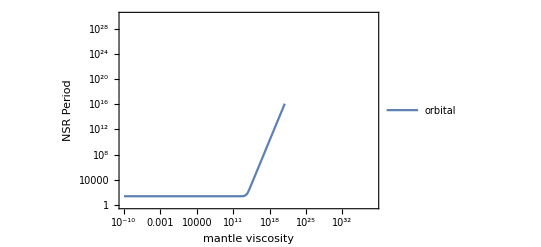

```mathematica
selfconsistentmantleviscositymaxwell=LogLogPlot[{x/.FindRoot[KISS1MHarrison[2*Pi/((1.77/365)*3.15*10^7),y,20,3*10^16*x]*12*.0041^2-KISS1MHarrison[2*Pi/(x*3.15*10^7),y,20,3*10^16*x],{x,10^5}]},{y,10^-10,10^38},PlotRange->{{10^-10,10^38},{10^0,10^30}},PlotLegends->{"orbital","variable"}, Frame->{True, True,False, False},FrameLabel->{"mantle viscosity","NSR Period"},LabelStyle->  Directive[FontSize->8]]
```

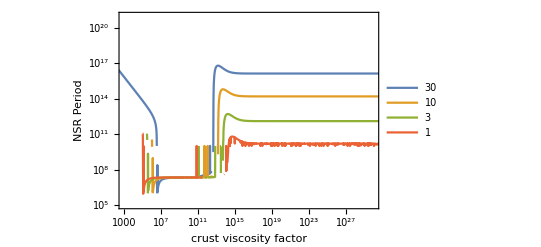

```mathematica
selfconsistentcrustviscosity=LogLogPlot[{x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,30,y*x]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,30,y*x],{x,10^10}],x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,10,y*x]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,10,y*x],{x,10^10}],x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,3,y*x]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,3,y*x],{x,10^10}],x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,1,y*x]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,1,y*x],{x,10^10}]},{y,10^-10,10^38},PlotRange->{{10^3,10^30},{10^5,10^21}},PlotLegends->{30,10,3,1,.3,.1}, Frame->{True, True,False, False},FrameLabel->{"crust viscosity factor","NSR Period"},LabelStyle->  Directive[FontSize->8]]
```

FindRoot::nlnum: The function value {-0.000121147 Im[(«1»)/(Times[«2»]+Times[«2»])]+0.600571 Im[(1.00055-«22» «1»-«1»-«1»)/(Times[«2»]+Times[«2»])]} is not a list of numbers with dimensions {1} at {z} = {1.×10^10}.

ReplaceAll::reps: {FindRoot[KISS1Harrison[2 (π Power[«2»]),10^18,30,y z] 12 0.0041^2-KISS1Harrison[2 (π Power[«2»]),10^18,30,y z],{z,10^10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.000121147 Im[(«1»)/(Times[«2»]+Times[«2»])]+0.600571 Im[(1.00055-«22» «1»-«1»-«1»)/(Times[«2»]+Times[«2»])]} is not a list of numbers with dimensions {1} at {z} = {1.×10^10}.

ReplaceAll::reps: {FindRoot[KISS1Harrison[2 (π Power[«2»]),10^18,30,y z] 12 0.0041^2-KISS1Harrison[2 (π Power[«2»]),10^18,30,y z],{z,10^10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::nlnum: The function value {-0.000121147 Im[(«1»)/(Times[«2»]+Times[«2»])]+0.600571 Im[(1.00055-«22» «1»-«1»-«1»)/(Times[«2»]+Times[«2»])]} is not a list of numbers with dimensions {1} at {z} = {1.×10^10}.

ReplaceAll::reps: {FindRoot[KISS1Harrison[2 (π Power[«2»]),10^18,30,y z] 12 0.0041^2-KISS1Harrison[2 (π Power[«2»]),10^18,30,y z],{z,10^10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.000121147 Im[(«1»)/(Times[«2»]+Times[«2»])]+0.600571 Im[(1.00055-«22» «1»-«1»-«1»)/(Times[«2»]+Times[«2»])]} is not a list of numbers with dimensions {1} at {z} = {1.×10^10}.

ReplaceAll::reps: {FindRoot[KISS1Harrison[2 (π Power[«2»]),10^18,30,y z] 12 0.0041^2-KISS1Harrison[2 (π Power[«2»]),10^18,30,y z],{z,10^10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.000121147 Im[(«1»)/(Times[«2»]+Times[«2»])]+0.600571 Im[(1.00055-«22» «1»-«1»-«1»)/(Times[«2»]+Times[«2»])]} is not a list of numbers with dimensions {1} at {z} = {1.×10^10}.

ReplaceAll::reps: {FindRoot[KISS1Harrison[2 (π Power[«2»]),10^18,30,y z] 12 0.0041^2-KISS1Harrison[2 (π Power[«2»]),10^18,30,y z],{z,10^10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

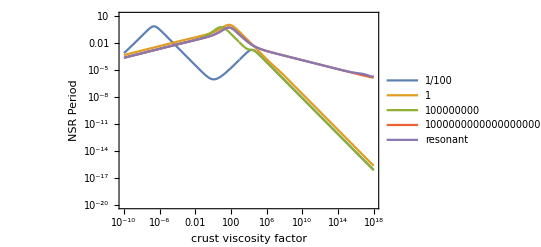

```mathematica
e1=z/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,30,y*z]*12*.0041^2-KISS1Harrison[2*Pi/(z*3.15*10^7),10^18,30,y*z],{z,10^10}]/.y->10^-2;
e2 = z/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,30,y*z]*12*.0041^2-KISS1Harrison[2*Pi/(z*3.15*10^7),10^18,30,y*z],{z,10^10}]/.y->10^3;
e3 = z/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,30,y*z]*12*.0041^2-KISS1Harrison[2*Pi/(z*3.15*10^7),10^18,30,y*z],{z,10^10}]/.y->10^8;
e4 = z/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,30,y*z]*12*.0041^2-KISS1Harrison[2*Pi/(z*3.15*10^7),10^18,30,y*z],{z,10^10}]/.y->10^23;
e5 = z/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,30,y*z]*12*.0041^2-KISS1Harrison[2*Pi/(z*3.15*10^7),10^18,30,y*z],{z,10^10}]/.y->1.668*10^13;
lowviscositycrust=LogLogPlot[{KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,30,10^-2*(e1)],2*KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,30,10^3*(e2)],KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,30,10^8*(e3)],KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,30,10^23*(e4)],KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,30,1.668*10^13*(e5)]},{x,10^-10,10^18},PlotRange->{{10^-10,10^18},{10^-20,10^1}},PlotLegends->{10^-2,1,10^8,10^23,"resonant"}, Frame->{True, True,False, False},FrameLabel->{"crust viscosity factor","NSR Period"},LabelStyle->  Directive[FontSize->8]]
```

```mathematica
e1
```

5.39387×10^9

```mathematica
KISS1Harrison[2*Pi/(1*3.15*10^7),10^18,30,10^-2*1]
```

5.97814×10^-7

```mathematica
x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,30,y*x]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,30,y*x],{x,10^10}]/.y->10^-2
```

FindRoot::nlnum: The function value {-0.000121147 Im[(«1»)/(Times[«2»]+Times[«2»])]+0.600571 Im[(1.00055-«22» «1»-«1»-«1»)/(Times[«2»]+Times[«2»])]} is not a list of numbers with dimensions {1} at {x} = {1.×10^10}.

ReplaceAll::reps: {FindRoot[KISS1Harrison[2 (π Power[«2»]),10^18,30,y x] 12 0.0041^2-KISS1Harrison[2 (π Power[«2»]),10^18,30,y x],{x,10^10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

5.39387×10^9

-Graphics-

```mathematica
harrisonmagmaoceanontop=LogLogPlot[{KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,20,10^21,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,20,10^20,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,20,10^19,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,20,10^18,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,20,10^15,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,20,10^12,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,20,10^9,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,20,10^6,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,20,10^3,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,20,10^0,1.000001]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{21,20,19,18,15,12,9,6,3,0}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

-Graphics-

General::munfl: 1.56434673713887×10^-2093 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
harrisonmaxwellmagmaocean=LogLogPlot[{KISS1MHarrison[2*Pi/(x*3.15*10^7),10^21,20,10^21,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^20,20,10^21,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^19,20,10^21,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^18,20,10^21,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^15,20,10^21,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^12,20,10^21,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^9,20,10^21,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^6,20,10^21,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^3,20,10^21,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^0,20,10^21,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^0,30,10^21,1.000001]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{21,20,19,18,15,12,9,6,3,0,0}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

-Graphics-

```mathematica
harrisonmaxwellmagmaoceancrust=LogLogPlot[{KISS1MHarrison[2*Pi/(x*3.15*10^7),10^21,20,10^2100,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^20,20,10^2100,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^19,20,10^2100,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^18,20,10^2100,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^15,20,10^2100,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^12,20,10^2100,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^9,20,10^2100,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^9,20,10^21,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^6,20,10^2100,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^3,20,10^2100,1.000001],KISS1MHarrison[2*Pi/(x*3.15*10^7),10^0,20,10^2100,1.000001],},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{21,20,19,18,15,12,9,9,6,3,0}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

General::munfl: 1/(0.+1.99203660480284×10^2103 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
paperfigure3aish=LogLogPlot[{KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,10,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^20,10,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^19,10,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,10,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^14,10,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^10,10,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^6,10,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^2,10,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^2,1,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^2,100,10^2100,1.000001]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["10^21",8],Style["10^18",8],Style["10^15",8],Style["10^12",8],Style["10^9",8],Style["10^6",8],Style["10^3",8],Style["10^0",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},ImageSize->imagesize,LabelStyle->  Directive[FontSize->8],PlotStyle->{RGBColor["#1b9e77"],RGBColor["#222222"],RGBColor["#555555"],RGBColor["#777777"],RGBColor["#999999"],RGBColor["#BBBBBB"],RGBColor["#DDDDDD"],RGBColor["#d95f02"],RGBColor["#7570b3"],RGBColor["#e7298a"]}]
```

General::munfl: 1.56434673713887×10^-2093 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
paperfigure3aish=LogLogPlot[{KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,1,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^20,1,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^19,1,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,1,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^14,1,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^10,1,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^6,1,10^2100,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^2,1,10^2100,1.000001]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["10^21",8],Style["10^18",8],Style["10^15",8],Style["10^12",8],Style["10^9",8],Style["10^6",8],Style["10^3",8],Style["10^0",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},ImageSize->imagesize,LabelStyle->  Directive[FontSize->8],PlotStyle->{RGBColor["#1b9e77"],RGBColor["#222222"],RGBColor["#555555"],RGBColor["#777777"],RGBColor["#999999"],RGBColor["#BBBBBB"],RGBColor["#DDDDDD"],RGBColor["#d95f02"],RGBColor["#7570b3"],RGBColor["#e7298a"]}]
```

General::munfl: 1.56434673713887×10^-2093 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
paperfigure3bishdialingviscosity=LogLogPlot[{KISS1Harrison[2*Pi/(x*3.15*10^7),10^21,20,10^21,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^20,20,10^21,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^19,20,10^21,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,20,10^21,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^14,20,10^21,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^10,20,10^21,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^6,20,10^21,1.000001],KISS1Harrison[2*Pi/(x*3.15*10^7),10^2,20,10^21,1.000001]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["10^21",8],Style["10^20",8],Style["10^19",8],Style["10^18",8],Style["10^14",8],Style["10^10",8],Style["10^6",8],Style["10^2",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},ImageSize->imagesize,LabelStyle->  Directive[FontSize->8],PlotStyle->{RGBColor["#1b9e77"],RGBColor["#222222"],RGBColor["#555555"],RGBColor["#777777"],RGBColor["#999999"],RGBColor["#BBBBBB"],RGBColor["#DDDDDD"],RGBColor["#d95f02"],RGBColor["#7570b3"],RGBColor["#e7298a"]}]
```

-Graphics-

```mathematica
Export["Magma-Ocean-NoCrust-Harrison.pdf",paperfigure3bishdialingviscosity]
```

Magma-Ocean-NoCrust-Harrison.pdf

```mathematica
Export["Magma-Ocean-Crust-Harrison.pdf",paperfigure3aish]
```

Magma-Ocean-Crust-Harrison.pdf

```mathematica
paperfigure3bishdialingmu=LogLogPlot[{
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^21,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^21,4*10^7,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^21,4*10^1,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^21,4*10^-3,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^21,4*10^-5,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^21,4*10^-7,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^21,4*10^-9,20,10^21,1.000001](*,
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^16,4*10^9,20,10^21,1.000001],KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^11,4*10^9,20,10^21,1.000001],KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^6,4*10^9,20,10^21,1.000001],KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^1,4*10^9,20,10^21,1.000001]*)},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["10^21",8],Style["10^18",8],Style["10^15",8],Style["10^12",8],Style["10^9",8],Style["10^6",8],Style["10^3",8],Style["10^0",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},ImageSize->imagesize,LabelStyle->  Directive[FontSize->8],PlotStyle->{RGBColor["#1b9e77"],RGBColor["#d95f02"],RGBColor["#7570b3"],RGBColor["#e7298a"]}]
```

-Graphics-

```mathematica
paperfigureMOFixed=LogLogPlot[{
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^21,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^20,4*10^0,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^19,4*10^-4,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^18,4*10^-18,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^17,4*10^-27,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^16,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^15,4*10^5,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^14,4*10^1,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^13,4*10^-3,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^12,4*10^-7,20,10^21,1.000001]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["10^9",8],Style["10^7",8],Style["10^5",8],Style["10^3",8],Style["10^1",8],Style["10^-1",8],Style["10^-3",8],Style["10^-5",8],Style["10^-7",8],Style["10^-9",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},ImageSize->imagesize,LabelStyle->  Directive[FontSize->8],PlotStyle->{RGBColor["#1b9e77"],RGBColor["#d95f02"],RGBColor["#7570b3"],RGBColor["#e7298a"]}]
```

-Graphics-

```mathematica
paperfigurecrustviscosity=LogLogPlot[{
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^21,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^20,4*10^0,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^19,4*10^-4,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^18,4*10^-18,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^17,4*10^-27,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^16,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^15,4*10^5,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^14,4*10^1,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^13,4*10^-3,20,10^21,1.000001],
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^12,4*10^-7,20,10^21,1.000001]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["10^9",8],Style["10^7",8],Style["10^5",8],Style["10^3",8],Style["10^1",8],Style["10^-1",8],Style["10^-3",8],Style["10^-5",8],Style["10^-7",8],Style["10^-9",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},ImageSize->imagesize,LabelStyle->  Directive[FontSize->8],PlotStyle->{RGBColor["#1b9e77"],RGBColor["#d95f02"],RGBColor["#7570b3"],RGBColor["#e7298a"]}]
```

-Graphics-

```mathematica
selfconsistentcrustviscosity=LogLogPlot[{x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,30,y*x*10^17*30]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,20,y*x*10^17*20],{x,10^7}],x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,10,y*x*10^17*10]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,10,y*x*10^17*10],{x,10^7}],x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,5,y*x*10^17*5]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,5,y*x*10^17*5],{x,10^9.1}](*,x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,1,y*x*10^17]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,1,y*x*10^17],{x,10^10.5}]*)},{y,10^-10,10^0},PlotRange->{{10^-10,10^0},{10^5,10^21}},PlotLegends->{20,10,5,1,.3,.1}, Frame->{True, True,False, False},FrameLabel->{"crust viscosity factor","NSR Period"},LabelStyle->  Directive[FontSize->8]]
```

-Graphics-

```mathematica
FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,1,2*10^-4*x*10^17]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,1,2*10^-4*x*10^17],{x,10^7}]
```

{x→2.34262×10^7}

```mathematica
FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,1,2.1*10^-4*x*10^17]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,1,2.2*10^-4*x*10^17],{x,10^7}]
```

{x→2.37736×10^7}

```mathematica
LogLogPlot[x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,1,y*x*10^17]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,1,y*x*10^17],{x,10^7}],{y,10^-4,10^-3}]
```

-Graphics-

```mathematica
paperfigure3bishdialingmumaxwell=LogLogPlot[{
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^21,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^21,4*10^7,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^21,4*10^1,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^21,4*10^-3,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^21,4*10^-5,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^21,4*10^-7,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^21,4*10^-9,20,10^21,1.000001](*,
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^16,4*10^9,20,10^21,1.000001],KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^11,4*10^9,20,10^21,1.000001],KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^6,4*10^9,20,10^21,1.000001],KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^1,4*10^9,20,10^21,1.000001]*)},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["10^21",8],Style["10^18",8],Style["10^15",8],Style["10^12",8],Style["10^9",8],Style["10^6",8],Style["10^3",8],Style["10^0",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},ImageSize->imagesize,LabelStyle->  Directive[FontSize->8]]
```

```mathematica
-Graphics-
paperfigure3bishdialingetamaxwell=LogLogPlot[{
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^21,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^18,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^15,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^12,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^9,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^6,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^3,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^0,4*10^9,20,10^21,1.000001](*,
KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^16,4*10^9,20,10^21,1.000001],KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^11,4*10^9,20,10^21,1.000001],KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^6,4*10^9,20,10^21,1.000001],KISS1HarrisonMuChange[2*Pi/(x*3.15*10^7),10^1,4*10^9,20,10^21,1.000001]*)},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["10^21",8],Style["10^18",8],Style["10^15",8],Style["10^12",8],Style["10^9",8],Style["10^6",8],Style["10^3",8],Style["10^0",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},ImageSize->imagesize,LabelStyle->  Directive[FontSize->8]]
```

-Graphics-

-Graphics-

```mathematica
paperfigureMOFixedmaxwell=LogLogPlot[{
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^21,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^20,4*10^0,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^19,4*10^-4,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^18,4*10^-18,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^17,4*10^-27,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^16,4*10^9,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^15,4*10^5,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^14,4*10^1,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^13,4*10^-3,20,10^21,1.000001],
KISS1HarrisonMuChangeMaxwell[2*Pi/(x*3.15*10^7),10^12,4*10^-7,20,10^21,1.000001]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["10^9",8],Style["10^7",8],Style["10^5",8],Style["10^3",8],Style["10^1",8],Style["10^-1",8],Style["10^-3",8],Style["10^-5",8],Style["10^-7",8],Style["10^-9",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},ImageSize->imagesize,LabelStyle->  Directive[FontSize->8],PlotStyle->{RGBColor["#1b9e77"],RGBColor["#d95f02"],RGBColor["#7570b3"],RGBColor["#e7298a"]}]
```

-Graphics-

```mathematica
KISS1HarrisonEarth1[myomega_,mantlevisc_:10^15,lithospherethickness_:20,crustviscosity_:10^2000,myg_:9.81,densityratio_:1.001,minomega_:0] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
G=6.67 10^-11;
myrho={5.5,5.5}10^3;
mys=     {6371-lithospherethickness,6371} 10^3;
mylens=Length[mys];
mymu = {40,40}10^9;
myeta = {mantlevisc,crustviscosity};
mymubar =MaxwellMu[myomega,mymu,myeta];
Im[-k2h[mys[[2]],mys[[1]],mymubar[[2]],mymubar[[1]],densityratio*myrho[[2]],myrho[[1]],myg]]
]
KISS1HarrisonEuropa[myomega_,mantlevisc_:10^15,lithospherethickness_:20,crustviscosity_:10^2000,densityratio_:1.001,minomega_:0] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
G=6.67 10^-11;
myrho={3,1}10^3;
mys=     {1560-lithospherethickness,1560} 10^3;
mylens=Length[mys];
mymu = {4,4}10^7;
myeta = {mantlevisc,crustviscosity};
mymubar =AndradeMu[myomega,mymu,myeta];
Im[-k2h[mys[[2]],mys[[1]],mymubar[[2]],mymubar[[1]],densityratio*myrho[[2]],myrho[[1]],1.314]]
]
KISS1HarrisonEuropa10[myomega_,mantlevisc_:10^15,lithospherethickness_:20,crustviscosity_:10^2000,densityratio_:1.001,minomega_:0] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
G=6.67 10^-11;
myrho={3,1}10^3;
mys=     {1560-lithospherethickness,1560} 10^3;
mylens=Length[mys];
mymu = {40,40}10^8;
myeta = {mantlevisc,crustviscosity};
mymubar =AndradeMu[myomega,mymu,myeta];
Im[-k2h[mys[[2]],mys[[1]],mymubar[[2]],mymubar[[1]],densityratio*myrho[[2]],myrho[[1]],1.314]]
]
KISS1HarrisonEuropa10Iog[myomega_,mantlevisc_:10^15,lithospherethickness_:20,crustviscosity_:10^2000,densityratio_:1.001,minomega_:0] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
G=6.67 10^-11;
myrho={3,1}10^3;
mys=     {1560-lithospherethickness,1560} 10^3;
mylens=Length[mys];
mymu = {40,40}10^9;
myeta = {mantlevisc,crustviscosity};
mymubar =AndradeMu[myomega,mymu,myeta];
Im[-k2h[mys[[2]],mys[[1]],mymubar[[2]],mymubar[[1]],densityratio*myrho[[2]],myrho[[1]]]]
]
```

```mathematica
EarthIoEuropa=LogLogPlot[{x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,30,y*x*10^17*30]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,30,y*x*10^17*30],{x,10^7}],x/.FindRoot[KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,10,y*x*10^17*10]*12*.0041^2-KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,10,y*x*10^17*10],{x,10^7}],x/.FindRoot[KISS1HarrisonEarth1[2*Pi/((1.77/365)*3.15*10^7),10^18,30,y*x*10^17*30]*12*.0041^2-KISS1HarrisonEarth1[2*Pi/(x*3.15*10^7),10^18,30,y*x*10^17*30],{x,10^5}],x/.FindRoot[KISS1HarrisonEarth1[2*Pi/((1.77/365)*3.15*10^7),10^18,10,y*x*10^17*10]*12*.0041^2-KISS1HarrisonEarth1[2*Pi/(x*3.15*10^7),10^18,10,y*x*10^17*10],{x,10^5}],x/.FindRoot[KISS1HarrisonEuropa[2*Pi/((1.77/365)*3.15*10^7),10^18,30,y*x*10^17*30]*12*.0041^2-KISS1HarrisonEuropa[2*Pi/(x*3.15*10^7),10^18,30,y*x*10^17*30],{x,10^8}],x/.FindRoot[KISS1HarrisonEuropa[2*Pi/((1.77/365)*3.15*10^7),10^18,10,y*x*10^17*10]*12*.0041^2-KISS1HarrisonEuropa[2*Pi/(x*3.15*10^7),10^18,10,y*x*10^17*10],{x,10^8}]},{y,10^-10,10^0},PlotRange->{{10^-10,10^0},{10^5,10^25}},PlotLegends->{"Io, 30 km", "Io, 10 km", "Earth, 30 km", "Earth, 10 km", "Europa, 30 km", "Europa, 10 km"}, Frame->{True, True,False, False},FrameLabel->{"crust viscosity factor","NSR Period"},LabelStyle->  Directive[FontSize->8]]
```

-Graphics-

```mathematica
LogLogPlot[{KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,30,10^-7*x*10^17*30]*12*.0041^2,KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,30,10^-7*x*10^17*30],KISS1Harrison[2*Pi/((1.77/365)*3.15*10^7),10^18,30,10^-1*x*10^17*30]*12*.0041^2,KISS1Harrison[2*Pi/(x*3.15*10^7),10^18,30,10^-1*x*10^17*30],KISS1HarrisonEarth1[2*Pi/((1.77/365)*3.15*10^7),10^18,30,10^-7*x*10^17*30]*12*.0041^2,KISS1HarrisonEarth1[2*Pi/(x*3.15*10^7),10^18,30,10^-7*x*10^17*30],KISS1HarrisonEarth1[2*Pi/((1.77/365)*3.15*10^7),10^18,30,10^-1*x*10^17*30]*12*.0041^2,KISS1HarrisonEarth1[2*Pi/(x*3.15*10^7),10^18,30,10^-1*x*10^17*30]},{x,10^-10,10^28},PlotRange->{{10^-10,10^28},{10^-10,10^1}},PlotLegends->{"Io, 30 km, left, -7","Io, 30 km, right, -7","Io, 30 km, left, -1","Io, 30 km, right, -1","earth, 30 km, left, -7","earth, 30 km, right, -7","earth, 30 km, left, -1","earth, 30 km, right, -1" }, Frame->{True, True,False, False},FrameLabel->{"Period","k2/Q"},LabelStyle->  Directive[FontSize->8]]
```

-Graphics-

```mathematica
rigiditycomparison=LogLogPlot[{x/.FindRoot[KISS1HarrisonEuropa[2*Pi/((1.77/365)*3.15*10^7),10^18,30,y*x*10^17*30]*12*.0041^2-KISS1HarrisonEuropa[2*Pi/(x*3.15*10^7),10^18,30,y*x*10^17*30],{x,10^8}],x/.FindRoot[KISS1HarrisonEuropa[2*Pi/((1.77/365)*3.15*10^7),10^18,10,y*x*10^17*10]*12*.0041^2-KISS1HarrisonEuropa[2*Pi/(x*3.15*10^7),10^18,10,y*x*10^17*10],{x,10^8}],x/.FindRoot[KISS1HarrisonEuropa10[2*Pi/((1.77/365)*3.15*10^7),10^18,30,y*x*10^17*30]*12*.0041^2-KISS1HarrisonEuropa[2*Pi/(x*3.15*10^7),10^18,30,y*x*10^17*30],{x,10^8}],x/.FindRoot[KISS1HarrisonEuropa10[2*Pi/((1.77/365)*3.15*10^7),10^18,10,y*x*10^17*10]*12*.0041^2-KISS1HarrisonEuropa[2*Pi/(x*3.15*10^7),10^18,10,y*x*10^17*10],{x,10^8}]},{y,10^-10,10^0},PlotRange->{{10^-10,10^0},{10^5,10^25}},PlotLegends->{"4 GPa, 30 km", "4 GPa, 10 km", "40 GPa, 30 km", "40 GPa, 10 km"}, Frame->{True, True,False, False},FrameLabel->{"crust viscosity factor","NSR Period"},LabelStyle->  Directive[FontSize->8]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

```mathematica
Export["Rigidity-Comparison.pdf", rigiditycomparison]
```

Rigidity-Comparison.pdf

```mathematica
rigiditycomparisonmainfig=LogLogPlot[{KISS1HarrisonEuropa[2*Pi/(x*3.15*10^7),10^17,30,10^17],KISS1HarrisonEuropa[2*Pi/(x*3.15*10^7),10^17,30,10^230],KISS1HarrisonEuropa10[2*Pi/(x*3.15*10^7),10^17,30,10^17],KISS1HarrisonEuropa10[2*Pi/(x*3.15*10^7),10^17,30,10^230],KISS1HarrisonEarth1[2*Pi/(x*3.15*10^7),10^17,30,10^17],KISS1HarrisonEarth1[2*Pi/(x*3.15*10^7),10^17,30,10^230](*,KISS1Harrison[2*Pi/(x*3.15*10^7),10^17,30,10^17],KISS1Harrison[2*Pi/(x*3.15*10^7),10^17,30,10^230],KISS1HarrisonEarth1[2*Pi/(x*3.15*10^7),10^17,30,10^17,1.314],KISS1HarrisonEarth1[2*Pi/(x*3.15*10^7),10^17,30,10^230,1.314]*)},{x,10^-10,10^12},PlotRange->{{10^-3,10^8},{10^-7,10^0}},PlotLegends->{"Europa, 4GPa, Uniform",  "Europa, 4GPa, Crust","Europa, 40GPa, Uniform","Europa, 40GPa, Crust","Earth, Uniform", "Earth, Crust","Io, Uniform", "Io, Crust","Earth, Uniform, Europa's g", "Earth, Crust, Europa's g",}, Frame->{True, True,False, False},FrameLabel->{"Period","k2/Q"},LabelStyle->  Directive[FontSize->8]]
```

-Graphics-

```mathematica
Export["Trying-to-understand-Europa.pdf",rigiditycomparisonmainfig]
```

Trying-to-understand-Europa.pdf

```mathematica
rigiditycomparisonmainfig2=LogLogPlot[{KISS1HarrisonEuropa[2*Pi/(x*3.15*10^7),10^17,30,10^2300],KISS1HarrisonEuropa10[2*Pi/(x*3.15*10^7),10^17,30,10^2300],KISS1HarrisonEuropa10Iog[2*Pi/(x*3.15*10^7),10^17,30,10^2300],KISS1HarrisonEarth1[2*Pi/(x*3.15*10^7),10^17,30,10^2300],KISS1Harrison[2*Pi/(x*3.15*10^7),10^17,30,10^2300],KISS1HarrisonEarth1[2*Pi/(x*3.15*10^7),10^17,30,10^2300,1.314]},{x,10^-30,10^32},PlotRange->{{10^-30,10^32},{10^-8,10^0}},PlotLegends->{"Europa, 4GPa, Crust","Europa, 40GPa, Crust", "Europa, 40GPa, Io's g, Crust", "Earth, Crust", "Io, Crust", "Earth, Crust, Europa's g",}, Frame->{True, True,False, False},FrameLabel->{"Period","k2/Q"},LabelStyle->  Directive[FontSize->8]]
```

General::munfl: 1.56434673713887×10^-2293 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
Export["Trying-to-understand-Europa-2.pdf",rigiditycomparisonmainfig2]
```

Trying-to-understand-Europa-2.pdf

```mathematica
Export["More-Rigidity-Comparison.pdf",rigiditycomparisonmainfig]
```

More-Rigidity-Comparison.pdf

```mathematica
UniformTestIm[omega_,eta_,mu_,g_:1.314,R_:1560000,rho_:3000]:=Module[{mustar,mustarbar,k2star},mustar=1/(1/mu+1/(ⅈ eta omega));mustarbar=(19 mustar)/(2 (g R rho));k2star=3/(2 (mustarbar+1));Im[mustar](*-Im[k2star]*)]
UniformTestRe[omega_,eta_,mu_,g_:1.314,R_:1560000,rho_:3000]:=Module[{mustar,mustarbar,k2star},mustar=1/(1/mu+1/(ⅈ eta omega));mustarbar=(19 mustar)/(2 (g R rho));k2star=3/(2 (mustarbar+1));Re[mustar](*-Im[k2star]*)]
UniformTestk2[omega_,eta_,mu_,g_:1.314,R_:1560000,rho_:3000]:=Module[{mustar,mustarbar,k2star},mustar=1/(1/mu+1/(ⅈ eta omega));mustarbar=(19 mustar)/(2 (g R rho));k2star=3/(2 (mustarbar+1));-Im[k2star]]
UniformTestk2r[omega_,eta_,mu_,g_:1.314,R_:1560000,rho_:3000]:=Module[{mustar,mustarbar,k2star},mustar=1/(1/mu+1/(ⅈ eta omega));mustarbar=(19 mustar)/(2 (g R rho));k2star=3/(2 (mustarbar+1));Re[k2star]]
```

```mathematica
muetaexplore1 = LogLogPlot[{UniformTestIm[2*Pi/(x*3.15*10^7),10^17,40*10^7],UniformTestIm[2*Pi/(x*3.15*10^7),10^17,4*10^7],UniformTestIm[2*Pi/(x*3.15*10^7),10^18,40*10^7],UniformTestIm[2*Pi/(x*3.15*10^7),10^18,4*10^7],UniformTestIm[2*Pi/(x*3.15*10^7),10^17,40*10^7,10],UniformTestIm[2*Pi/(x*3.15*10^7),10^17,4*10^7,10],UniformTestIm[2*Pi/(x*3.15*10^7),10^18,40*10^7,10],UniformTestIm[2*Pi/(x*3.15*10^7),10^18,4*10^7,10]},{x,10^-10,10^12},PlotRange->{{10^-3,10^8},{10^-7,10^10}},PlotLegends->{"10^17 Pa.s,40 GPa","10^17 Pa.s,4 GPa","10^18 Pa.s,40 GPa","10^18 Pa.s,4 GPa","g=10"},PlotStyle->{{RGBColor["#1b9e77"],Dashing[Normal]},{RGBColor["#d95f02"],Dashing[Normal]},{RGBColor["#7570b3"],Dashing[Normal]},{RGBColor["#e7298a"],Dashing[Normal]},{RGBColor["#1b9e77"],Dashing[Tiny]},{RGBColor["#d95f02"],Dashing[Tiny]},{RGBColor["#7570b3"],Dashing[Tiny]},{RGBColor["#e7298a"],Dashing[Tiny]}},PlotLabel->"Im[mu*]"]
muetaexplore2 = LogLogPlot[{UniformTestRe[2*Pi/(x*3.15*10^7),10^17,40*10^7],UniformTestRe[2*Pi/(x*3.15*10^7),10^17,4*10^7],UniformTestRe[2*Pi/(x*3.15*10^7),10^18,40*10^7],UniformTestRe[2*Pi/(x*3.15*10^7),10^18,4*10^7],UniformTestRe[2*Pi/(x*3.15*10^7),10^17,40*10^7,10],UniformTestRe[2*Pi/(x*3.15*10^7),10^17,4*10^7,10],UniformTestRe[2*Pi/(x*3.15*10^7),10^18,40*10^7,10],UniformTestRe[2*Pi/(x*3.15*10^7),10^18,4*10^7,10]},{x,10^-10,10^12},PlotRange->{{10^-3,10^8},{10^-7,10^10}},PlotLegends->{"10^17 Pa.s,40 GPa","10^17 Pa.s,4 GPa","10^18 Pa.s,40 GPa","10^18 Pa.s,4 GPa","g=10"},PlotStyle->{{RGBColor["#1b9e77"],Dashing[Normal]},{RGBColor["#d95f02"],Dashing[Normal]},{RGBColor["#7570b3"],Dashing[Normal]},{RGBColor["#e7298a"],Dashing[Normal]},{RGBColor["#1b9e77"],Dashing[Tiny]},{RGBColor["#d95f02"],Dashing[Tiny]},{RGBColor["#7570b3"],Dashing[Tiny]},{RGBColor["#e7298a"],Dashing[Tiny]}},PlotLabel->"Re[mu*]"]
muetaexplore3 = LogLogPlot[{UniformTestk2[2*Pi/(x*3.15*10^7),10^17,40*10^7],UniformTestk2[2*Pi/(x*3.15*10^7),10^17,4*10^7],UniformTestk2[2*Pi/(x*3.15*10^7),10^18,40*10^7],UniformTestk2[2*Pi/(x*3.15*10^7),10^18,4*10^7],UniformTestk2[2*Pi/(x*3.15*10^7),10^17,40*10^7,10],UniformTestk2[2*Pi/(x*3.15*10^7),10^17,4*10^7,10],UniformTestk2[2*Pi/(x*3.15*10^7),10^18,40*10^7,10],UniformTestk2[2*Pi/(x*3.15*10^7),10^18,4*10^7,10]},{x,10^-10,10^12},PlotRange->{{10^-3,10^8},{10^-7,10^10}},PlotLegends->{"10^17 Pa.s,40 GPa","10^17 Pa.s,4 GPa","10^18 Pa.s,40 GPa","10^18 Pa.s,4 GPa","g=10"},PlotStyle->{{RGBColor["#1b9e77"],Dashing[Normal]},{RGBColor["#d95f02"],Dashing[Normal]},{RGBColor["#7570b3"],Dashing[Normal]},{RGBColor["#e7298a"],Dashing[Normal]},{RGBColor["#1b9e77"],Dashing[Tiny]},{RGBColor["#d95f02"],Dashing[Tiny]},{RGBColor["#7570b3"],Dashing[Tiny]},{RGBColor["#e7298a"],Dashing[Tiny]}},PlotLabel->"Im[k2]"]
muetaexplore3 = LogLogPlot[{UniformTestk2r[2*Pi/(x*3.15*10^7),10^17,40*10^7],UniformTestk2r[2*Pi/(x*3.15*10^7),10^17,4*10^7],UniformTestk2r[2*Pi/(x*3.15*10^7),10^18,40*10^7],UniformTestk2r[2*Pi/(x*3.15*10^7),10^18,4*10^7],UniformTestk2r[2*Pi/(x*3.15*10^7),10^17,40*10^7,10],UniformTestk2r[2*Pi/(x*3.15*10^7),10^17,4*10^7,10],UniformTestk2r[2*Pi/(x*3.15*10^7),10^18,40*10^7,10],UniformTestk2r[2*Pi/(x*3.15*10^7),10^18,4*10^7,10]},{x,10^-10,10^12},PlotRange->{{10^-3,10^8},{10^-1,10^1.1}},PlotLegends->{"10^17 Pa.s,40 GPa","10^17 Pa.s,4 GPa","10^18 Pa.s,40 GPa","10^18 Pa.s,4 GPa","g=10"},PlotStyle->{{RGBColor["#1b9e77"],Dashing[Normal]},{RGBColor["#d95f02"],Dashing[Normal]},{RGBColor["#7570b3"],Dashing[Normal]},{RGBColor["#e7298a"],Dashing[Normal]},{RGBColor["#1b9e77"],Dashing[Tiny]},{RGBColor["#d95f02"],Dashing[Tiny]},{RGBColor["#7570b3"],Dashing[Tiny]},{RGBColor["#e7298a"],Dashing[Tiny]}},PlotLabel->"Re[k2]"]
muetaexplore4 = LogLogPlot[{UniformTestk2[2*Pi/(x*3.15*10^7),10^170,40*10^7],UniformTestk2[2*Pi/(x*3.15*10^7),10^170,4*10^7],UniformTestk2[2*Pi/(x*3.15*10^7),10^171,40*10^7],UniformTestk2[2*Pi/(x*3.15*10^7),10^171,4*10^7],UniformTestk2[2*Pi/(x*3.15*10^7),10^170,40*10^7,10],UniformTestk2[2*Pi/(x*3.15*10^7),10^170,4*10^7,10],UniformTestk2[2*Pi/(x*3.15*10^7),10^171,40*10^7,10],UniformTestk2[2*Pi/(x*3.15*10^7),10^171,4*10^7,10]},{x,10^-10,10^12},PlotRange->{{10^-3,10^8},{10^-163,10^-148}},PlotLegends->{"10^17 Pa.s,40 GPa","10^17 Pa.s,4 GPa","10^18 Pa.s,40 GPa","10^18 Pa.s,4 GPa","g=10"},PlotStyle->{{RGBColor["#1b9e77"],Dashing[Normal]},{RGBColor["#d95f02"],Dashing[Normal]},{RGBColor["#7570b3"],Dashing[Normal]},{RGBColor["#e7298a"],Dashing[Normal]},{RGBColor["#1b9e77"],Dashing[Tiny]},{RGBColor["#d95f02"],Dashing[Tiny]},{RGBColor["#7570b3"],Dashing[Tiny]},{RGBColor["#e7298a"],Dashing[Tiny]}},PlotLabel->"Im[k2]"]
muetaexplore5 = LogLogPlot[{1.01*UniformTestk2r[2*Pi/(x*3.15*10^7),10^170,40*10^7],1.01*UniformTestk2r[2*Pi/(x*3.15*10^7),10^170,4*10^7],UniformTestk2r[2*Pi/(x*3.15*10^7),10^171,40*10^7],UniformTestk2r[2*Pi/(x*3.15*10^7),10^171,4*10^7],1.01*UniformTestk2r[2*Pi/(x*3.15*10^7),10^170,40*10^7,10],1.01*UniformTestk2r[2*Pi/(x*3.15*10^7),10^170,4*10^7,10],UniformTestk2r[2*Pi/(x*3.15*10^7),10^171,40*10^7,10],UniformTestk2r[2*Pi/(x*3.15*10^7),10^171,4*10^7,10]},{x,10^-10,10^12},PlotRange->{{10^-3,10^8},{10^-.1,10^.3}},PlotLegends->{"10^17 Pa.s,40 GPa","10^17 Pa.s,4 GPa","10^18 Pa.s,40 GPa","10^18 Pa.s,4 GPa","g=10"},PlotStyle->{{RGBColor["#1b9e77"],Dashing[Normal]},{RGBColor["#d95f02"],Dashing[Normal]},{RGBColor["#7570b3"],Dashing[Normal]},{RGBColor["#e7298a"],Dashing[Normal]},{RGBColor["#1b9e77"],Dashing[Tiny]},{RGBColor["#d95f02"],Dashing[Tiny]},{RGBColor["#7570b3"],Dashing[Tiny]},{RGBColor["#e7298a"],Dashing[Tiny]}},PlotLabel->"Re[k2]"]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

```mathematica
Export["muetaexplore1.pdf",muetaexplore1]
Export["muetaexplore2.pdf",muetaexplore2]
Export["muetaexplore3.pdf",muetaexplore3]
```

muetaexplore1.pdf

muetaexplore2.pdf

muetaexplore3.pdf

```mathematica
{UniformTest[.1,10^17,40*10^9],UniformTest[.01,10^17,40*10^9],UniformTest[.1,10^18,40*10^9],UniformTest[.1,10^17,4*10^9]}
```

{9.40297×10^-8,9.40297×10^-7,9.40297×10^-9,7.19323×10^-8}

```mathematica
UniformTest[0.1,100000000000000000,40000000000]
```

9.40297×10^-8

```mathematica
1560000*1.314*3000
```

6.14952×10^9

```mathematica
10^Range[10]
```

{10,100,1000,10000,100000,1000000,10000000,100000000,1000000000,10000000000}

```mathematica
Log10[1000]
```

3

```mathematica
Range[3]*0+3.5
```

{3.5,3.5,3.5}

```mathematica
(Range[3]-1)/2*(1820-200)+200
```

{200,1010,1820}

```mathematica
10^(((Range[3]-1)/2)*(Log10[10^25]-Log10[10^21])+Log10[10^21])
```

{1000000000000000000000,100000000000000000000000,10000000000000000000000000}

```mathematica
KISS2Core[myomega_,mantlevisc_:10^15,lithospherethickness_:20,dissipationdepth_:1280,minomega_:0,deepvisc_:10^21] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(*This is solid body dissipation in the deep mantle, i assume that means a roughly uniformly very hot mantle *)
G=6.67 10^-11;
myrho={3.5,3.5,3.5,3.5}10^3;
mys= {200,dissipationdepth,1820-lithospherethickness,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40,40}10^9;
myeta = {10^21,deepvisc,mantlevisc,10^200};
mymubar =AndradeMu[myomega,mymu,myeta];
(* Print[{myrho,mys,mymu,myeta,mymubar}];*)
mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
KISS2NoCore[myomega_,mantlevisc_:10^15,lithospherethickness_:20,dissipationdepth_:1280,minomega_:0,deepvisc_:10^21] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(*This is solid body dissipation in the deep mantle, i assume that means a roughly uniformly very hot mantle *)
G=6.67 10^-11;
myrho={3.5,3.5,3.5}10^3;
mys= {dissipationdepth,1820-lithospherethickness,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40}10^9;
myeta = {deepvisc,mantlevisc,10^200};
mymubar =AndradeMu[myomega,mymu,myeta];

mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
KISS22layer[myomega_,mantlevisc_:10^15,lithospherethickness_:20,dissipationdepth_:1280,minomega_:0,deepvisc_:10^21] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(*This is solid body dissipation in the deep mantle, i assume that means a roughly uniformly very hot mantle *)
G=6.67 10^-11;
myrho={3.5,3.5}10^3;
mys= {dissipationdepth,1820} 10^3;
mylens=Length[mys];
mymu = {40,40}10^9;
myeta = {deepvisc,mantlevisc};
mymubar =AndradeMu[myomega,mymu,myeta];

mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
ManyLayer[myomega_,topvisc_:10^15,bottomvisc_:10^15,layernumber_:2,minomega_:0,deepvisc_:10^21] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(*This is solid body dissipation in the deep mantle, i assume that means a roughly uniformly very hot mantle *)
G=6.67 10^-11;
myrho=Range[layernumber]*0+3.5*10^3;
mys=((Range[layernumber])/(layernumber)*1820) 10^3;
mylens=Length[mys];
mymu = Range[layernumber]*0+40*10^9;
myeta =10^(((Range[layernumber]-1)/(layernumber-1))*(Log10[topvisc]-Log10[bottomvisc])+Log10[bottomvisc]);
mymubar =AndradeMu[myomega,mymu,myeta];

mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
ManyLayer[2*Pi/(5*3.15*10^7),10^15,10^21,2]
KISS22layer[2*Pi/(5*3.15*10^7),10^15,20,910]
KISS2Core[2*Pi/(5*3.15*10^7),10^15,0,910]
KISS2NoCore[2*Pi/(5*3.15*10^7),10^15,20]
```

0.0341687

0.0341687

0.0341687

0.214466

```mathematica
N[Solve[8/(7/10^15+1/10^21)==27/(19/10^(15+x)+7/10^(18+x/2)+1/10^21),x,Reals]]
```

{{x→-0.0944748}}

```mathematica
N[{{x->-(2 (5 Log[2]+3 Log[5]-Log[1+3 √888889]))/(Log[2]+Log[5])}}]
```

{{x→-0.300723}}

```mathematica
addinglayers=LogLogPlot[{KISS22layer[2*Pi/(x*3.15*10^7),10^15,20,910],ManyLayer[2*Pi/(x*3.15*10^7),10^(15),10^21,3],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,4],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,5],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,6],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,7],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,8]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["2 Layer",8],Style["3",8],Style["4",8],Style["5",8],Style["6",8],Style["7",8],Style["8",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

-Graphics-

```mathematica
addinglayers=LogLogPlot[{KISS22layer[2*Pi/(x*3.15*10^7),10^15,20,910],ManyLayer[2*Pi/(x*3.15*10^7),10^(15),10^21,4],ManyLayer[2*Pi/(x*3.15*10^7),10^(15-1/1.7(*-2*.175737*)),10^21,4]},{x,10^-10,10^18},PlotRange->{{10^-10,10^12},{10^-8,10}},PlotLegends->{Style["2 Layer",8],Style["3, unadjusted",8],Style["3,adjusted",8],Style["5",8],Style["6",8],Style["7",8],Style["8",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

-Graphics-

```mathematica
Export["Number-Of-Layers-Dependence.pdf",addinglayers]
```

Number-Of-Layers-Dependence.pdf

```mathematica
addinglayerstrim=LogLogPlot[{KISS22layer[2*Pi/(x*3.15*10^7),10^15,20,910],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,3],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,4],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,5],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,6],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,7](*,ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,8]*)},{x,10^-10,10^6.5},PlotRange->{{10^-10,10^7},{10^-6,10}},PlotLegends->{Style["2 Layer",8],Style["3",8],Style["4",8],Style["5",8],Style["6",8],Style["7",8],Style["8",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8],PlotLabel->"10^15 top, 10^21 bottom"]
```

-Graphics-

```mathematica
Export["Number-Of-Layers-Dependence-1.pdf",addinglayerstrim]
```

Number-Of-Layers-Dependence-1-Maxwell.pdf

```mathematica
addinglayerstrim2=LogLogPlot[{KISS22layer[2*Pi/(x*3.15*10^7),10^21,20,910,0,10^15],ManyLayer[2*Pi/(x*3.15*10^7),10^21,10^15,3],ManyLayer[2*Pi/(x*3.15*10^7),10^21,10^15,4],ManyLayer[2*Pi/(Min[x,10^10.2]*3.15*10^7),10^21,10^15,5],ManyLayer[2*Pi/(Min[x,10^10]*3.15*10^7),10^21,10^15,6],ManyLayer[2*Pi/(Min[x,10^10]*3.15*10^7),10^21,10^15,7](*,ManyLayer[2*Pi/(Min[x,10^10]*3.15*10^7),10^21,10^15,8]*)},{x,10^-10,10^11},PlotRange->{{10^-10,10^11},{10^-6,10}},PlotLegends->{Style["2 Layer",8],Style["3",8],Style["4",8],Style["5",8],Style["6",8],Style["7",8],Style["8",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8],PlotLabel->"10^21 top, 10^15 bottom"]
```

-Graphics-

```mathematica
addinglayerstrim2zoom=LogLogPlot[{KISS22layer[2*Pi/(x*3.15*10^7),10^21,20,910,0,10^15],ManyLayer[2*Pi/(x*3.15*10^7),10^21,10^15,3],ManyLayer[2*Pi/(x*3.15*10^7),10^21,10^15,4],ManyLayer[2*Pi/(Min[x,10^10.2]*3.15*10^7),10^21,10^15,5],ManyLayer[2*Pi/(Min[x,10^10]*3.15*10^7),10^21,10^15,6],ManyLayer[2*Pi/(Min[x,10^10]*3.15*10^7),10^21,10^15,7](*,ManyLayer[2*Pi/(Min[x,10^10]*3.15*10^7),10^21,10^15,8]*)},{x,10^-10,10^11},PlotRange->{{10^-3,10^6},{10^-2,1}},PlotLegends->{Style["2 Layer",8],Style["3",8],Style["4",8],Style["5",8],Style["6",8],Style["7",8],Style["8",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8],PlotLabel->"10^21 top, 10^15 bottom"]
```

-Graphics-

```mathematica
Export["Number-Of-Layers-Dependence-2.pdf",addinglayerstrim2]
Export["Number-Of-Layers-Dependence-2-Zoom.pdf",addinglayerstrim2zoom]
```

Number-Of-Layers-Dependence-2-Maxwell.pdf

Number-Of-Layers-Dependence-2-Zoom.pdf

```mathematica
LogLogPlot[{KISS22layer[2*Pi/(x*3.15*10^7),10^15,20,910],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,3],ManyLayer[2*Pi/(x*3.15*10^7),10^14,10^21,4],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,5],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,6],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,7],ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,8]},{x,10^-10,10^18},PlotRange->{{10^3,10^7},{10^-6,10^-5}},PlotLegends->{Style["2 Layer",8],Style["3",8],Style["4",8],Style["5",8],Style["6",8],Style["7",8],Style["8",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

-Graphics-

```mathematica
NSolve[ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,2]==3*10^-6,x]
```

```mathematica
{FindRoot[ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,3]-3*10^-6,{x,10000,11000}],FindRoot[ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,4]==3*10^-6,{x,10000,11000}],FindRoot[ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,5]==3*10^-6,{x,10000,11000}](*,FindRoot[ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,6]==3*10^-7,{x,1000}],FindRoot[ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,7]==3*10^-7,{x,1000}],FindRoot[ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,8]==3*10^-7,{x,1000}]*)}
```

{{x→131961.},{x→248809.},{x→386725.}}

```mathematica
x/.FindRoot[ManyLayer[2*Pi/(x*3.15*10^7),10^15,10^21,4]==3*10^-6,{x,100000,110000}]
```

249092.

```mathematica
LogLogPlot[{x/.FindRoot[ManyLayer[2*Pi/(x*3.15*10^7),y,10^21,4]==3*10^-6,{x,100000,110000}]},{y,10^14.9,10^15.1},PlotRange->{{10^14,10^16},{10^3,10^8}},PlotLegends->{Style["2 Layer",8],Style["3",8],Style["4",8],Style["5",8],Style["6",8],Style["7",8],Style["8",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

$Aborted

```mathematica
LogLogPlot[ManyLayer[2*Pi/(x*3.15*10^7),10^21,10^14.5,4],{x,10^-10,10^18},PlotRange->{{10^-10,10^18},{10^-8,10^0}},PlotLegends->{Style["2 Layer",8],Style["3",8],Style["4",8],Style["5",8],Style["6",8],Style["7",8],Style["8",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

-Graphics-

```mathematica
f1[z_]:= 100*(x/. FindRoot[ManyLayer[2*Pi/(x*3.15*10^7),10^21,z,4]==3*10^-4,{x,10^7,.2*10^7}]);f2[z_]:=100*( x/.FindRoot[ManyLayer[2*Pi/(x*3.15*10^7),10^21,z,5]==3*10^-4,{x,10^7,.2*10^7}]);f3[z_]:= 100*(x/. FindRoot[ManyLayer[2*Pi/(x*3.15*10^7),10^21,z,6]==3*10^-4,{x,10^7,.2*10^7}]);
f2d[y_,z_]:= 100*(x/. FindRoot[ManyLayer[2*Pi/(x*3.15*10^7),y,z,4]==3*10^-4,{x,10^7,.2*10^7}]);
f2d2[y_,z_]:= 100*(x/. FindRoot[ManyLayer[2*Pi/(x*3.15*10^7),y,z,4]==3*10^-4,{x,10^5,.2*10^5}]);
(*ListContourPlot[Table[Log10[Max[f2d[10^y,10^z],1]],{y,17,22,.1},{z,14,19,.1}],PlotLegends->Automatic, Frame->{True, True,False, False},FrameLabel->{"Log10(topvisc)","NSR period"},LabelStyle->  Directive[FontSize->8]]*)
```

```mathematica
contourtable3=Table[Log10[Max[f2d2[10^y,10^z],1000]],{y,15,23,.1},{z,13,21,.1}];
contour=ListContourPlot[contourtable3,PlotLegends->Automatic, Frame->{True, True,False, False},FrameLabel->{"Log10(topvisc)","NSR period"},LabelStyle->  Directive[FontSize->8]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
-Graphics-
Export["15-23-13-21-smallguess.pdf",contour]
```

-Graphics-

15-23-13-21-smallguess.pdf

```mathematica
contour=ListContourPlot[contourtable,PlotLegends->Automatic, Frame->{True, True,False, False},FrameLabel->{"Log10(topvisc)","NSR period"},LabelStyle->  Directive[FontSize->8],Contours->{1,(*4,5,6,7,*)8,8.5,9,9.5,10,10.5,11},ContourLabels->True]
```

-Graphics-

```mathematica
contour2=ListContourPlot[contourtable2,PlotLegends->Automatic, Frame->{True, True,False, False},FrameLabel->{"Log10(topvisc)","NSR period"},LabelStyle->  Directive[FontSize->8],Contours->{4,(*4,5,6,7,*)8,8.5,9,9.5,10,10.5,11},ContourLabels->True]
```

-Graphics-

```mathematica
Export["15-23-13-21-bigguess.pdf",contour2]
```

15-23-13-21-bigguess.pdf

```mathematica
ListContourPlot[{{2.200001*^9,2.200001*^9,-1.8000095516508758*^9,-1.8000052790321383*^9,-1.8000010323737528*^9,-1.8000010005211904*^9,-1.8000052616659205*^9,2.2000010759613595*^9,1.65293501381808*^7,-1.8000011279678001*^9,2.200001*^9},{2.200001*^9,1.238949261634282*^7,1.3086732948427437*^7,-1.8000010651675491*^9,1.5238907252664149*^7,1.6903417718171373*^7,1.9183789749818325*^7,2.2346172230769686*^7,2.6771284971065156*^7,3.2978927684998315*^7,4.162296084394655*^7},{2.200001*^9,-1.8000020538051035*^9,2.4717012595323212*^7,2.6108279412091862*^7,-1.8000011311657126*^9,2.200001*^9,2.200001*^9,2.200001*^9,2.200001*^9,5.34126694530137*^7,6.5798142393830955*^7},{-1.8000028333280451*^9,4.5556593033094995*^7,2.200001*^9,2.200001*^9,2.200001*^9,5.575370016491403*^7,6.065407936009106*^7,6.728096054352604*^7,7.63594765823243*^7,8.89490275344826*^7,1.0656500685041207*^8},{8.639151743662424*^7,8.835537185197064*^7,9.087799901216064*^7,9.413487437101054*^7,9.836618746282293*^7,1.0390585228498232*^8,1.112258115244103*^8,1.2100388411573896*^8,1.3422670066501892*^8,1.523409755145418*^8,1.7746027663364577*^8},{1.6926265081386298*^8,1.7232616461332384*^8,1.762452840843005*^8,1.8127941653515145*^8,1.8777870244489712*^8,1.962223825685562*^8,2.072766880626283*^8,2.2188321338759816*^8,2.4139429518774855*^8,2.6777836071119612*^8,3.039216991558524*^8},{3.328139070658475*^8,3.376087835818453*^8,3.437227561123716*^8,3.515440646354439*^8,3.6159045694003177*^8,3.745605729085286*^8,3.914105681055876*^8,4.134697083651814*^8,4.4261663384381795*^8,4.815493866424683*^8,5.341951091981217*^8},{6.56250397064904*^8,6.637754064500352*^8,6.733453148792492*^8,6.855475387451762*^8,7.0115717999558*^8,7.212071141428903*^8,7.470914173845007*^8,7.807178935907707*^8,8.247386381863086*^8,8.829017848421756*^8,9.605900849584782*^8},{1.2968947684049525*^9,1.308729810065431*^9,1.3237491774698777*^9,1.3428503753056917*^9,1.367205002745409*^9,1.3983599819882739*^9,1.4383763597715702*^9,1.4900355827935045*^9,1.5571443415227988*^9,1.6449940271418312*^9,1.7610624451865582*^9},{2.567409723809601*^9,2.586054858188018*^9,2.609679541652515*^9,2.6396600632306614*^9,2.6777878876587696*^9,2.72640134221353*^9,2.788586646875081*^9,2.868457204124133*^9,2.9715630199034834*^9,3.10549897205553*^9,3.280822351884153*^9},{5.089416738558694*^9,5.118835737287581*^9,5.156060168995194*^9,5.203222567124079*^9,5.263073204703827*^9,5.33918711425925*^9,5.436229964051629*^9,5.560361797865019*^9,5.719790505064326*^9,5.925590429331747*^9,6.192915596956682*^9}},PlotLegends->Automatic,Frame->{True,True,False,False},FrameLabel->{"Log10(topvisc)","NSR period"},LabelStyle->Directive[FontSize->8]]
```

-Graphics-

```mathematica
Map[f,{10^14.9,10^14.95,10^15,10^15.05,10^15.1}]
```

{198510.,221839.,249092.,277355.,311283.}

```mathematica
MagmaOceanNoCore[myomega_,topvisc_:10^15,bottomvisc_:10^15,minomega_:0,deepvisc_:10^21] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(*This is solid body dissipation in the deep mantle, i assume that means a roughly uniformly very hot mantle *)
G=6.67 10^-11;
myrho={3.5,3.5}*10^3;
mys={1770,1820} 10^3;
mylens=Length[mys];
mymu = {40,40}*10^9;
myeta ={10^15,10^21};
mymubar =AndradeMu[myomega,mymu,myeta];

mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
MagmaOceanCore[myomega_,topvisc_:10^15,bottomvisc_:10^15,minomega_:0,deepvisc_:10^21] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
(*This is solid body dissipation in the deep mantle, i assume that means a roughly uniformly very hot mantle *)
G=6.67 10^-11;
myrho={3.5,3.5,3.5}*10^3;
mys={1670,1770,1820} 10^3;
mylens=Length[mys];
mymu = {40,40,40}*10^9;
myeta ={10^21,10^15,10^21};
mymubar =AndradeMu[myomega,mymu,myeta];

mygsTab=
	Table[gsem[G,myrho,mys,i],
		{i,1,mylens}];
myysTab = Table[ysem[2,G,mygsTab,myrho,mymubar,mys,i],
		{i,1,mylens}];
mycvec = avec[2,myysTab,mys];
Im[yTabFunc2[2,G,mygsTab,myysTab,myrho,mymu,mys,mycvec,mylens,1][[5]]]
]
TwoLayerMO[myomega_,mantlevisc_:10^15,lithospherethickness_:20,crustviscosity_:10^2000,myg_:9.81,densityratio_:1.001,minomega_:0] := Module[{G,myrho,mys,mylens,mymu,myeta,mymubar,mygsTab,myysTab,mycvec,k2},
G=6.67 10^-11;
myrho={3.5,3.5}10^3;
mys=     {1670,1820} 10^3;
mylens=Length[mys];
mymu = {40,40}10^9;
myeta = {mantlevisc,10^15};
mymubar =AndradeMu[myomega,mymu,myeta];
Im[-k2h[mys[[2]],mys[[1]],mymubar[[2]],mymubar[[1]],densityratio*myrho[[2]],myrho[[1]],myg]]
]
```

```mathematica
LogLogPlot[{MagmaOceanNoCore[2*Pi/(x*3.15*10^7)],MagmaOceanCore[2*Pi/(x*3.15*10^7)],TwoLayerMO[2*Pi/(x*3.15*10^7),10^0],TwoLayerMO[2*Pi/(x*3.15*10^7),10^21]},{x,10^-28,10^18},PlotRange->{{10^-15,10^12},{10^-8,10^0}},PlotLegends->{Style["No Core",8],Style["Core",8],Style["No Crust or Core",8],Style["No Crust Yes Core",8]}, Frame->{True, True,False, False},FrameLabel->{"Period (years)","k_2/Q"},LabelStyle->  Directive[FontSize->8]]
```

-Graphics-